Mats-Erik Pistol

Solid State Physics and NanoLund, 
Lund University, Lund, Sweden

## This section contains the code to construct isospectral sets.

The commands in the following cell are as follows: 
ConnectedGraphs[n] loads all connected graphs with n vertices. n should be at most 7. If n is larger than 7, not all graphs are loaded since they are lacking in Wolframs database. 
ConnectedGraphsAll[n] loads all connected graphs with 2 to n vertices. n should be at most 7 to get all graphs. 
I think ConnectedGraphs[2;;n] loads all loads all connected graphs with at most n vertices, excluding the single vertex graph. 
PendantEdgeAdd[h, n] gives all the graphs obtained from h, where exactly n pendant edges have been added. The default value of n is one.
PendantEdgeAddAll[h,n] gives all the graphs obtained from h, where between 0 and n pendant edges have been added, 0 and n inclusive.
IsospectralPairs[h] returns all tentative isospectral pairs from the list h.
IsospectralPairsFromData[h, tab] returns all tentative isospectral pairs from the list h, but using a precomputed list of roots: tab, probably read from disk.
EulerCharacteristicGraph[h] returns the Euler characteristic for the graph h.
DeterminantD[h] gives the secular determinant, D(k), for the graph h. DeterminantD[mo] is defined in GraphRoots and is used to check multiplicities.
Allconnected⟦i⟧ gives graph i from all connected graphs having at most 7 vertices.
GraphAddContract[u, v, a, b]  Here we attach u to v and identify vertices a and b, where a belongs to u and b belongs to v. 
GraphAddContract2[u, v1, v2, u1a, u2a, v1a, v2a]   Here we attach v1 and v2 to u and identify vertices u1a with v1a and u2a with v2a. 
GraphAddContract3[u, v1, v2, v3, u1a, u2a, u3a, v1a, v2a, v3a]   Here we attach v1, v2 and v3 to u and identify vertices u1a with v1a, u2a with v2a and u3a with v3a.
GraphAddContract4[u, v1, v2, v3, v4, u1a, u2a, u3a, u4a, v1a, v2a, v3a, v4a]  Here we attach v1, v2, v3 and v4 to u and identify vertices u1a with v1a, u2a with v2a, u3a with v3a and u4a with v4a.

```mathematica
ConnectedGraphs[n_]:=Module[{graphs},graphs=GraphData/@GraphData[n];
   Cases[graphs,x_/; Length@WeaklyConnectedComponents[x]==1]]

ConnectedGraphsAll[n_]:=Module[{graphs},graphs=GraphData/@GraphData[2;;n];
   Cases[graphs,x_/; Length@WeaklyConnectedComponents[x]==1]]

PEA[h_]:=
Module[{tmp},tmp=Table[EdgeAdd[h,i<->VertexCount[h]+1],{i,1,VertexCount[h]}]//Flatten;
tmp=DeleteDuplicates[tmp,IsomorphicGraphQ[#1,#2]&];
Return[tmp]]

PendantEdgeAdd[h_,n_:1]:=Module[{tmp},tmp=Nest[Flatten@(PEA/@#1)&,{h},n];
tmp=DeleteDuplicates[tmp,IsomorphicGraphQ[#1,#2]&];
Return[tmp]];

PendantEdgeAdd::usage=
"PendantEdgeAdd[h, n] gives all the graphs obtained from h, where exactly n pendant edges have been added. The default value of n is one.";

PendantEdgeAddAll[h_,n_]:=Module[{tmp},tmp=Flatten@Table[Nest[Flatten@(PEA/@#1)&,{h},i],{i,1,n}];
tmp=DeleteDuplicates[tmp,IsomorphicGraphQ[#1,#2]&];
Return[tmp∪{h}]];

PendantEdgeAdd::usage=
"PendantEdgeAddAll[h,n] gives all the graphs obtained from h, where between 0 and n pendant edges have been added.";

IsospectralPairs[h_List]:=Module[{tab,aaa,int,grapp,grappduplicatefree},
tab=Table[NGraphRoots[h⟦i⟧,5]/π,{i,1,Length[h]}]; (* Here we generate a table of the numerical eigenvalues *)

aaa=Values@PositionIndex[tab];  (* PositionIndex gives an association between the unique values in tab and their position. Note unique. *)
int=Select[aaa,Length[#]>1&]; (* Here we select those values that are not unique. *)   

grapp=Table[h⟦int⟦i⟧⟧,{i,1,Length[int]}];
grappduplicatefree=DeleteDuplicates[#,IsomorphicGraphQ[#1,#2]&]&/@grapp;

isopairs=Select[grappduplicatefree, Length[#]>1&];
Return[isopairs]];

IsospectralPartners[g_,h_List]:=Module[{tab,target,int,grapp,grappduplicatefree},
tab=Table[NGraphRoots[h⟦i⟧,5]/π,{i,1,Length[h]}]; (* Here we generate a table of the numerical eigenvalues *)
target=NGraphRoots[g,5]/π;
int=Position[tab,target];  
grapp=Table[h⟦int⟦i⟧⟧,{i,1,Length[int]}];
grappduplicatefree=DeleteDuplicates[#,IsomorphicGraphQ[#1,#2]&]&/@grapp;
Return[grappduplicatefree]];

IsospectralPairsFromData[h_List,tab_]:=
Module[{aaa},aaa=Values@PositionIndex[tab];  (* PositionIndex gives an association between the unique values in tab and their position. Note unique. *)
int=Select[aaa,Length[#]>1&]; (* Here we select those values that are not unique. *)   

grapp=Table[h⟦int⟦i⟧⟧,{i,1,Length[int]}];
grappduplicatefree=DeleteDuplicates[#,IsomorphicGraphQ[#1,#2]&]&/@grapp;

isopairs=Select[grappduplicatefree, Length[#]>1&];
Return[isopairs];];

EulerCharacteristicGraph[h_Graph]:=VertexCount@h-EdgeCount@h;

GraphAddContract[u_,v_,a_,b_]:=VertexContract[#,{a,b}]&@Graph[EdgeList[u]∪EdgeList[v]∪{a<->b}]; (* Here we attach u to v and identify vertices a and b *)
GraphAddContract::usage=
"GraphAddContract[u,v,a,b] attaches u to v identifying vertices a of u to b of v.";

GraphAddContract2[u_,v1_,v2_,u1a_,u2a_,v1a_,v2a_]:=VertexContract[#,{{u1a,v1a},{u2a,v2a}}]&@Graph[EdgeList[u]∪EdgeList[v1]∪EdgeList[v2]∪{u1a<->v1a,u2a<->v2a}];
(* Here we attach v1 and v2 to u and identify vertices u1a with v1a and u2a with v2a *)
GraphAddContract2::usage=
"GraphAddContract2[u,v1,v2,u1a,u2a,v1a,v2a] attaches u to v1 and v2 identifying vertices u1a of u to v1a of v1 and u2a with v2a.";

GraphAddContract3[u_,v1_,v2_,v3_,u1a_,u2a_,u3a_,v1a_,v2a_,v3a_]:=VertexContract[#,{{u1a,v1a},{u2a,v2a},{u3a,v3a}}]&@Graph[EdgeList[u]∪EdgeList[v1]∪EdgeList[v2]∪EdgeList[v3]∪{u1a<->v1a,u2a<->v2a,u3a<->v3a}];
(* Here we attach v1, v2 and v3 to u and identify vertices u1a with v1a, u2a with v2a and u3a with v3a *)
GraphAddContract3::usage=
"GraphAddContract2[u,v1,v2,v3,u1a,u2a,u3a,v1a,v2a,v3a] attaches u to v1 and v2 identifying vertices u1a of u to v1a of v1 and u2a with v2a and u3a with v3a.";

GraphAddContract4[u_,v1_,v2_,v3_,v4_,u1a_,u2a_,u3a_,u4a_,v1a_,v2a_,v3a_,v4a_]:=VertexContract[#,{{u1a,v1a},{u2a,v2a},{u3a,v3a},{u4a,v4a}}]&@Graph[EdgeList[u]∪EdgeList[v1]∪EdgeList[v2]∪EdgeList[v3]∪EdgeList[v4]∪{u1a<->v1a,u2a<->v2a,u3a<->v3a,u4a<->v4a}];
(* Here we attach v1, v2, v3 and v4 to u and identify vertices u1a with v1a, u2a with v2a, u3a with v3a and u4a with v4a *)
GraphAddContract4::usage=
"GraphAddContract2[u,v1,v2,u1a,u2a,u3a,u4a,v1a,v2a,v3a,v4a] attaches u to v1 and v2 identifying vertices u1a of u to v1a of v1 and u2a with v2a and u3a with v3a and u4a with v4a.";

PointedGraphAddContract[u_,v_, a_]:=GraphAddContract[u[[1]],v[[1]],a,v[[2]]]; 
PointedGraphAddContract::usage=
"PointedGraphAddContract[u,v,a] attaches the pointed graph v to the not pointed graph u at vertex a (belonging to u).";

PointedGraphAddContract4[u_,v1_,v2_,v3_,v4_,u1a_,u2a_,u3a_,u4a_]:=GraphAddContract4[u,v1[[1]],v2[[1]],v3[[1]],v4[[1]],u1a,u2a,u3a,u4a,v1[[2]],v2[[2]],v3[[2]],v4[[2]]]; 
PointedGraphAddContract::usage=
"PointedGraphAddContract4[u,v1,v2,v3,v4,u1a,u2a,u3a,u4a] attaches the pointed graphs v1 ... v4 to the not pointed graph u at vertices u1a ... u4a (belonging to u).";



 Allconnected=ConnectedGraphsAll[7]; (* Here we get some graphs from Wolframs database. *)
h=.;
atable=Table[i->Subscript[a, i],{i,55}];
btable=Table[i->Subscript[b, i],{i,55}];
ctable=Table[i->Subscript[c, i],{i,55}];
dtable=Table[i->Subscript[d, i],{i,55}];(* Useful tables *)
etable=Table[i->Subscript[e, i],{i,55}];
ftable=Table[i->Subscript[f, i],{i,55}];
gtable=Table[i->Subscript[g, i],{i,55}]; 
htable=Table[i->Subscript[h, i],{i,55}]; 
ktable=Table[i->Subscript[k, i],{i,55}]; 
ltable=Table[i->Subscript[l, i],{i,55}]; 
mtable=Table[i->Subscript[m, i],{i,55}];
ntable=Table[i->Subscript[n, i],{i,55}]; 


utable=Table[i->Subscript[u, i],{i,55}];
vtable=Table[i->Subscript[v, i],{i,55}];
wtable=Table[i->Subscript[w, i],{i,55}];
```

## The following section constructs the isospectral pairs in the paper.

First we do it for all connected graphs with at most seven vertices.

```mathematica
isospectralpairsconnected=IsospectralPairs[Allconnected]; (* Here we find suspect isospectral pairs. They have to be checked for multiplicity of their roots. *)
```

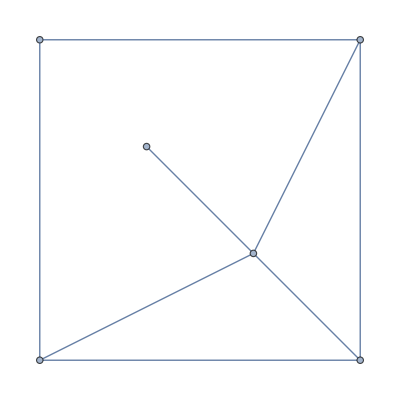
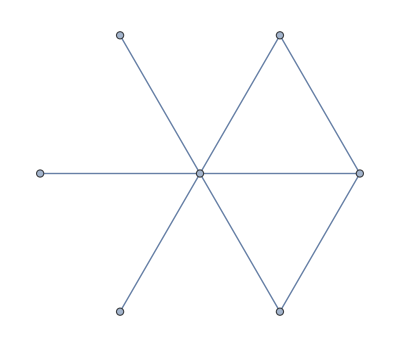
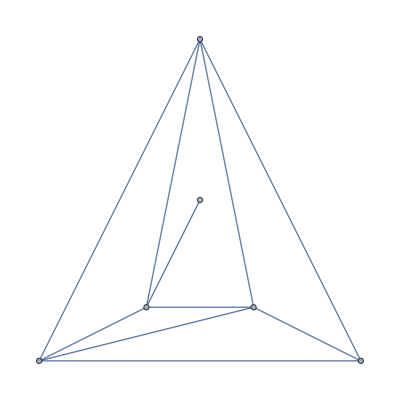
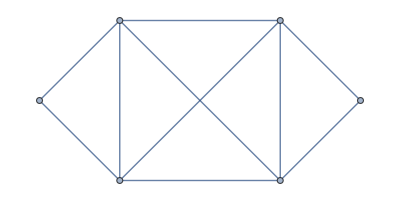
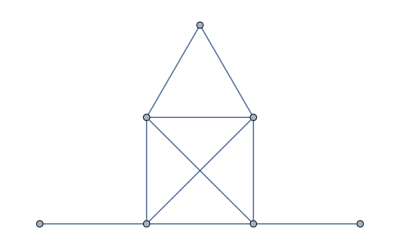
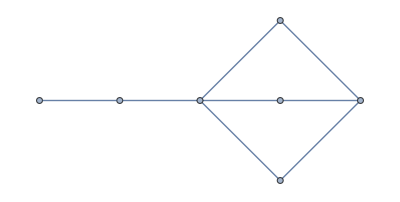
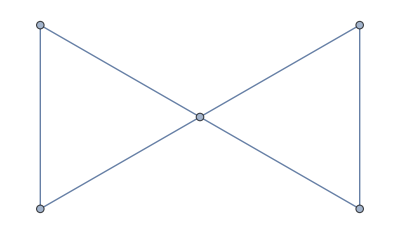
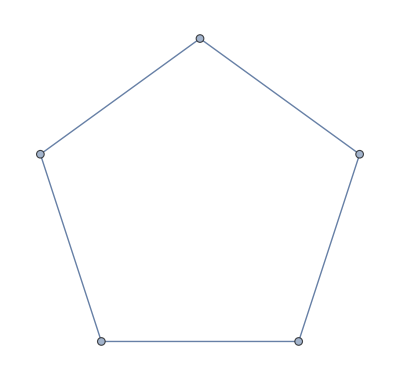
Small[{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}]

```mathematica
isospectralpairsconnected//Small (* These are the suspects. Many can immediately be eliminated after checking Euler characteristics or for reasons such as being clearly isomorphic. *)
```

```mathematica
DeterminantD/@{-Graphics-,-Graphics-,-Graphics-}//FullSimplify (* We here check for multiplicity. Each pair or set is checked individually. *)
```

{-576 ⅈ Sin[k/3]^3,6144 Sin[k/6]^2 Sin[k/3]^2,384 ⅈ Cos[k/6]^5 Sin[k/6]}

```mathematica
Finalisospectralpairsconnected={{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}; (* These are the final isospectral pairs with at most seven vertices after checking multiplicities. *)
```

```mathematica
Map[GraphPlot[EdgeList@#,GraphLayout->"SpringElectricalEmbedding",ImageSize->70]&]/@Finalisospectralpairsconnected
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
DeterminantD/@{-Graphics-,-Graphics-}
```

{-192 ⅇ^(-ⅈ k) (-1+ⅇ^((ⅈ k)/2))^3 (1+ⅇ^((ⅈ k)/2)),-64 ⅇ^(-ⅈ k) (-1+ⅇ^((ⅈ k)/2))^3 (1+ⅇ^((ⅈ k)/2))}

Then for trees with at most ten vertices

```mathematica
trees=PendantEdgeAddAll[-Graphics-,8];
```

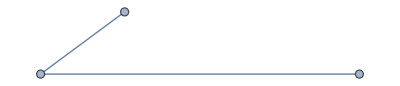
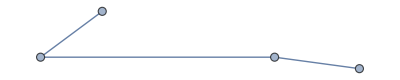
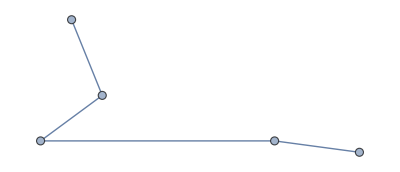
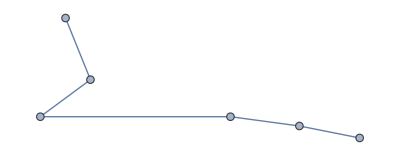
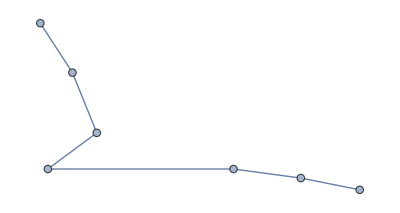
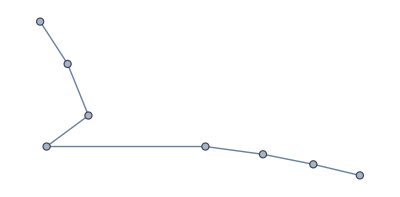
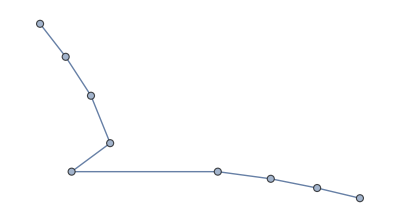
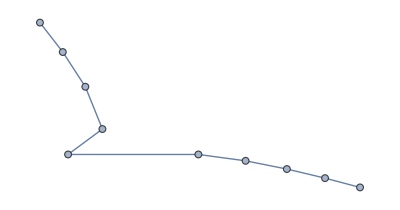
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
suspecttrees=IsospectralPairs[trees]
```

```mathematica
DeterminantD/@{-Graphics-,-Graphics-}//Simplify//Factor  (* We here check for multiplicity. Each pair is checked individually. *)
```

{-48 ⅇ^(-ⅈ k) (-1+ⅇ^((ⅈ k)/9)) (1+ⅇ^((ⅈ k)/9)) (1+ⅇ^((2 ⅈ k)/9))^2 (1-ⅇ^((ⅈ k)/9)+ⅇ^((2 ⅈ k)/9)) (1+ⅇ^((ⅈ k)/9)+ⅇ^((2 ⅈ k)/9)) (1+ⅇ^((4 ⅈ k)/9)) (3-4 ⅇ^((2 ⅈ k)/9)+3 ⅇ^((4 ⅈ k)/9)),48 ⅇ^(-ⅈ k) (-1+ⅇ^((ⅈ k)/9)) (1+ⅇ^((ⅈ k)/9)) (1+ⅇ^((2 ⅈ k)/9))^2 (1-ⅇ^((ⅈ k)/9)+ⅇ^((2 ⅈ k)/9)) (1+ⅇ^((ⅈ k)/9)+ⅇ^((2 ⅈ k)/9)) (1+ⅇ^((4 ⅈ k)/9)) (3-4 ⅇ^((2 ⅈ k)/9)+3 ⅇ^((4 ⅈ k)/9))}

```mathematica
Finalisospectraltrees={{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}};
(* The final checked trees with at most ten vertices *)
Map[GraphPlot[EdgeList@#,GraphLayout->"SpringEmbedding",ImageSize->70]&]/@Finalisospectraltrees
```

```mathematica
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}} (* Different embedding. *)
```

Here we do it for trees with twelve vertices.

```mathematica
treesten=PendantEdgeAddAll[-Graphics-,10]; (* Lets do it with up to 12 vertices. This takes a few hours on a laptop. *)
```

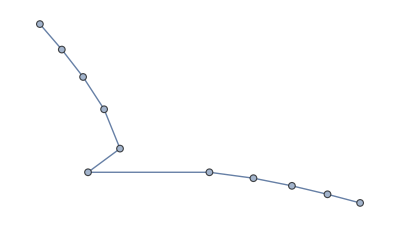
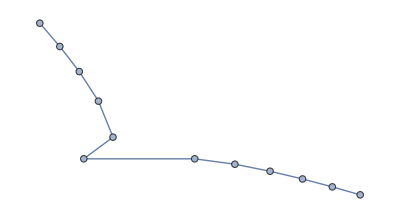
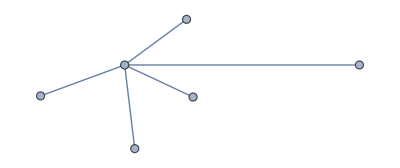
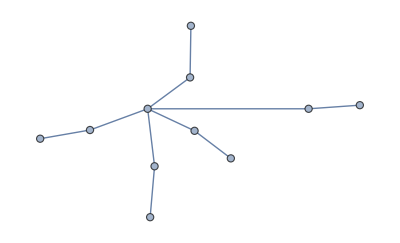
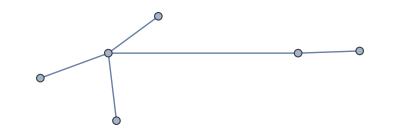
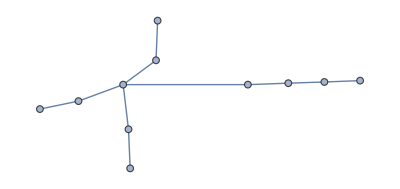
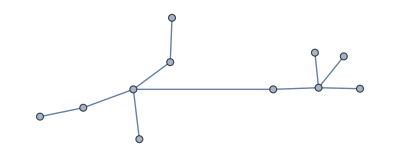
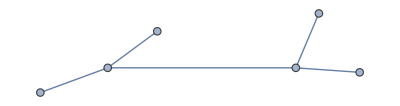
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
IsospectralPairs[treesten]  (* The suspects. *)
```

```mathematica
DeterminantD/@{-Graphics-,-Graphics-}//Simplify  (* Testing multiplicities *)
```

{-64 ⅇ^(-ⅈ k) (-9-6 ⅇ^((2 ⅈ k)/11)-5 ⅇ^((6 ⅈ k)/11)+2 ⅇ^((10 ⅈ k)/11)-2 ⅇ^((12 ⅈ k)/11)+5 ⅇ^((16 ⅈ k)/11)+6 ⅇ^((20 ⅈ k)/11)+9 ⅇ^(2 ⅈ k)),64 ⅇ^(-ⅈ k) (-9-6 ⅇ^((2 ⅈ k)/11)-5 ⅇ^((6 ⅈ k)/11)+2 ⅇ^((10 ⅈ k)/11)-2 ⅇ^((12 ⅈ k)/11)+5 ⅇ^((16 ⅈ k)/11)+6 ⅇ^((20 ⅈ k)/11)+9 ⅇ^(2 ⅈ k))}

```mathematica
Finalisospectraltreesten={{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}} (* The checked trees with up to twelve vertices *)
```

Here we do it for a decorated square.

```mathematica
treesfromsquare=PendantEdgeAddAll[-Graphics-,6]; (* Here we create a square decorated with edges and trees. *)
```

Below are the checked isospectral sets from a decorated square. There is one triplet and the rest are pairs. Note that the members of the pairs must be scaled to have the same length in order to be isospectral.

```mathematica
checkedsquarepairs=
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}
```

Here we do it for a decorated hexagon .

```mathematica
treesfromhexagon=PendantEdgeAddAll[-Graphics-,6];
```

Below are the checked decorated hexagon isospectral sets. I found one triplet and the rest are pairs.

```mathematica
checkedhexagonpairs={{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}.{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}
```

Below are checked isospectral pairs from this decorated graph - -Graphics-which was decorated with at most six edges.

```mathematica
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}
```

Below are checked isospectral pairs from this decorated graph - -Graphics-which was decorated with at most five edges.

```mathematica
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}
```

## The following cells check the isospectrality of one pair and one triplet from the paper which we do “by hand” in order to check the programs predictions.

The following cell gives the vertex and edge scattering matrix for graph b): -Graphics-which is the isospectral partner of the loop graph when L1=L3=1/4 and L2=2/4 according to Pistol, arXiv.
It also computes ∑(k) following Berkolaiko which shows that graph b) has the same eigenfrequencies as graph a).

```mathematica
L1=L3=2;
L2=4;
Sv=({{0, -1/2, 1/2, 1/2, 0, 1/2}, {1, 0, 0, 0, 0, 0}, {0, 1/2, 1/2, -1/2, 0, 1/2}, {0, 1/2, -1/2, 1/2, 0, 1/2}, {0, 1/2, 1/2, 1/2, 0, -1/2}, {0, 0, 0, 0, 1, 0}});
Se[k_]:=({{ⅇ^(ⅈ k L1), 0, 0, 0, 0, 0}, {0, ⅇ^(ⅈ k L1), 0, 0, 0, 0}, {0, 0, ⅇ^(ⅈ k L2), 0, 0, 0}, {0, 0, 0, ⅇ^(ⅈ k L2), 0, 0}, {0, 0, 0, 0, ⅇ^(ⅈ k L3), 0}, {0, 0, 0, 0, 0, ⅇ^(ⅈ k L3)}});
Id=({{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}});
Sigma[k_]:=Det[Id-Sv.Se[k]]//FullSimplify
Sigma[k] (* The secular determinant *)

(* Here we do it again but with an extra valence two vertex on the left side of the loop to check *)
Sv=({{0, -1/2, 1/2, 0, 0, 1/2, 0, 1/2}, {1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 1/2, -1/2, 0, 0, 1/2, 0, 1/2}, {0, 1/2, 1/2, 0, 0, -1/2, 0, 1/2}, {0, 0, 0, 0, 1, 0, 0, 0}, {0, 1/2, 1/2, 0, 0, 1/2, 0, -1/2}, {0, 0, 0, 1, 0, 0, 0, 0}});

Se[k_]:=({{ⅇ^(ⅈ k L1), 0, 0, 0, 0, 0, 0, 0}, {0, ⅇ^(ⅈ k L1), 0, 0, 0, 0, 0, 0}, {0, 0, ⅇ^(ⅈ k L1), 0, 0, 0, 0, 0}, {0, 0, 0, ⅇ^(ⅈ k L1), 0, 0, 0, 0}, {0, 0, 0, 0, ⅇ^(ⅈ k L1), 0, 0, 0}, {0, 0, 0, 0, 0, ⅇ^(ⅈ k L1), 0, 0}, {0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k L1), 0}, {0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k L1)}});
Id=({{1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 1}});
Sigma[k_]:=Det[Id-Sv.Se[k]]//FullSimplify;
Sigma[k]

L1=4;L2=4;
Det[({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}})-({{0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}, {1, 0, 0, 0}}).({{ⅇ^(ⅈ k L1), 0, 0, 0}, {0, ⅇ^(ⅈ k L1), 0, 0}, {0, 0, ⅇ^(ⅈ k L2), 0}, {0, 0, 0, ⅇ^(ⅈ k L2)}})]//Simplify (* The loop with two vertices. The secular determinant *)
DeterminantD[-Graphics-]//Simplify (* The same secular determinant apart from a factor which never gives a root *)
(* Solve[Sigma[k]==0,k]   The eigenfrequencies according to the handcalculated Sv and Se *)
GraphRoots[-Graphics-] (* The same eigenfrequencies according to my program. *)
Sv=({{0, -1/2, 0, 1/2, 1/2, 0, 1/2, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1/2, 0, -1/2, 1/2, 0, 1/2, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -1/2, 0, 1/2, 1/2, 0, 1/2, 0}, {0, 1/2, 0, 1/2, -1/2, 0, 1/2, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1/2, 0, -1/2, 1/2, 0, 1/2, 0}, {0, 1/2, 0, 1/2, 1/2, 0, -1/2, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 1/2, 0, 1/2, -1/2, 0, 1/2, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 1/2, 0, 1/2, 1/2, 0, -1/2, 0}});(*-Graphics-*)
Se[k_]:=({{ⅇ^(ⅈ k 2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, ⅇ^(ⅈ k 2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, ⅇ^(ⅈ k 2), 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, ⅇ^(ⅈ k 2), 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, ⅇ^(ⅈ k 1), 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, ⅇ^(ⅈ k 1), 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k 1), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k 1), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k 1), 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k 1), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k 1), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k 1)}});
Id=({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});
Sigma[k_]:=Det[Id-Sv.Se[k]]//Simplify;
Sigma[k]
```

(-1+ⅇ^(8 ⅈ k))^2

(-1+ⅇ^(8 ⅈ k))^2

(-1+ⅇ^(8 ⅈ k))^2

-8 ⅇ^(-ⅈ k) (-1+ⅇ^(ⅈ k))^2

{{k→ConditionalExpression[6 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[2 π (-1+3 C[1]), C[1]∈ℤ]},{k→ConditionalExpression[2 (π+3 π C[1]), C[1]∈ℤ]}}

(-1+ⅇ^(8 ⅈ k))^2

The following cell shows that the graphs -Graphics-have the same secular determinant.

```mathematica
nn=nnm;
Subscript[L, 1]=nn;Subscript[L, 2]=1;Subscript[L, 3]=1;
sum=(Subscript[L, 1]+2 Subscript[L, 2]+2 Subscript[L, 3]);


Sv=({{0, -1/3, 2/3, 0, 2/3, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -1/2, 0, 1/2, 1/2, 0, 1/2, 0}, {0, 2/3, -1/3, 0, 2/3, 0, 0, 0, 0, 0}, {0, 0, 0, 1/2, 0, -1/2, 1/2, 0, 1/2, 0}, {0, 2/3, 2/3, 0, -1/3, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 1/2, 0, 1/2, -1/2, 0, 1/2, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 1/2, 0, 1/2, 1/2, 0, -1/2, 0}});  (* This is for -Graphics-*)
Se[k_]:=({{ⅇ^(ⅈ k Subscript[L, 1]), 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, ⅇ^(ⅈ k Subscript[L, 1]), 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, ⅇ^(ⅈ k Subscript[L, 2]), 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, ⅇ^(ⅈ k Subscript[L, 2]), 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, ⅇ^(ⅈ k Subscript[L, 2]), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, ⅇ^(ⅈ k Subscript[L, 2]), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k Subscript[L, 3]), 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k Subscript[L, 3]), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k Subscript[L, 3]), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k Subscript[L, 3])}})
Id=({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});
Det[Id-Sv.Se[k]]//Simplify

Subscript[L, 1]=nn;Subscript[L, 2]=4;

Sv=({{0, -1/3, 2/3, 2/3}, {1, 0, 0, 0}, {0, 2/3, 2/3, -1/3}, {0, 2/3, -1/3, 2/3}});   (* This for-Graphics- *)
Se[k_]:=({{ⅇ^(ⅈ k Subscript[L, 1]), 0, 0, 0}, {0, ⅇ^(ⅈ k Subscript[L, 1]), 0, 0}, {0, 0, ⅇ^(ⅈ k Subscript[L, 2]), 0}, {0, 0, 0, ⅇ^(ⅈ k Subscript[L, 2])}});
Id=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
Det[Id-Sv.Se[k]]//Simplify
```

1/3 (-1+ⅇ^(4 ⅈ k)) (-3+ⅇ^(4 ⅈ k)-ⅇ^(2 ⅈ k nnm)+3 ⅇ^(2 ⅈ k (2+nnm)))

1/3 (-1+ⅇ^(4 ⅈ k)) (-3+ⅇ^(4 ⅈ k)-ⅇ^(2 ⅈ k nnm)+3 ⅇ^(2 ⅈ k (2+nnm)))

The following cell finds the secular determinant of -Graphics-by hand which agrees with the results of the program (apart from this factor which never contributes a root).

```mathematica
k=.
L1=4;
L2=2;
L3=2;
L4:=L1-L3;
Sv=({{2/3, -1/3, 2/3, 0, 0, 0, 0, 0}, {-1/3, 2/3, 2/3, 0, 0, 0, 0, 0}, {0, 0, 0, -1/3, 2/3, 0, 2/3, 0}, {2/3, 2/3, -1/3, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 2/3, -1/3, 0, 2/3, 0}, {0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 2/3, 2/3, 0, -1/3, 0}}); (* This is the bondscattering matrix I get *)

Se[k_]:=({{ⅇ^(ⅈ k L1), 0, 0, 0, 0, 0, 0, 0}, {0, ⅇ^(ⅈ k L1), 0, 0, 0, 0, 0, 0}, {0, 0, ⅇ^(ⅈ k L2), 0, 0, 0, 0, 0}, {0, 0, 0, ⅇ^(ⅈ k L2), 0, 0, 0, 0}, {0, 0, 0, 0, ⅇ^(ⅈ k L3), 0, 0, 0}, {0, 0, 0, 0, 0, ⅇ^(ⅈ k L3), 0, 0}, {0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k L4), 0}, {0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k L4)}});
Id=({{1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 1}});
Se[k];
Det[Id-Sv.Se[k]]//Simplify                                        (* What the handcalculation gets*)
Sigma[k_]:=Det[Id-Sv.Se[k]]//FullSimplify;
Sigma[k];
DeterminantD[#,10]&@-Graphics-//Simplify (* What my program gets*)
```

1/9 (-1+ⅇ^(4 ⅈ k))^2 (9+11 ⅇ^(4 ⅈ k)+11 ⅇ^(8 ⅈ k)+9 ⅇ^(12 ⅈ k))

64 ⅇ^(-10 ⅈ k) (-1+ⅇ^(4 ⅈ k))^2 (9+11 ⅇ^(4 ⅈ k)+11 ⅇ^(8 ⅈ k)+9 ⅇ^(12 ⅈ k))

Here we test the two isospectral partners of the loop

```mathematica
conn=-Graphics-;
DeterminantD/@{-Graphics-,-Graphics-,-Graphics-}//Simplify
h4=VertexReplace[-Graphics-,Table[i->Subscript[a, i],{i,25}]];
h5=VertexReplace[-Graphics-,Table[i->Subscript[b, i],{i,25}]];
h6=VertexReplace[-Graphics-,Table[i->Subscript[c, i],{i,25}]];
{GraphPlot[h4,VertexLabels->"Name"],
GraphPlot[h5,VertexLabels->"Name"],
GraphPlot[h6,VertexLabels->"Name"]}

hx=GraphAddContract[h4,Allconnected⟦7⟧,Subscript[a, 3],2];
hy=GraphAddContract[h5,Allconnected⟦7⟧,Subscript[b, 3],2];
hx=Graph[hx,EdgeWeight->{1<->6->1}];
hy=Graph[hy,EdgeWeight->{1<->6->1}];
hz=GraphAddContract[h6,Allconnected⟦7⟧,Subscript[c, 1],1];
hw=GraphAddContract[h6,Allconnected⟦7⟧,Subscript[c, 3],1];
(DeterminantD[hx]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
(DeterminantD[hy]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
(DeterminantD[hz]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
(DeterminantD[hw]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
{GraphPlot[hx,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],GraphPlot[hy,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
```

{256 ⅇ^(-ⅈ k) (-1+ⅇ^(ⅈ k))^2,128 ⅇ^(-ⅈ k) (-1+ⅇ^(ⅈ k))^2,16384 ⅇ^(-ⅈ k) (-1+ⅇ^(ⅈ k))^2}

{-Graphics-,-Graphics-,-Graphics-}

(-1+ⅇ^((ⅈ k)/16))^5 (1+ⅇ^((ⅈ k)/16)+ⅇ^((ⅈ k)/8)+ⅇ^((3 ⅈ k)/16))^3 (20+40 ⅇ^((ⅈ k)/16)+55 ⅇ^((ⅈ k)/8)+50 ⅇ^((3 ⅈ k)/16)+71 ⅇ^((ⅈ k)/4)+88 ⅇ^((5 ⅈ k)/16)+95 ⅇ^((3 ⅈ k)/8)+82 ⅇ^((7 ⅈ k)/16)+91 ⅇ^((ⅈ k)/2)+96 ⅇ^((9 ⅈ k)/16)+91 ⅇ^((5 ⅈ k)/8)+82 ⅇ^((11 ⅈ k)/16)+95 ⅇ^((3 ⅈ k)/4)+88 ⅇ^((13 ⅈ k)/16)+71 ⅇ^((7 ⅈ k)/8)+50 ⅇ^((15 ⅈ k)/16)+55 ⅇ^(ⅈ k)+40 ⅇ^((17 ⅈ k)/16)+20 ⅇ^((9 ⅈ k)/8))

(-1+ⅇ^((ⅈ k)/16))^5 (1+ⅇ^((ⅈ k)/16)+ⅇ^((ⅈ k)/8)+ⅇ^((3 ⅈ k)/16))^3 (20+40 ⅇ^((ⅈ k)/16)+55 ⅇ^((ⅈ k)/8)+50 ⅇ^((3 ⅈ k)/16)+71 ⅇ^((ⅈ k)/4)+88 ⅇ^((5 ⅈ k)/16)+95 ⅇ^((3 ⅈ k)/8)+82 ⅇ^((7 ⅈ k)/16)+91 ⅇ^((ⅈ k)/2)+96 ⅇ^((9 ⅈ k)/16)+91 ⅇ^((5 ⅈ k)/8)+82 ⅇ^((11 ⅈ k)/16)+95 ⅇ^((3 ⅈ k)/4)+88 ⅇ^((13 ⅈ k)/16)+71 ⅇ^((7 ⅈ k)/8)+50 ⅇ^((15 ⅈ k)/16)+55 ⅇ^(ⅈ k)+40 ⅇ^((17 ⅈ k)/16)+20 ⅇ^((9 ⅈ k)/8))

(-1+ⅇ^((ⅈ k)/24))^5 (1+ⅇ^((ⅈ k)/24)+ⅇ^((ⅈ k)/12)+ⅇ^((ⅈ k)/8))^3 (1+ⅇ^((ⅈ k)/6))^2 (30+60 ⅇ^((ⅈ k)/24)+77 ⅇ^((ⅈ k)/12)+66 ⅇ^((ⅈ k)/8)+49 ⅇ^((ⅈ k)/6)+36 ⅇ^((5 ⅈ k)/24)+26 ⅇ^((ⅈ k)/4)+32 ⅇ^((7 ⅈ k)/24)+94 ⅇ^((ⅈ k)/3)+140 ⅇ^((3 ⅈ k)/8)+141 ⅇ^((5 ⅈ k)/12)+98 ⅇ^((11 ⅈ k)/24)+75 ⅇ^((ⅈ k)/2)+72 ⅇ^((13 ⅈ k)/24)+75 ⅇ^((7 ⅈ k)/12)+98 ⅇ^((5 ⅈ k)/8)+141 ⅇ^((2 ⅈ k)/3)+140 ⅇ^((17 ⅈ k)/24)+94 ⅇ^((3 ⅈ k)/4)+32 ⅇ^((19 ⅈ k)/24)+26 ⅇ^((5 ⅈ k)/6)+36 ⅇ^((7 ⅈ k)/8)+49 ⅇ^((11 ⅈ k)/12)+66 ⅇ^((23 ⅈ k)/24)+77 ⅇ^(ⅈ k)+60 ⅇ^((25 ⅈ k)/24)+30 ⅇ^((13 ⅈ k)/12))

(-1+ⅇ^((ⅈ k)/24))^5 (1+ⅇ^((ⅈ k)/24)+ⅇ^((ⅈ k)/12)+ⅇ^((ⅈ k)/8))^3 (1+ⅇ^((ⅈ k)/3))^2 (30+60 ⅇ^((ⅈ k)/24)+77 ⅇ^((ⅈ k)/12)+66 ⅇ^((ⅈ k)/8)+99 ⅇ^((ⅈ k)/6)+136 ⅇ^((5 ⅈ k)/24)+147 ⅇ^((ⅈ k)/4)+130 ⅇ^((7 ⅈ k)/24)+139 ⅇ^((ⅈ k)/3)+152 ⅇ^((3 ⅈ k)/8)+139 ⅇ^((5 ⅈ k)/12)+130 ⅇ^((11 ⅈ k)/24)+147 ⅇ^((ⅈ k)/2)+136 ⅇ^((13 ⅈ k)/24)+99 ⅇ^((7 ⅈ k)/12)+66 ⅇ^((5 ⅈ k)/8)+77 ⅇ^((2 ⅈ k)/3)+60 ⅇ^((17 ⅈ k)/24)+30 ⅇ^((3 ⅈ k)/4))

## Experiments with the star graph.

Here we test the isospectrality of the decorated star. We first do it for a star with equal length of the leaves.

```mathematica
star=.;loop1=.;loop2=.;v1=.;v2=.;u=.;v=.;
v=Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];
star=VertexReplace[-Graphics-,Table[i->Subscript[a, i],{i,25}]];

loop1=VertexReplace[-Graphics-,Table[i->Subscript[b1, i],{i,25}]];loop2=VertexReplace[-Graphics-,Table[i->Subscript[b2, i],{i,25}]];
loop3=VertexReplace[-Graphics-,Table[i->Subscript[b3, i],{i,25}]];


v1=VertexReplace[v,Table[i->Subscript[d1, i],{i,25}]];
v2=VertexReplace[v,Table[i->Subscript[d2, i],{i,25}]];
v3=VertexReplace[v,Table[i->Subscript[d3, i],{i,25}]];


{decoratedstar1=VertexReplace[#,atable]&@IndexGraph@GraphAddContract3[star,loop1,loop2,loop3,Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[b1, 1],Subscript[b2, 1],Subscript[b3, 1]],
decoratedstar2=VertexReplace[#,btable]&@IndexGraph@GraphAddContract3[star,loop1,loop2,v1,Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[b1, 1],Subscript[b2, 1],Subscript[d1, 2]],
decoratedstar3=VertexReplace[#,ctable]&@IndexGraph@GraphAddContract3[star,loop1,v2,v1,Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[b1, 1],Subscript[d2, 2],Subscript[d1, 2]],
decoratedstar4=VertexReplace[#,dtable]&@IndexGraph@GraphAddContract3[star,v3,v2,v1,Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[d3, 2],Subscript[d2, 2],Subscript[d1, 2]]}


(DeterminantD[decoratedstar1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
(DeterminantD[decoratedstar2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
(DeterminantD[decoratedstar3]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
(DeterminantD[decoratedstar4]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

(-1+ⅇ^(2 ⅈ))^4 (1+ⅇ^(2 ⅈ))^5 (1+ⅇ^(4 ⅈ))^3 (3-4 ⅇ^(2 ⅈ)+4 ⅇ^(4 ⅈ)-4 ⅇ^(6 ⅈ)+3 ⅇ^(8 ⅈ))^2 (3+4 ⅇ^(2 ⅈ)+4 ⅇ^(4 ⅈ)+4 ⅇ^(6 ⅈ)+3 ⅇ^(8 ⅈ))

(-1+ⅇ^(2 ⅈ))^4 (1+ⅇ^(2 ⅈ))^5 (1+ⅇ^(4 ⅈ))^3 (3-4 ⅇ^(2 ⅈ)+4 ⅇ^(4 ⅈ)-4 ⅇ^(6 ⅈ)+3 ⅇ^(8 ⅈ))^2 (3+4 ⅇ^(2 ⅈ)+4 ⅇ^(4 ⅈ)+4 ⅇ^(6 ⅈ)+3 ⅇ^(8 ⅈ))

(-1+ⅇ^(2 ⅈ))^4 (1+ⅇ^(2 ⅈ))^5 (1+ⅇ^(4 ⅈ))^3 (3-4 ⅇ^(2 ⅈ)+4 ⅇ^(4 ⅈ)-4 ⅇ^(6 ⅈ)+3 ⅇ^(8 ⅈ))^2 (3+4 ⅇ^(2 ⅈ)+4 ⅇ^(4 ⅈ)+4 ⅇ^(6 ⅈ)+3 ⅇ^(8 ⅈ))

«1 more identical outputs»

We then do it for a star with symbolic edgelengths.

```mathematica
c1=.;c2=.;
longstar=Graph[{1<->12,12<->2,1<->13,13<->3,1<->14,14<->4}];
longstar=VertexReplace[-Graphics-,Table[i->Subscript[a, i],{i,25}]];

{decoratedlongstar1=VertexReplace[#,atable]&@IndexGraph@GraphAddContract3[longstar,loop1,loop2,loop3,Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[b1, 1],Subscript[b2, 1],Subscript[b3, 1]],
decoratedlongstar2=VertexReplace[#,btable]&@IndexGraph@GraphAddContract3[longstar,loop1,loop2,v1,Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[b1, 1],Subscript[b2, 1],Subscript[d1, 2]],
decoratedlongstar3=VertexReplace[#,ctable]&@IndexGraph@GraphAddContract3[longstar,loop1,v2,v1,Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[b1, 1],Subscript[d2, 2],Subscript[d1, 2]],
decoratedlongstar4=VertexReplace[#,dtable]&@IndexGraph@GraphAddContract3[longstar,v3,v2,v1,Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[d3, 2],Subscript[d2, 2],Subscript[d1, 2]]};

decoratedlongstar1=VertexReplace[#,atable]&@IndexGraph@Graph[decoratedlongstar1,EdgeWeight->{Subscript[a, 1]<->Subscript[a, 2]->c1,Subscript[a, 1]<->Subscript[a, 3]->c2}];
decoratedlongstar2=VertexReplace[#,btable]&@IndexGraph@Graph[decoratedlongstar2,EdgeWeight->{Subscript[b, 1]<->Subscript[b, 2]->c1,Subscript[b, 1]<->Subscript[b, 3]->c2}];
decoratedlongstar3=VertexReplace[#,ctable]&@IndexGraph@Graph[decoratedlongstar3,EdgeWeight->{Subscript[c, 1]<->Subscript[c, 2]->c1,Subscript[c, 1]<->Subscript[c, 3]->c2}];
decoratedlongstar4=VertexReplace[#,dtable]&@IndexGraph@Graph[decoratedlongstar4,EdgeWeight->{Subscript[d, 1]<->Subscript[d, 2]->c1,Subscript[d, 1]<->Subscript[d, 3]->c2}];

{GraphPlot[decoratedlongstar1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[decoratedlongstar2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[decoratedlongstar3,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[decoratedlongstar4,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]}

x1=(DeterminantD[decoratedlongstar1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
x2=(DeterminantD[decoratedlongstar2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
x3=(DeterminantD[decoratedlongstar3]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
x4=(DeterminantD[decoratedlongstar4]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
{x1==x2,x1==x3,x1==x4}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

(-1+ⅇ^((216 ⅈ)/(28+c1+c2)))^3 (-81+9 ⅇ^((108 ⅈ)/(28+c1+c2))+81 ⅇ^((216 ⅈ)/(28+c1+c2))-33 ⅇ^((324 ⅈ)/(28+c1+c2))-27 ⅇ^((432 ⅈ)/(28+c1+c2))+19 ⅇ^((540 ⅈ)/(28+c1+c2))+3 ⅇ^((648 ⅈ)/(28+c1+c2))-3 ⅇ^((756 ⅈ)/(28+c1+c2))+9 ⅇ^((54 ⅈ (1+c1))/(28+c1+c2))+3 ⅇ^((54 ⅈ (3+c1))/(28+c1+c2))-33 ⅇ^((54 ⅈ (5+c1))/(28+c1+c2))-19 ⅇ^((54 ⅈ (7+c1))/(28+c1+c2))+19 ⅇ^((54 ⅈ (9+c1))/(28+c1+c2))+33 ⅇ^((54 ⅈ (11+c1))/(28+c1+c2))-3 ⅇ^((54 ⅈ (13+c1))/(28+c1+c2))-9 ⅇ^((54 ⅈ (15+c1))/(28+c1+c2))+9 ⅇ^((54 ⅈ (1+c2))/(28+c1+c2))+3 ⅇ^((54 ⅈ (3+c2))/(28+c1+c2))-33 ⅇ^((54 ⅈ (5+c2))/(28+c1+c2))-19 ⅇ^((54 ⅈ (7+c2))/(28+c1+c2))+19 ⅇ^((54 ⅈ (9+c2))/(28+c1+c2))+33 ⅇ^((54 ⅈ (11+c2))/(28+c1+c2))-3 ⅇ^((54 ⅈ (13+c2))/(28+c1+c2))-9 ⅇ^((54 ⅈ (15+c2))/(28+c1+c2))+3 ⅇ^((54 ⅈ (2+c1+c2))/(28+c1+c2))-3 ⅇ^((54 ⅈ (4+c1+c2))/(28+c1+c2))-19 ⅇ^((54 ⅈ (6+c1+c2))/(28+c1+c2))+27 ⅇ^((54 ⅈ (8+c1+c2))/(28+c1+c2))+33 ⅇ^((54 ⅈ (10+c1+c2))/(28+c1+c2))-81 ⅇ^((54 ⅈ (12+c1+c2))/(28+c1+c2))-9 ⅇ^((54 ⅈ (14+c1+c2))/(28+c1+c2))+81 ⅇ^((54 ⅈ (16+c1+c2))/(28+c1+c2)))

(-1+ⅇ^((216 ⅈ)/(28+c1+c2)))^3 (-81+9 ⅇ^((108 ⅈ)/(28+c1+c2))+81 ⅇ^((216 ⅈ)/(28+c1+c2))-33 ⅇ^((324 ⅈ)/(28+c1+c2))-27 ⅇ^((432 ⅈ)/(28+c1+c2))+19 ⅇ^((540 ⅈ)/(28+c1+c2))+3 ⅇ^((648 ⅈ)/(28+c1+c2))-3 ⅇ^((756 ⅈ)/(28+c1+c2))+9 ⅇ^((54 ⅈ (1+c1))/(28+c1+c2))+3 ⅇ^((54 ⅈ (3+c1))/(28+c1+c2))-33 ⅇ^((54 ⅈ (5+c1))/(28+c1+c2))-19 ⅇ^((54 ⅈ (7+c1))/(28+c1+c2))+19 ⅇ^((54 ⅈ (9+c1))/(28+c1+c2))+33 ⅇ^((54 ⅈ (11+c1))/(28+c1+c2))-3 ⅇ^((54 ⅈ (13+c1))/(28+c1+c2))-9 ⅇ^((54 ⅈ (15+c1))/(28+c1+c2))+9 ⅇ^((54 ⅈ (1+c2))/(28+c1+c2))+3 ⅇ^((54 ⅈ (3+c2))/(28+c1+c2))-33 ⅇ^((54 ⅈ (5+c2))/(28+c1+c2))-19 ⅇ^((54 ⅈ (7+c2))/(28+c1+c2))+19 ⅇ^((54 ⅈ (9+c2))/(28+c1+c2))+33 ⅇ^((54 ⅈ (11+c2))/(28+c1+c2))-3 ⅇ^((54 ⅈ (13+c2))/(28+c1+c2))-9 ⅇ^((54 ⅈ (15+c2))/(28+c1+c2))+3 ⅇ^((54 ⅈ (2+c1+c2))/(28+c1+c2))-3 ⅇ^((54 ⅈ (4+c1+c2))/(28+c1+c2))-19 ⅇ^((54 ⅈ (6+c1+c2))/(28+c1+c2))+27 ⅇ^((54 ⅈ (8+c1+c2))/(28+c1+c2))+33 ⅇ^((54 ⅈ (10+c1+c2))/(28+c1+c2))-81 ⅇ^((54 ⅈ (12+c1+c2))/(28+c1+c2))-9 ⅇ^((54 ⅈ (14+c1+c2))/(28+c1+c2))+81 ⅇ^((54 ⅈ (16+c1+c2))/(28+c1+c2)))

(-1+ⅇ^((216 ⅈ)/(28+c1+c2)))^3 (-81+9 ⅇ^((108 ⅈ)/(28+c1+c2))+81 ⅇ^((216 ⅈ)/(28+c1+c2))-33 ⅇ^((324 ⅈ)/(28+c1+c2))-27 ⅇ^((432 ⅈ)/(28+c1+c2))+19 ⅇ^((540 ⅈ)/(28+c1+c2))+3 ⅇ^((648 ⅈ)/(28+c1+c2))-3 ⅇ^((756 ⅈ)/(28+c1+c2))+9 ⅇ^((54 ⅈ (1+c1))/(28+c1+c2))+3 ⅇ^((54 ⅈ (3+c1))/(28+c1+c2))-33 ⅇ^((54 ⅈ (5+c1))/(28+c1+c2))-19 ⅇ^((54 ⅈ (7+c1))/(28+c1+c2))+19 ⅇ^((54 ⅈ (9+c1))/(28+c1+c2))+33 ⅇ^((54 ⅈ (11+c1))/(28+c1+c2))-3 ⅇ^((54 ⅈ (13+c1))/(28+c1+c2))-9 ⅇ^((54 ⅈ (15+c1))/(28+c1+c2))+9 ⅇ^((54 ⅈ (1+c2))/(28+c1+c2))+3 ⅇ^((54 ⅈ (3+c2))/(28+c1+c2))-33 ⅇ^((54 ⅈ (5+c2))/(28+c1+c2))-19 ⅇ^((54 ⅈ (7+c2))/(28+c1+c2))+19 ⅇ^((54 ⅈ (9+c2))/(28+c1+c2))+33 ⅇ^((54 ⅈ (11+c2))/(28+c1+c2))-3 ⅇ^((54 ⅈ (13+c2))/(28+c1+c2))-9 ⅇ^((54 ⅈ (15+c2))/(28+c1+c2))+3 ⅇ^((54 ⅈ (2+c1+c2))/(28+c1+c2))-3 ⅇ^((54 ⅈ (4+c1+c2))/(28+c1+c2))-19 ⅇ^((54 ⅈ (6+c1+c2))/(28+c1+c2))+27 ⅇ^((54 ⅈ (8+c1+c2))/(28+c1+c2))+33 ⅇ^((54 ⅈ (10+c1+c2))/(28+c1+c2))-81 ⅇ^((54 ⅈ (12+c1+c2))/(28+c1+c2))-9 ⅇ^((54 ⅈ (14+c1+c2))/(28+c1+c2))+81 ⅇ^((54 ⅈ (16+c1+c2))/(28+c1+c2)))

«1 more identical outputs»

{True,True,True}

And finally lets attach graphs at possible hot vertices. If c1 or c2 are not 1 there are no hot vertices.

```mathematica
c1=3;c2=2;
decoratedlongstar2attached1=Graph[#,EdgeWeight->{Subscript[b, 1]<->Subscript[b, 2]->c1,Subscript[b, 2]<->Subscript[b, 1]->c1,Subscript[b, 1]<->Subscript[b, 3]->c2,Subscript[b, 3]<->Subscript[b, 1]->c2}]&@GraphAddContract[decoratedlongstar2,Allconnected[[9]],Subscript[b, 26],1];
decoratedlongstar3attached1=Graph[#,EdgeWeight->{Subscript[c, 1]<->Subscript[c, 2]->c1,Subscript[c, 2]<->Subscript[c, 1]->c1,Subscript[c, 1]<->Subscript[c, 3]->c2,Subscript[c, 3]<->Subscript[c, 1]->c2}]&@GraphAddContract[decoratedlongstar3,Allconnected[[9]],Subscript[c, 27],1];
decoratedlongstar4attached1=Graph[#,EdgeWeight->{Subscript[d, 1]<->Subscript[d, 2]->c1,Subscript[d, 2]<->Subscript[d, 1]->c1,Subscript[d, 1]<->Subscript[d, 3]->c2,Subscript[d, 3]<->Subscript[d, 1]->c2}]&@GraphAddContract[decoratedlongstar4,Allconnected[[9]],Subscript[d, 28],1];

GraphPlot[decoratedlongstar2attached1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"];
GraphPlot[decoratedlongstar3attached1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"];
GraphPlot[decoratedlongstar4attached1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"];

{GraphPlot[decoratedlongstar2attached1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],x1=(DeterminantD[decoratedlongstar2attached1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}}
{GraphPlot[decoratedlongstar3attached1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],x2=(DeterminantD[decoratedlongstar3attached1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}}
{GraphPlot[decoratedlongstar4attached1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],x3=(DeterminantD[decoratedlongstar4attached1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}}
{x1==x2,x1==x3}
GraphPlot[decoratedlongstar2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"];  (* 26, 27, 28 are hot vertices, 2, 3, 4 are also hot vertices from the second set. *)   
None;
```

{-Graphics-,(-1+ⅇ^((27 ⅈ)/40))^6 (1+ⅇ^((27 ⅈ)/40)+ⅇ^((27 ⅈ)/20)+ⅇ^((81 ⅈ)/40))^4 (1+ⅇ^((27 ⅈ)/10))^3 (675+1350 ⅇ^((27 ⅈ)/40)+2187 ⅇ^((27 ⅈ)/20)+2268 ⅇ^((81 ⅈ)/40)+2625 ⅇ^((27 ⅈ)/10)+2550 ⅇ^((27 ⅈ)/8)+2355 ⅇ^((81 ⅈ)/20)+2136 ⅇ^((189 ⅈ)/40)+1788 ⅇ^((27 ⅈ)/5)+1572 ⅇ^((243 ⅈ)/40)+944 ⅇ^((27 ⅈ)/4)+736 ⅇ^((297 ⅈ)/40)+799 ⅇ^((81 ⅈ)/10)+902 ⅇ^((351 ⅈ)/40)+1077 ⅇ^((189 ⅈ)/20)+724 ⅇ^((81 ⅈ)/8)+817 ⅇ^((54 ⅈ)/5)+666 ⅇ^((459 ⅈ)/40)+865 ⅇ^((243 ⅈ)/20)+1104 ⅇ^((513 ⅈ)/40)+1674 ⅇ^((27 ⅈ)/2)+2372 ⅇ^((567 ⅈ)/40)+2990 ⅇ^((297 ⅈ)/20)+3784 ⅇ^((621 ⅈ)/40)+4628 ⅇ^((81 ⅈ)/5)+4984 ⅇ^((135 ⅈ)/8)+4628 ⅇ^((351 ⅈ)/20)+3784 ⅇ^((729 ⅈ)/40)+2990 ⅇ^((189 ⅈ)/10)+2372 ⅇ^((783 ⅈ)/40)+1674 ⅇ^((81 ⅈ)/4)+1104 ⅇ^((837 ⅈ)/40)+865 ⅇ^((108 ⅈ)/5)+666 ⅇ^((891 ⅈ)/40)+817 ⅇ^((459 ⅈ)/20)+724 ⅇ^((189 ⅈ)/8)+1077 ⅇ^((243 ⅈ)/10)+902 ⅇ^((999 ⅈ)/40)+799 ⅇ^((513 ⅈ)/20)+736 ⅇ^((1053 ⅈ)/40)+944 ⅇ^(27 ⅈ)+1572 ⅇ^((1107 ⅈ)/40)+1788 ⅇ^((567 ⅈ)/20)+2136 ⅇ^((1161 ⅈ)/40)+2355 ⅇ^((297 ⅈ)/10)+2550 ⅇ^((243 ⅈ)/8)+2625 ⅇ^((621 ⅈ)/20)+2268 ⅇ^((1269 ⅈ)/40)+2187 ⅇ^((162 ⅈ)/5)+1350 ⅇ^((1323 ⅈ)/40)+675 ⅇ^((135 ⅈ)/4))}

{-Graphics-,(-1+ⅇ^((27 ⅈ)/40))^6 (1+ⅇ^((27 ⅈ)/40)+ⅇ^((27 ⅈ)/20)+ⅇ^((81 ⅈ)/40))^4 (1+ⅇ^((27 ⅈ)/10))^3 (675+1350 ⅇ^((27 ⅈ)/40)+2187 ⅇ^((27 ⅈ)/20)+2268 ⅇ^((81 ⅈ)/40)+2625 ⅇ^((27 ⅈ)/10)+2550 ⅇ^((27 ⅈ)/8)+2295 ⅇ^((81 ⅈ)/20)+2016 ⅇ^((189 ⅈ)/40)+1632 ⅇ^((27 ⅈ)/5)+1476 ⅇ^((243 ⅈ)/40)+864 ⅇ^((27 ⅈ)/4)+672 ⅇ^((297 ⅈ)/40)+807 ⅇ^((81 ⅈ)/10)+1014 ⅇ^((351 ⅈ)/40)+1113 ⅇ^((189 ⅈ)/20)+588 ⅇ^((81 ⅈ)/8)+637 ⅇ^((54 ⅈ)/5)+602 ⅇ^((459 ⅈ)/40)+837 ⅇ^((243 ⅈ)/20)+1080 ⅇ^((513 ⅈ)/40)+1846 ⅇ^((27 ⅈ)/2)+2708 ⅇ^((567 ⅈ)/40)+3250 ⅇ^((297 ⅈ)/20)+3808 ⅇ^((621 ⅈ)/40)+4656 ⅇ^((81 ⅈ)/5)+5048 ⅇ^((135 ⅈ)/8)+4656 ⅇ^((351 ⅈ)/20)+3808 ⅇ^((729 ⅈ)/40)+3250 ⅇ^((189 ⅈ)/10)+2708 ⅇ^((783 ⅈ)/40)+1846 ⅇ^((81 ⅈ)/4)+1080 ⅇ^((837 ⅈ)/40)+837 ⅇ^((108 ⅈ)/5)+602 ⅇ^((891 ⅈ)/40)+637 ⅇ^((459 ⅈ)/20)+588 ⅇ^((189 ⅈ)/8)+1113 ⅇ^((243 ⅈ)/10)+1014 ⅇ^((999 ⅈ)/40)+807 ⅇ^((513 ⅈ)/20)+672 ⅇ^((1053 ⅈ)/40)+864 ⅇ^(27 ⅈ)+1476 ⅇ^((1107 ⅈ)/40)+1632 ⅇ^((567 ⅈ)/20)+2016 ⅇ^((1161 ⅈ)/40)+2295 ⅇ^((297 ⅈ)/10)+2550 ⅇ^((243 ⅈ)/8)+2625 ⅇ^((621 ⅈ)/20)+2268 ⅇ^((1269 ⅈ)/40)+2187 ⅇ^((162 ⅈ)/5)+1350 ⅇ^((1323 ⅈ)/40)+675 ⅇ^((135 ⅈ)/4))}

{-Graphics-,(-1+ⅇ^((27 ⅈ)/40))^6 (1+ⅇ^((27 ⅈ)/40)+ⅇ^((27 ⅈ)/20)+ⅇ^((81 ⅈ)/40))^4 (1+ⅇ^((27 ⅈ)/10))^3 (675+1350 ⅇ^((27 ⅈ)/40)+2187 ⅇ^((27 ⅈ)/20)+2268 ⅇ^((81 ⅈ)/40)+2565 ⅇ^((27 ⅈ)/10)+2430 ⅇ^((27 ⅈ)/8)+2139 ⅇ^((81 ⅈ)/20)+1920 ⅇ^((189 ⅈ)/40)+1572 ⅇ^((27 ⅈ)/5)+1452 ⅇ^((243 ⅈ)/40)+924 ⅇ^((27 ⅈ)/4)+816 ⅇ^((297 ⅈ)/40)+843 ⅇ^((81 ⅈ)/10)+846 ⅇ^((351 ⅈ)/40)+861 ⅇ^((189 ⅈ)/20)+444 ⅇ^((81 ⅈ)/8)+517 ⅇ^((54 ⅈ)/5)+506 ⅇ^((459 ⅈ)/40)+957 ⅇ^((243 ⅈ)/20)+1416 ⅇ^((513 ⅈ)/40)+2158 ⅇ^((27 ⅈ)/2)+2804 ⅇ^((567 ⅈ)/40)+3370 ⅇ^((297 ⅈ)/20)+3952 ⅇ^((621 ⅈ)/40)+4656 ⅇ^((81 ⅈ)/5)+4904 ⅇ^((135 ⅈ)/8)+4656 ⅇ^((351 ⅈ)/20)+3952 ⅇ^((729 ⅈ)/40)+3370 ⅇ^((189 ⅈ)/10)+2804 ⅇ^((783 ⅈ)/40)+2158 ⅇ^((81 ⅈ)/4)+1416 ⅇ^((837 ⅈ)/40)+957 ⅇ^((108 ⅈ)/5)+506 ⅇ^((891 ⅈ)/40)+517 ⅇ^((459 ⅈ)/20)+444 ⅇ^((189 ⅈ)/8)+861 ⅇ^((243 ⅈ)/10)+846 ⅇ^((999 ⅈ)/40)+843 ⅇ^((513 ⅈ)/20)+816 ⅇ^((1053 ⅈ)/40)+924 ⅇ^(27 ⅈ)+1452 ⅇ^((1107 ⅈ)/40)+1572 ⅇ^((567 ⅈ)/20)+1920 ⅇ^((1161 ⅈ)/40)+2139 ⅇ^((297 ⅈ)/10)+2430 ⅇ^((243 ⅈ)/8)+2565 ⅇ^((621 ⅈ)/20)+2268 ⅇ^((1269 ⅈ)/40)+2187 ⅇ^((162 ⅈ)/5)+1350 ⅇ^((1323 ⅈ)/40)+675 ⅇ^((135 ⅈ)/4))}

{False,False}

Here we test the isospectral pairs -Graphics- and-Graphics-for hot vertices.

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];
v=Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];  (* u = -Graphics- and the isospectral partner is v = -Graphics-. *)

s=Graph[{1<->2,2<->3,3<->4,4<->5,3<->6,6<->7,7<->8,8<->9,9<->10,10<->7}];
t=Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->3,5<->7,7<->8,8<->9,9<->10}]; (* s = -Graphics- and t = -Graphics- are the other two isospectral partners. *)

u=VertexReplace[u,Table[i->Subscript[a, i],{i,55}]];  (* This is a loop. Hot vertices are all of them, Subscript[a, 1]-Subscript[a, 8] *)
v=VertexReplace[v,Table[i->Subscript[b, i],{i,55}]]; (* Hot vertex is Subscript[b, 2] -Graphics-*)
s=VertexReplace[s,Table[i->Subscript[c, i],{i,55}]]; (* Hot vertices are Subscript[c, 3] and Subscript[c, 7] -Graphics- *)
t=VertexReplace[t,Table[i->Subscript[d, i],{i,55}]]; (* Hot vertex is Subscript[d, 3] -Graphics- *)
w1=Allconnected⟦151⟧;
GraphPlot[w1,VertexLabels->"Name"];
w1=VertexReplace[w1,Table[i->Subscript[e, i],{i,25}]];

h1=GraphAddContract[u,w1,Subscript[a, 1],Subscript[e, 5]];
h2=GraphAddContract[v,w1,Subscript[b, 2],Subscript[e, 5]];

h3=GraphAddContract[s,w1,Subscript[c, 7],Subscript[e, 2]];
h4=GraphAddContract[t,w1,Subscript[d, 3],Subscript[e, 2]];
h5=GraphAddContract[s,w1,Subscript[c, 3],Subscript[e, 2]];
h6=GraphAddContract[t,w1,Subscript[d, 5],Subscript[e, 2]];(* Subscript[d, 5] does not work *)

g=GraphAddContract[u,v,Subscript[a, 1],Subscript[e, 2]];
GraphPlot[s,EdgeLabels->"EdgeWeight",VertexLabels->"Name"];
GraphPlot[t,EdgeLabels->"EdgeWeight",VertexLabels->"Name"];
DeterminantD[s]//Simplify;
DeterminantD[t]//Simplify;
(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
Print["next set"]
xx1=(DeterminantD[h3]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
xx2=(DeterminantD[h4]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
xx3=(DeterminantD[h5]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
xx4=(DeterminantD[h6]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
(DeterminantD[h6]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
{xx1==xx2,xx1==xx3}
```

(-1+ⅇ^((ⅈ k)/16))^4 (1+ⅇ^((ⅈ k)/16))^2 (1+ⅇ^((ⅈ k)/8))^3 (15+30 ⅇ^((ⅈ k)/16)+33 ⅇ^((ⅈ k)/8)+24 ⅇ^((3 ⅈ k)/16)+39 ⅇ^((ⅈ k)/4)+62 ⅇ^((5 ⅈ k)/16)+74 ⅇ^((3 ⅈ k)/8)+62 ⅇ^((7 ⅈ k)/16)+62 ⅇ^((ⅈ k)/2)+70 ⅇ^((9 ⅈ k)/16)+82 ⅇ^((5 ⅈ k)/8)+70 ⅇ^((11 ⅈ k)/16)+62 ⅇ^((3 ⅈ k)/4)+62 ⅇ^((13 ⅈ k)/16)+74 ⅇ^((7 ⅈ k)/8)+62 ⅇ^((15 ⅈ k)/16)+39 ⅇ^(ⅈ k)+24 ⅇ^((17 ⅈ k)/16)+33 ⅇ^((9 ⅈ k)/8)+30 ⅇ^((19 ⅈ k)/16)+15 ⅇ^((5 ⅈ k)/4))

(-1+ⅇ^((ⅈ k)/16))^4 (1+ⅇ^((ⅈ k)/16))^2 (1+ⅇ^((ⅈ k)/8))^3 (15+30 ⅇ^((ⅈ k)/16)+33 ⅇ^((ⅈ k)/8)+24 ⅇ^((3 ⅈ k)/16)+39 ⅇ^((ⅈ k)/4)+62 ⅇ^((5 ⅈ k)/16)+74 ⅇ^((3 ⅈ k)/8)+62 ⅇ^((7 ⅈ k)/16)+62 ⅇ^((ⅈ k)/2)+70 ⅇ^((9 ⅈ k)/16)+82 ⅇ^((5 ⅈ k)/8)+70 ⅇ^((11 ⅈ k)/16)+62 ⅇ^((3 ⅈ k)/4)+62 ⅇ^((13 ⅈ k)/16)+74 ⅇ^((7 ⅈ k)/8)+62 ⅇ^((15 ⅈ k)/16)+39 ⅇ^(ⅈ k)+24 ⅇ^((17 ⅈ k)/16)+33 ⅇ^((9 ⅈ k)/8)+30 ⅇ^((19 ⅈ k)/16)+15 ⅇ^((5 ⅈ k)/4))

next set

(-1+ⅇ^((ⅈ k)/18))^4 (1+ⅇ^((ⅈ k)/18))^2 (1+ⅇ^((ⅈ k)/9))^3 (270+540 ⅇ^((ⅈ k)/18)+495 ⅇ^((ⅈ k)/9)+198 ⅇ^((ⅈ k)/6)+420 ⅇ^((2 ⅈ k)/9)+1026 ⅇ^((5 ⅈ k)/18)+1263 ⅇ^((ⅈ k)/3)+672 ⅇ^((7 ⅈ k)/18)+466 ⅇ^((4 ⅈ k)/9)+1028 ⅇ^((ⅈ k)/2)+1506 ⅇ^((5 ⅈ k)/9)+1016 ⅇ^((11 ⅈ k)/18)+632 ⅇ^((2 ⅈ k)/3)+1016 ⅇ^((13 ⅈ k)/18)+1506 ⅇ^((7 ⅈ k)/9)+1028 ⅇ^((5 ⅈ k)/6)+466 ⅇ^((8 ⅈ k)/9)+672 ⅇ^((17 ⅈ k)/18)+1263 ⅇ^(ⅈ k)+1026 ⅇ^((19 ⅈ k)/18)+420 ⅇ^((10 ⅈ k)/9)+198 ⅇ^((7 ⅈ k)/6)+495 ⅇ^((11 ⅈ k)/9)+540 ⅇ^((23 ⅈ k)/18)+270 ⅇ^((4 ⅈ k)/3))

(-1+ⅇ^((ⅈ k)/18))^4 (1+ⅇ^((ⅈ k)/18))^2 (1+ⅇ^((ⅈ k)/9))^3 (270+540 ⅇ^((ⅈ k)/18)+495 ⅇ^((ⅈ k)/9)+198 ⅇ^((ⅈ k)/6)+420 ⅇ^((2 ⅈ k)/9)+1026 ⅇ^((5 ⅈ k)/18)+1263 ⅇ^((ⅈ k)/3)+672 ⅇ^((7 ⅈ k)/18)+466 ⅇ^((4 ⅈ k)/9)+1028 ⅇ^((ⅈ k)/2)+1506 ⅇ^((5 ⅈ k)/9)+1016 ⅇ^((11 ⅈ k)/18)+632 ⅇ^((2 ⅈ k)/3)+1016 ⅇ^((13 ⅈ k)/18)+1506 ⅇ^((7 ⅈ k)/9)+1028 ⅇ^((5 ⅈ k)/6)+466 ⅇ^((8 ⅈ k)/9)+672 ⅇ^((17 ⅈ k)/18)+1263 ⅇ^(ⅈ k)+1026 ⅇ^((19 ⅈ k)/18)+420 ⅇ^((10 ⅈ k)/9)+198 ⅇ^((7 ⅈ k)/6)+495 ⅇ^((11 ⅈ k)/9)+540 ⅇ^((23 ⅈ k)/18)+270 ⅇ^((4 ⅈ k)/3))

(-1+ⅇ^((ⅈ k)/18))^4 (1+ⅇ^((ⅈ k)/18))^2 (1+ⅇ^((ⅈ k)/9))^3 (270+540 ⅇ^((ⅈ k)/18)+495 ⅇ^((ⅈ k)/9)+198 ⅇ^((ⅈ k)/6)+420 ⅇ^((2 ⅈ k)/9)+1026 ⅇ^((5 ⅈ k)/18)+1263 ⅇ^((ⅈ k)/3)+672 ⅇ^((7 ⅈ k)/18)+466 ⅇ^((4 ⅈ k)/9)+1028 ⅇ^((ⅈ k)/2)+1506 ⅇ^((5 ⅈ k)/9)+1016 ⅇ^((11 ⅈ k)/18)+632 ⅇ^((2 ⅈ k)/3)+1016 ⅇ^((13 ⅈ k)/18)+1506 ⅇ^((7 ⅈ k)/9)+1028 ⅇ^((5 ⅈ k)/6)+466 ⅇ^((8 ⅈ k)/9)+672 ⅇ^((17 ⅈ k)/18)+1263 ⅇ^(ⅈ k)+1026 ⅇ^((19 ⅈ k)/18)+420 ⅇ^((10 ⅈ k)/9)+198 ⅇ^((7 ⅈ k)/6)+495 ⅇ^((11 ⅈ k)/9)+540 ⅇ^((23 ⅈ k)/18)+270 ⅇ^((4 ⅈ k)/3))

{True,True}

Here we take a graph, G, and attach -Graphics-with their hot vertices at different vertices of G in different permutations and check that the resulting graphs are isospectral.

```mathematica
G=VertexReplace[#,ctable]&@Allconnected[[39]];
u1=VertexReplace[#,atable]&@CirculantGraph[8,1];
u2=VertexReplace[#,ftable]&@CirculantGraph[8,1];
v1=VertexReplace[#,btable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];  (* u = -Graphics- and the isospectral partner is v = -Graphics-. *)
v2=VertexReplace[#,dtable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];v3=VertexReplace[#,etable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];GraphPlot[v,VertexLabels->"Name"];  (* Hot vertex is Subscript[b, 2] -Graphics- *)
Gdecorated1=GraphAddContract4[G,u1,v1,v2,v3,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[a, 1],Subscript[b, 2],Subscript[d, 2],Subscript[e, 2]]
Gdecorated2=GraphAddContract4[G,u1,v1,v2,v3,Subscript[c, 2],Subscript[c, 1],Subscript[c, 3],Subscript[c, 4],Subscript[a, 1],Subscript[b, 2],Subscript[d, 2],Subscript[e, 2]]
Gdecorated3=GraphAddContract4[G,u1,v1,v2,v3,Subscript[c, 3],Subscript[c, 2],Subscript[c, 1],Subscript[c, 4],Subscript[a, 1],Subscript[b, 2],Subscript[d, 2],Subscript[e, 2]]
Gdecorated4=GraphAddContract4[G,u1,v1,v2,v3,Subscript[c, 4],Subscript[c, 2],Subscript[c, 3],Subscript[c, 1],Subscript[a, 1],Subscript[b, 2],Subscript[d, 2],Subscript[e, 2]]  
Gdecorated5=GraphAddContract4[G,u1,u2,v2,v3,Subscript[c, 4],Subscript[c, 2],Subscript[c, 3],Subscript[c, 1],Subscript[a, 1],Subscript[f, 2],Subscript[d, 2],Subscript[e, 2]]  
Gdecorated6=GraphAddContract4[G,u1,v1,u2,v3,Subscript[c, 4],Subscript[c, 2],Subscript[c, 3],Subscript[c, 1],Subscript[a, 1],Subscript[b, 2],Subscript[f, 2],Subscript[e, 2]]  

GraphPlot[G,VertexLabels->"Name"]
GraphPlot[Gdecorated1,VertexLabels->"Name"]

x1=(DeterminantD@Gdecorated1//Simplify)/.{_Integer -> 1}
x2=(DeterminantD@Gdecorated2//Simplify)/.{_Integer -> 1}
x3=(DeterminantD@Gdecorated3//Simplify)/.{_Integer -> 1}
x4=(DeterminantD@Gdecorated4//Simplify)/.{_Integer -> 1}
x5=(DeterminantD@Gdecorated5//Simplify)/.{_Integer -> 1}
x6=(DeterminantD@Gdecorated6//Simplify)/.{_Integer -> 1}
```

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

(1+ⅇ^((6 ⅈ)/5)) (1+ⅇ^((6 ⅈ)/5)+ⅇ^((12 ⅈ)/5)+ⅇ^((18 ⅈ)/5)) (1+ⅇ^((24 ⅈ)/5)) (1+ⅇ^((6 ⅈ)/5)+ⅇ^((12 ⅈ)/5)+ⅇ^((18 ⅈ)/5)+ⅇ^((24 ⅈ)/5)+ⅇ^(6 ⅈ)+ⅇ^((36 ⅈ)/5)+ⅇ^((42 ⅈ)/5)+ⅇ^((48 ⅈ)/5)+ⅇ^((54 ⅈ)/5)+ⅇ^(12 ⅈ)+ⅇ^((66 ⅈ)/5)+ⅇ^((72 ⅈ)/5)+ⅇ^((78 ⅈ)/5)+ⅇ^((84 ⅈ)/5)+ⅇ^(18 ⅈ)+ⅇ^((96 ⅈ)/5)+ⅇ^((102 ⅈ)/5)+ⅇ^((108 ⅈ)/5)+ⅇ^((114 ⅈ)/5)+ⅇ^(24 ⅈ)+ⅇ^((126 ⅈ)/5)+ⅇ^((132 ⅈ)/5)+ⅇ^((138 ⅈ)/5)+ⅇ^((144 ⅈ)/5)+ⅇ^(30 ⅈ)+ⅇ^((156 ⅈ)/5)+ⅇ^((162 ⅈ)/5)+ⅇ^((168 ⅈ)/5)+ⅇ^((174 ⅈ)/5)+ⅇ^(36 ⅈ)+ⅇ^((186 ⅈ)/5)+ⅇ^((192 ⅈ)/5)+ⅇ^((198 ⅈ)/5)+ⅇ^((204 ⅈ)/5)+ⅇ^(42 ⅈ)+ⅇ^((216 ⅈ)/5)+ⅇ^((222 ⅈ)/5)+ⅇ^((228 ⅈ)/5)) ⅇ^(-48 ⅈ)

(1+ⅇ^((6 ⅈ)/5)) (1+ⅇ^((6 ⅈ)/5)+ⅇ^((12 ⅈ)/5)+ⅇ^((18 ⅈ)/5)) (1+ⅇ^((24 ⅈ)/5)) (1+ⅇ^((6 ⅈ)/5)+ⅇ^((12 ⅈ)/5)+ⅇ^((18 ⅈ)/5)+ⅇ^((24 ⅈ)/5)+ⅇ^(6 ⅈ)+ⅇ^((36 ⅈ)/5)+ⅇ^((42 ⅈ)/5)+ⅇ^((48 ⅈ)/5)+ⅇ^((54 ⅈ)/5)+ⅇ^(12 ⅈ)+ⅇ^((66 ⅈ)/5)+ⅇ^((72 ⅈ)/5)+ⅇ^((78 ⅈ)/5)+ⅇ^((84 ⅈ)/5)+ⅇ^(18 ⅈ)+ⅇ^((96 ⅈ)/5)+ⅇ^((102 ⅈ)/5)+ⅇ^((108 ⅈ)/5)+ⅇ^((114 ⅈ)/5)+ⅇ^(24 ⅈ)+ⅇ^((126 ⅈ)/5)+ⅇ^((132 ⅈ)/5)+ⅇ^((138 ⅈ)/5)+ⅇ^((144 ⅈ)/5)+ⅇ^(30 ⅈ)+ⅇ^((156 ⅈ)/5)+ⅇ^((162 ⅈ)/5)+ⅇ^((168 ⅈ)/5)+ⅇ^((174 ⅈ)/5)+ⅇ^(36 ⅈ)+ⅇ^((186 ⅈ)/5)+ⅇ^((192 ⅈ)/5)+ⅇ^((198 ⅈ)/5)+ⅇ^((204 ⅈ)/5)+ⅇ^(42 ⅈ)+ⅇ^((216 ⅈ)/5)+ⅇ^((222 ⅈ)/5)+ⅇ^((228 ⅈ)/5)) ⅇ^(-48 ⅈ)

(1+ⅇ^((6 ⅈ)/5)) (1+ⅇ^((6 ⅈ)/5)+ⅇ^((12 ⅈ)/5)+ⅇ^((18 ⅈ)/5)) (1+ⅇ^((24 ⅈ)/5)) (1+ⅇ^((6 ⅈ)/5)+ⅇ^((12 ⅈ)/5)+ⅇ^((18 ⅈ)/5)+ⅇ^((24 ⅈ)/5)+ⅇ^(6 ⅈ)+ⅇ^((36 ⅈ)/5)+ⅇ^((42 ⅈ)/5)+ⅇ^((48 ⅈ)/5)+ⅇ^((54 ⅈ)/5)+ⅇ^(12 ⅈ)+ⅇ^((66 ⅈ)/5)+ⅇ^((72 ⅈ)/5)+ⅇ^((78 ⅈ)/5)+ⅇ^((84 ⅈ)/5)+ⅇ^(18 ⅈ)+ⅇ^((96 ⅈ)/5)+ⅇ^((102 ⅈ)/5)+ⅇ^((108 ⅈ)/5)+ⅇ^((114 ⅈ)/5)+ⅇ^(24 ⅈ)+ⅇ^((126 ⅈ)/5)+ⅇ^((132 ⅈ)/5)+ⅇ^((138 ⅈ)/5)+ⅇ^((144 ⅈ)/5)+ⅇ^(30 ⅈ)+ⅇ^((156 ⅈ)/5)+ⅇ^((162 ⅈ)/5)+ⅇ^((168 ⅈ)/5)+ⅇ^((174 ⅈ)/5)+ⅇ^(36 ⅈ)+ⅇ^((186 ⅈ)/5)+ⅇ^((192 ⅈ)/5)+ⅇ^((198 ⅈ)/5)+ⅇ^((204 ⅈ)/5)+ⅇ^(42 ⅈ)+ⅇ^((216 ⅈ)/5)+ⅇ^((222 ⅈ)/5)+ⅇ^((228 ⅈ)/5)) ⅇ^(-48 ⅈ)

«3 more identical outputs»

Let’s attach -Graphics-to many different graphs G.

```mathematica
Do[rnd=RandomInteger[{1,995}];
G=VertexReplace[#,ctable]&@Allconnected[[rnd]];
u1=VertexReplace[#,atable]&@CirculantGraph[8,1];
u2=VertexReplace[#,ftable]&@CirculantGraph[8,1];
v1=VertexReplace[#,btable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];  (* u = -Graphics- and the isospectral partner is v = -Graphics-. *)
v2=VertexReplace[#,dtable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];v3=VertexReplace[#,etable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];GraphPlot[v,VertexLabels->"Name"];  (* Hot vertex is Subscript[b, 2] -Graphics- *)
Gdecorated1=GraphAddContract4[G,u1,v1,v2,v3,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[a, 1],Subscript[b, 2],Subscript[d, 2],Subscript[e, 2]];
Gdecorated2=GraphAddContract4[G,u1,v1,v2,v3,Subscript[c, 2],Subscript[c, 1],Subscript[c, 3],Subscript[c, 4],Subscript[a, 1],Subscript[b, 2],Subscript[d, 2],Subscript[e, 2]];
Gdecorated3=GraphAddContract4[G,u1,v1,v2,v3,Subscript[c, 3],Subscript[c, 2],Subscript[c, 1],Subscript[c, 4],Subscript[a, 1],Subscript[b, 2],Subscript[d, 2],Subscript[e, 2]];
Gdecorated4=GraphAddContract4[G,u1,v1,v2,v3,Subscript[c, 4],Subscript[c, 2],Subscript[c, 3],Subscript[c, 1],Subscript[a, 1],Subscript[b, 2],Subscript[d, 2],Subscript[e, 2]] ;
Gdecorated5=GraphAddContract4[G,u1,u2,v2,v3,Subscript[c, 4],Subscript[c, 2],Subscript[c, 3],Subscript[c, 1],Subscript[a, 1],Subscript[f, 2],Subscript[d, 2],Subscript[e, 2]] ;
Gdecorated6=GraphAddContract4[G,u1,v1,u2,v3,Subscript[c, 4],Subscript[c, 2],Subscript[c, 3],Subscript[c, 1],Subscript[a, 1],Subscript[b, 2],Subscript[f, 2],Subscript[e, 2]] ; 

GraphPlot[G,VertexLabels->"Name"];
GraphPlot[Gdecorated1,VertexLabels->"Name"];

x1=(DeterminantD@Gdecorated1//Simplify)/.{_Integer -> 1};
x2=(DeterminantD@Gdecorated2//Simplify)/.{_Integer -> 1};
x3=(DeterminantD@Gdecorated3//Simplify)/.{_Integer -> 1};
x4=(DeterminantD@Gdecorated4//Simplify)/.{_Integer -> 1};
x5=(DeterminantD@Gdecorated5//Simplify)/.{_Integer -> 1};
x6=(DeterminantD@Gdecorated6//Simplify)/.{_Integer -> 1};
WriteString["stdout",{x1==x2,x1==x3,x1==x4,x1==x5,x1==x6}," "],
{i,1,25}]
```

{True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True}

## Let’s check if , and can generate isospectral graphs. They seem to form a generating set, being not isospectral, but still able to decorate symmetric graphs and generate hot vertices. The pair also is able to decorate general compact graphs generating isospectral graphs.

We first generate a set of graphs having a lot of symmetry, and the relevant graphs to attach.

```mathematica
(*CompleteGraph[5], WheelGraph[5],PetersenGraph[6,2],HararyGraph[5,10]*)
SymGraphs={-Graphics-,-Graphics-,-Graphics-,-Graphics-};
G=VertexReplace[#,gtable]&@-Graphics-;
u=VertexReplace[#,atable]&@CirculantGraph[8,1];
v=VertexReplace[#,btable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];  
w=VertexReplace[#,ctable]&@PathGraph[Range[9]] ; (* u = -Graphics- (with attachment vertex Subscript[a, 1]), v = -Graphics- (with attachment vertex Subscript[b, 3]) and w = -Graphics- (with attachment vertex Subscript[c, 5]). *)

GraphPlot[w,VertexLabels->"Name"];
w
```

-Graphics-

Let’s decorate a “random” graph with  , , and -Graphics-  in two ways and check if the resulting graphs are isospectral.

```mathematica
Gd=Allconnected[[985]];  (* Choose any graph ut to the maximum index of 995 *)

u1=VertexReplace[#,atable]&@CirculantGraph[8,1]; (*-Graphics-*)
u2=VertexReplace[#,btable]&@CirculantGraph[8,1];
v1=VertexReplace[#,ctable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}] ; (*-Graphics-*)
v2=VertexReplace[#,dtable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}] ;
w1=VertexReplace[#,etable]&@PathGraph[Range[9]]; (*-Graphics-*)
w2=VertexReplace[#,ftable]&@PathGraph[Range[9]];

h1=GraphAddContract2[Gd,w2,u1,1,2, Subscript[f, 5],Subscript[a, 3]];
h2=GraphAddContract2[Gd,w2,u1,2,1, Subscript[f, 5],Subscript[a, 3]];
{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"]}
{HighlightGraph[h1,{_Integer<->_Integer}], HighlightGraph[h2,{_Integer<->_Integer}]}
x1=(DeterminantD@h1)/.{_Integer ⅇ^(-ⅈ k) -> 1}
x2=(DeterminantD@h2)/.{_Integer ⅇ^(-ⅈ k) -> 1}   (* We need to do this to get rid of the sign problem. *)
x1==x2
IsomorphicGraphQ[h1,h2];
```

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

ⅇ^(-(57 ⅈ k)/35) (1966080000 ⅇ^((22 ⅈ k)/35)-16126771200 ⅇ^((24 ⅈ k)/35)-3620864000 ⅇ^((5 ⅈ k)/7)+50693734400 ⅇ^((26 ⅈ k)/35)+30854348800 ⅇ^((27 ⅈ k)/35)-58032128000 ⅇ^((4 ⅈ k)/5)-103992524800 ⅇ^((29 ⅈ k)/35)-62953881600 ⅇ^((6 ⅈ k)/7)+150234726400 ⅇ^((31 ⅈ k)/35)+269592166400 ⅇ^((32 ⅈ k)/35)+13008896000 ⅇ^((33 ⅈ k)/35)-269428326400 ⅇ^((34 ⅈ k)/35)-343015424000 ⅇ^(ⅈ k)-63609241600 ⅇ^((36 ⅈ k)/35)+373109555200 ⅇ^((37 ⅈ k)/35)+310253977600 ⅇ^((38 ⅈ k)/35)+66925363200 ⅇ^((39 ⅈ k)/35)-89800704000 ⅇ^((8 ⅈ k)/7)-259096576000 ⅇ^((41 ⅈ k)/35)-190464000000 ⅇ^((6 ⅈ k)/5)-246074572800 ⅇ^((43 ⅈ k)/35)-81782374400 ⅇ^((44 ⅈ k)/35)+533646540800 ⅇ^((9 ⅈ k)/7)+629342208000 ⅇ^((46 ⅈ k)/35)+159986483200 ⅇ^((47 ⅈ k)/35)-614789939200 ⅇ^((48 ⅈ k)/35)-903892172800 ⅇ^((7 ⅈ k)/5)-75769446400 ⅇ^((10 ⅈ k)/7)+653236633600 ⅇ^((51 ⅈ k)/35)+629997568000 ⅇ^((52 ⅈ k)/35)+56544460800 ⅇ^((53 ⅈ k)/35)-452034560000 ⅇ^((54 ⅈ k)/35)-282145587200 ⅇ^((11 ⅈ k)/7)-33842790400 ⅇ^((8 ⅈ k)/5)+33842790400 ⅇ^((58 ⅈ k)/35)+282145587200 ⅇ^((59 ⅈ k)/35)+452034560000 ⅇ^((12 ⅈ k)/7)-56544460800 ⅇ^((61 ⅈ k)/35)-629997568000 ⅇ^((62 ⅈ k)/35)-653236633600 ⅇ^((9 ⅈ k)/5)+75769446400 ⅇ^((64 ⅈ k)/35)+903892172800 ⅇ^((13 ⅈ k)/7)+614789939200 ⅇ^((66 ⅈ k)/35)-159986483200 ⅇ^((67 ⅈ k)/35)-629342208000 ⅇ^((68 ⅈ k)/35)-533646540800 ⅇ^((69 ⅈ k)/35)+81782374400 ⅇ^(2 ⅈ k)+246074572800 ⅇ^((71 ⅈ k)/35)+190464000000 ⅇ^((72 ⅈ k)/35)+259096576000 ⅇ^((73 ⅈ k)/35)+89800704000 ⅇ^((74 ⅈ k)/35)-66925363200 ⅇ^((15 ⅈ k)/7)-310253977600 ⅇ^((76 ⅈ k)/35)-373109555200 ⅇ^((11 ⅈ k)/5)+63609241600 ⅇ^((78 ⅈ k)/35)+343015424000 ⅇ^((79 ⅈ k)/35)+269428326400 ⅇ^((16 ⅈ k)/7)-13008896000 ⅇ^((81 ⅈ k)/35)-269592166400 ⅇ^((82 ⅈ k)/35)-150234726400 ⅇ^((83 ⅈ k)/35)+62953881600 ⅇ^((12 ⅈ k)/5)+103992524800 ⅇ^((17 ⅈ k)/7)+58032128000 ⅇ^((86 ⅈ k)/35)-30854348800 ⅇ^((87 ⅈ k)/35)-50693734400 ⅇ^((88 ⅈ k)/35)+3620864000 ⅇ^((89 ⅈ k)/35)+16126771200 ⅇ^((18 ⅈ k)/7)-1966080000 ⅇ^((92 ⅈ k)/35))

ⅇ^(-(57 ⅈ k)/35) (1966080000 ⅇ^((22 ⅈ k)/35)-16126771200 ⅇ^((24 ⅈ k)/35)-3620864000 ⅇ^((5 ⅈ k)/7)+50693734400 ⅇ^((26 ⅈ k)/35)+30854348800 ⅇ^((27 ⅈ k)/35)-58032128000 ⅇ^((4 ⅈ k)/5)-103992524800 ⅇ^((29 ⅈ k)/35)-62953881600 ⅇ^((6 ⅈ k)/7)+150234726400 ⅇ^((31 ⅈ k)/35)+269592166400 ⅇ^((32 ⅈ k)/35)+13008896000 ⅇ^((33 ⅈ k)/35)-269428326400 ⅇ^((34 ⅈ k)/35)-343015424000 ⅇ^(ⅈ k)-63609241600 ⅇ^((36 ⅈ k)/35)+373109555200 ⅇ^((37 ⅈ k)/35)+310253977600 ⅇ^((38 ⅈ k)/35)+66925363200 ⅇ^((39 ⅈ k)/35)-89800704000 ⅇ^((8 ⅈ k)/7)-259096576000 ⅇ^((41 ⅈ k)/35)-190464000000 ⅇ^((6 ⅈ k)/5)-246074572800 ⅇ^((43 ⅈ k)/35)-81782374400 ⅇ^((44 ⅈ k)/35)+533646540800 ⅇ^((9 ⅈ k)/7)+629342208000 ⅇ^((46 ⅈ k)/35)+159986483200 ⅇ^((47 ⅈ k)/35)-614789939200 ⅇ^((48 ⅈ k)/35)-903892172800 ⅇ^((7 ⅈ k)/5)-75769446400 ⅇ^((10 ⅈ k)/7)+653236633600 ⅇ^((51 ⅈ k)/35)+629997568000 ⅇ^((52 ⅈ k)/35)+56544460800 ⅇ^((53 ⅈ k)/35)-452034560000 ⅇ^((54 ⅈ k)/35)-282145587200 ⅇ^((11 ⅈ k)/7)-33842790400 ⅇ^((8 ⅈ k)/5)+33842790400 ⅇ^((58 ⅈ k)/35)+282145587200 ⅇ^((59 ⅈ k)/35)+452034560000 ⅇ^((12 ⅈ k)/7)-56544460800 ⅇ^((61 ⅈ k)/35)-629997568000 ⅇ^((62 ⅈ k)/35)-653236633600 ⅇ^((9 ⅈ k)/5)+75769446400 ⅇ^((64 ⅈ k)/35)+903892172800 ⅇ^((13 ⅈ k)/7)+614789939200 ⅇ^((66 ⅈ k)/35)-159986483200 ⅇ^((67 ⅈ k)/35)-629342208000 ⅇ^((68 ⅈ k)/35)-533646540800 ⅇ^((69 ⅈ k)/35)+81782374400 ⅇ^(2 ⅈ k)+246074572800 ⅇ^((71 ⅈ k)/35)+190464000000 ⅇ^((72 ⅈ k)/35)+259096576000 ⅇ^((73 ⅈ k)/35)+89800704000 ⅇ^((74 ⅈ k)/35)-66925363200 ⅇ^((15 ⅈ k)/7)-310253977600 ⅇ^((76 ⅈ k)/35)-373109555200 ⅇ^((11 ⅈ k)/5)+63609241600 ⅇ^((78 ⅈ k)/35)+343015424000 ⅇ^((79 ⅈ k)/35)+269428326400 ⅇ^((16 ⅈ k)/7)-13008896000 ⅇ^((81 ⅈ k)/35)-269592166400 ⅇ^((82 ⅈ k)/35)-150234726400 ⅇ^((83 ⅈ k)/35)+62953881600 ⅇ^((12 ⅈ k)/5)+103992524800 ⅇ^((17 ⅈ k)/7)+58032128000 ⅇ^((86 ⅈ k)/35)-30854348800 ⅇ^((87 ⅈ k)/35)-50693734400 ⅇ^((88 ⅈ k)/35)+3620864000 ⅇ^((89 ⅈ k)/35)+16126771200 ⅇ^((18 ⅈ k)/7)-1966080000 ⅇ^((92 ⅈ k)/35))

True

Let’s attach to 50 graphs just to be safe. I find them to always be isospectral.

```mathematica
u=VertexReplace[#,atable]&@CirculantGraph[8,1];
v=VertexReplace[#,btable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];  (*-Graphics-*)

Do[tmp=Allconnected[[j+100]];
h1=GraphAddContract2[tmp,u,v,1,2, Subscript[a, 1],Subscript[b, 2]];
h2=GraphAddContract2[tmp,u,v,2,1, Subscript[a, 1],Subscript[b, 2]];
{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"]};
x1=(DeterminantD@h1//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x2=(DeterminantD@h2//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
WriteString["stdout",x1==x2," "];
(*Print[x1==x2]*),{j,1,50}]
```

True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True True

Let’s introduce a symbolic edgelength such that the graphs are not equilateral. I still find them to always be isospectral.

```mathematica
c1=.
u=VertexReplace[#,atable]&@CirculantGraph[8,1];
v=VertexReplace[#,btable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];  (*-Graphics-*)

Gd=Allconnected[[111]];
h1=GraphAddContract2[Gd,u,v,1,2, Subscript[a, 1],Subscript[b, 2]];
h2=GraphAddContract2[Gd,u,v,2,1, Subscript[a, 1],Subscript[b, 2]];
{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"]};

h1=Graph[h1,EdgeWeight->{2<->7->c1}]; (* These vertices have to be set correctly *)
h2=Graph[h2,EdgeWeight->{2<->7->c1}];

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]}
x1=(DeterminantD@h1//Simplify)/.{_Integer -> 1}
x2=(DeterminantD@h2//Simplify)/.{_Integer -> 1}   (* We need to do this to get rid of the sign problem. *)
x1==x2
IsomorphicGraphQ[h1,h2];
```

{-Graphics-,-Graphics-}

ⅇ^(-ⅈ k) (1+ⅇ^(ⅈ (1+c1) k)+ⅇ^(2 ⅈ (1+c1) k)+ⅇ^(3 ⅈ (1+c1) k)) (1+ⅇ^(ⅈ (1+c1) k)+ⅇ^(4 ⅈ (1+c1) k)+ⅇ^(5 ⅈ (1+c1) k)) (1+ⅇ^(ⅈ k)+ⅇ^(ⅈ (1+c1) k)+ⅇ^(2 ⅈ (1+c1) k)+ⅇ^(3 ⅈ (1+c1) k)+ⅇ^(4 ⅈ (1+c1) k)+ⅇ^(5 ⅈ (1+c1) k)+ⅇ^(6 ⅈ (1+c1) k)+ⅇ^(7 ⅈ (1+c1) k)+ⅇ^(8 ⅈ (1+c1) k)+ⅇ^(9 ⅈ (1+c1) k)+ⅇ^(10 ⅈ (1+c1) k)+ⅇ^(11 ⅈ (1+c1) k)+ⅇ^(12 ⅈ (1+c1) k)+ⅇ^(13 ⅈ (1+c1) k)+ⅇ^(14 ⅈ (1+c1) k)+ⅇ^(15 ⅈ (1+c1) k)+ⅇ^(16 ⅈ (1+c1) k)+ⅇ^(17 ⅈ (1+c1) k)+ⅇ^(18 ⅈ (1+c1) k)+ⅇ^(19 ⅈ (1+c1) k)+ⅇ^(20 ⅈ (1+c1) k)+ⅇ^(21 ⅈ (1+c1) k)+ⅇ^(22 ⅈ (1+c1) k)+ⅇ^(23 ⅈ (1+c1) k)+ⅇ^(24 ⅈ (1+c1) k)+ⅇ^(25 ⅈ (1+c1) k)+ⅇ^(26 ⅈ (1+c1) k)+ⅇ^(27 ⅈ (1+c1) k)+ⅇ^(2 ⅈ c1 (1+c1) k)+36 ⅇ^(ⅈ (1+c1)^2 k)+13 ⅇ^(2 ⅈ (1+c1)^2 k)+ⅇ^(ⅈ (1+c1) (k+c1 k)))

ⅇ^(-ⅈ k) (1+ⅇ^(ⅈ (1+c1) k)+ⅇ^(2 ⅈ (1+c1) k)+ⅇ^(3 ⅈ (1+c1) k)) (1+ⅇ^(ⅈ (1+c1) k)+ⅇ^(4 ⅈ (1+c1) k)+ⅇ^(5 ⅈ (1+c1) k)) (1+ⅇ^(ⅈ k)+ⅇ^(ⅈ (1+c1) k)+ⅇ^(2 ⅈ (1+c1) k)+ⅇ^(3 ⅈ (1+c1) k)+ⅇ^(4 ⅈ (1+c1) k)+ⅇ^(5 ⅈ (1+c1) k)+ⅇ^(6 ⅈ (1+c1) k)+ⅇ^(7 ⅈ (1+c1) k)+ⅇ^(8 ⅈ (1+c1) k)+ⅇ^(9 ⅈ (1+c1) k)+ⅇ^(10 ⅈ (1+c1) k)+ⅇ^(11 ⅈ (1+c1) k)+ⅇ^(12 ⅈ (1+c1) k)+ⅇ^(13 ⅈ (1+c1) k)+ⅇ^(14 ⅈ (1+c1) k)+ⅇ^(15 ⅈ (1+c1) k)+ⅇ^(16 ⅈ (1+c1) k)+ⅇ^(17 ⅈ (1+c1) k)+ⅇ^(18 ⅈ (1+c1) k)+ⅇ^(19 ⅈ (1+c1) k)+ⅇ^(20 ⅈ (1+c1) k)+ⅇ^(21 ⅈ (1+c1) k)+ⅇ^(22 ⅈ (1+c1) k)+ⅇ^(23 ⅈ (1+c1) k)+ⅇ^(24 ⅈ (1+c1) k)+ⅇ^(25 ⅈ (1+c1) k)+ⅇ^(26 ⅈ (1+c1) k)+ⅇ^(27 ⅈ (1+c1) k)+ⅇ^(2 ⅈ c1 (1+c1) k)+36 ⅇ^(ⅈ (1+c1)^2 k)+13 ⅇ^(2 ⅈ (1+c1)^2 k)+ⅇ^(ⅈ (1+c1) (k+c1 k)))

True

Let’s decorate a “random” graph, Gd, with   , -Graphics- and  in different permutations at four vertices of Gd, and check if the resulting graphs are isospectral. I find that they are isospectral.

```mathematica
h=.

Gd=Allconnected[[1]];
(* Gd=TreeGraph[{1,2,3,4},{1<->2,1<->3,1<->4}];  This graph causes problems and some graphs are not isospectral if 
w1={VertexReplace[#,etable]&@PathGraph[Range[9]],Subscript[e, 5]};
w2={VertexReplace[#,ftable]&@PathGraph[Range[9]],Subscript[f, 1]};
w3={VertexReplace[#,gtable]&@PathGraph[Range[9]],Subscript[g, 5]};
w4={VertexReplace[#,htable]&@PathGraph[Range[9]],Subscript[h, 1]};. Using all permutations attaching to 1,2,3,4. The problem seems to be a use of Subscript[h, 1] or so instead of Subscript[h, 5] Check.
StarGraphs cause problems when the central vertex changes valence. Maybe avoiding the vertices Subscript[h, 1] and Subscript[h, 9] is key. *)

u1={VertexReplace[#,atable]&@CirculantGraph[8,1],Subscript[a, 1]};
u2={VertexReplace[#,btable]&@CirculantGraph[8,1],Subscript[b, 1]};
v1={VertexReplace[#,ctable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}],Subscript[c, 2]}; (* -Graphics-. The second argument is the attachment vertex. *)
v2={VertexReplace[#,dtable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}],Subscript[d, 2]};
w1={VertexReplace[#,etable]&@PathGraph[Range[9]],Subscript[e, 5]};
w2={VertexReplace[#,ftable]&@PathGraph[Range[9]],Subscript[f, 5]};
w3={VertexReplace[#,gtable]&@PathGraph[Range[9]],Subscript[g, 5]};
w4={VertexReplace[#,htable]&@PathGraph[Range[9]],Subscript[h, 5]};

Contract[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],1,2,3,4, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];
perm=Permutations[{u1,v2,v1,w2}];
h1=Contract[Gd,perm[[1]]];
h2=Contract[Gd,perm[[2]]];
h3=Contract[Gd,perm[[3]]];
h4=Contract[Gd,perm[[4]]];
h5=Contract[Gd,perm[[5]]];
hi[i_]:=Contract[Gd,perm[[i]]];
x[i_]:=(DeterminantD@hi[i]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"],GraphPlot[h3,VertexLabels->"Name"],GraphPlot[h4,VertexLabels->"Name"],GraphPlot[h5,VertexLabels->"Name"]};
Table[HighlightGraph[hi[i],{_Integer<->_Integer}],{i,1,24}]

x1=(DeterminantD@h1//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x2=(DeterminantD@h2//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}; (* We need to do this to get rid of the sign problem. *)
x3=(DeterminantD@h3//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x4=(DeterminantD@h4//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x5=(DeterminantD@h5//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

(*{x1==x2,x1==x3,x1==x4,x1==x5};*)
x1=x[1];
Table[x1==x[j],{j,1,24}]
IsomorphicGraphQ[h1,h2];
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

Let’s decorate a “random” graph, Gd, with   , -Graphics- and  in different permutations at four vertices of Gd, and check if the resulting graphs are isospectral. Do this for many, say 50, graphs.

```mathematica
h=.

u1={VertexReplace[#,atable]&@CirculantGraph[8,1],Subscript[a, 1]};
u2={VertexReplace[#,btable]&@CirculantGraph[8,1],Subscript[b, 1]};
v1={VertexReplace[#,ctable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}],Subscript[c, 2]}; (* -Graphics-. The second argument is the attachment vertex. *)
v2={VertexReplace[#,dtable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}],Subscript[d, 2]};
w1={VertexReplace[#,etable]&@PathGraph[Range[9]],Subscript[e, 5]};
w2={VertexReplace[#,ftable]&@PathGraph[Range[9]],Subscript[f, 5]};
w3={VertexReplace[#,gtable]&@PathGraph[Range[9]],Subscript[g, 5]};
w4={VertexReplace[#,htable]&@PathGraph[Range[9]],Subscript[h, 5]};

graphs=Array[0&,100]; (* Here we store the different graphs produced. *)

Do[Gd=Allconnected[[j+300]];

Contract[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],1,2,3,5, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];
perm=Permutations[{u1,u2,v1,w2}];
h1=Contract[Gd,perm[[1]]];
h2=Contract[Gd,perm[[2]]];
h3=Contract[Gd,perm[[3]]];
h4=Contract[Gd,perm[[4]]];
h5=Contract[Gd,perm[[5]]];
hi[i_]:=Contract[Gd,perm[[i]]];
x[i_]:=(DeterminantD@hi[i]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"],GraphPlot[h3,VertexLabels->"Name"],
GraphPlot[h4,VertexLabels->"Name"],GraphPlot[h5,VertexLabels->"Name"]};
graph=Table[HighlightGraph[hi[i],{_Integer<->_Integer}],{i,1,24}];
(*Print[graph];*)
x1=x[1];
tab=Table[x1==x[j],{j,1,24}];
graphs[[j]]=graph;
Print[tab],{j,1,50}]  (* Increase the max-interation as wanted. 50 will not crash your computer. *)
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

«47 more identical outputs»

```mathematica
graphs[[1]] (* Here you can inspect graphs. Red graph is the graph to which graphs are attached. *)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Here we check that the statements in Fig. 11 in the paper are correct.

```mathematica
penta=Graph[{1<->2,1<->3,1<->4,1<->5,4<->5,2<->3,3<->4,5<->6,6<->2}];
{GraphPlot[penta,VertexLabels->"Name"]}
u1={VertexReplace[#,atable]&@CirculantGraph[8,1],Subscript[a, 1]};
u2={VertexReplace[#,btable]&@CirculantGraph[8,1],Subscript[b, 1]};
v1={VertexReplace[#,ctable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}],Subscript[c, 2]};  
(* -Graphics-. The second argument is the attachment vertex. *) 
w1={VertexReplace[#,etable]&@PathGraph[Range[9]],Subscript[e, 5]};
w2={VertexReplace[#,ftable]&@PathGraph[Range[9]],Subscript[f, 5]};

Contract2[Gd_,{g2_,g3_}]:=GraphAddContract2[Gd,g2[[1]],g3[[1]],2,4, g2[[2]],g3[[2]]];
Contract3[Gd_,{g2_,g3_,g4_}]:=GraphAddContract3[Gd,g2[[1]],g3[[1]],g4[[1]],2,2,6, g2[[2]],g3[[2]],g4[[2]]];

Contract4[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],2,4,5,6, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];


h1=Contract2[penta,{u1,w1}];
h2=Contract2[penta,{w1,u1}];
h3=Contract4[penta,{u1,w1,w2,u2}];
h4=Contract4[penta,{w1,u1,u2,w2}];
h5=Contract4[penta,{u1,w1,w2,u2}];
h6=Contract4[penta,{v1,w1,w2,u2}];
h7=Contract3[penta,{u1,w1,v1}];
h8=Contract3[penta,{v1,w1,u1}];
h9=Contract3[penta,{u1,v1,w1}];
h7=VertexContract[#,{{6,Subscript[c, 2]}}]&@h7; (* The following 9 lines are an ugly hack since Contract3 with the same vertex on Gd does not work as intended *)
h7=VertexContract[#,{{2,Subscript[e, 5]}}]&@h7;
h7=VertexContract[#,{{2,Subscript[a, 1]}}]&@h7;
h8=VertexContract[#,{{6,Subscript[a, 1]}}]&@h8;
h8=VertexContract[#,{{2,Subscript[e, 5]}}]&@h8;
h8=VertexContract[#,{{2,Subscript[c, 2]}}]&@h8;
h9=VertexContract[#,{{6,Subscript[e, 5]}}]&@h9;
h9=VertexContract[#,{{2,Subscript[a, 1]}}]&@h9;
h9=VertexContract[#,{{2,Subscript[c, 2]}}]&@h9; (* End of ugly hack. *)
GraphPlot[#,VertexLabels->"Name"]&/@{h1,h2,h3,h4,h5,h6,h7,h8,h9}
HighlightGraph[#,{_Integer<->_Integer}]&/@{h1,h2,h3,h4,h5,h6,h7,h8,h9}


x1=(DeterminantD@h1//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x2=(DeterminantD@h2//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

x3=(DeterminantD@h3//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x4=(DeterminantD@h4//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

x5=(DeterminantD@h5//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x6=(DeterminantD@h6//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

x7=(DeterminantD@h7//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x8=(DeterminantD@h8//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x9=(DeterminantD@h9//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{x1==x2,x3==x4,x5==x6,x7==x8,x7==x9}
```

{-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{True,True,True,True,True}

Here we check that the statements in Fig. 11 in the paper are correct for decorating a general graph, in particular for attaching two members of the generating set to one vertex and one member to another vertex. Do it many times.

```mathematica
penta=Graph[{1<->2,1<->3,1<->4,1<->5,4<->5,2<->3,3<->4,5<->6,6<->2}];
Do[penta=Allconnected[[139+j]]; (* Here you can put whatever graph you like by changing the index *)
{GraphPlot[penta,VertexLabels->"Name"]};
u1={VertexReplace[#,atable]&@CirculantGraph[8,1],Subscript[a, 1]};
u2={VertexReplace[#,btable]&@CirculantGraph[8,1],Subscript[b, 1]};
v1={VertexReplace[#,ctable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}],Subscript[c, 2]};  
(* -Graphics-. The second argument is the attachment vertex. *) 
w1={VertexReplace[#,etable]&@PathGraph[Range[9]],Subscript[e, 5]};
w2={VertexReplace[#,ftable]&@PathGraph[Range[9]],Subscript[f, 5]};

Contract2[Gd_,{g2_,g3_}]:=GraphAddContract2[Gd,g2[[1]],g3[[1]],2,4, g2[[2]],g3[[2]]];
Contract3[Gd_,{g2_,g3_,g4_}]:=GraphAddContract3[Gd,g2[[1]],g3[[1]],g4[[1]],2,2,6, g2[[2]],g3[[2]],g4[[2]]];

Contract4[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],2,4,5,6, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];


h1=Contract2[penta,{u1,w1}];
h2=Contract2[penta,{w1,u1}];
h3=Contract4[penta,{u1,w1,w2,u2}];
h4=Contract4[penta,{w1,u1,u2,w2}];
h5=Contract4[penta,{u1,w1,w2,u2}];
h6=Contract4[penta,{v1,w1,w2,u2}];
h7=Contract3[penta,{u1,w1,v1}];
h8=Contract3[penta,{v1,w1,u1}];
h9=Contract3[penta,{u1,v1,w1}];
h7=VertexContract[#,{{6,Subscript[c, 2]}}]&@h7; (* The following 9 lines are an ugly hack since Contract3 with the same vertex on Gd does not work as intended *)
h7=VertexContract[#,{{2,Subscript[e, 5]}}]&@h7;
h7=VertexContract[#,{{2,Subscript[a, 1]}}]&@h7;
h8=VertexContract[#,{{6,Subscript[a, 1]}}]&@h8;
h8=VertexContract[#,{{2,Subscript[e, 5]}}]&@h8;
h8=VertexContract[#,{{2,Subscript[c, 2]}}]&@h8;
h9=VertexContract[#,{{6,Subscript[e, 5]}}]&@h9;
h9=VertexContract[#,{{2,Subscript[a, 1]}}]&@h9;
h9=VertexContract[#,{{2,Subscript[c, 2]}}]&@h9; (* End of ugly hack. *)
GraphPlot[#,VertexLabels->"Name"]&/@{h1,h2,h3,h4,h5,h6,h7,h8,h9};
HighlightGraph[#,{_Integer<->_Integer}]&/@{h1,h2,h3,h4,h5,h6,h7,h8,h9};


x1=(DeterminantD@h1//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x2=(DeterminantD@h2//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

x3=(DeterminantD@h3//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x4=(DeterminantD@h4//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

x5=(DeterminantD@h5//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x6=(DeterminantD@h6//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

x7=(DeterminantD@h7//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x8=(DeterminantD@h8//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x9=(DeterminantD@h9//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

Print[{x1==x2,x3==x4,x5==x6,x7==x8,x7==x9}],{j,21,22}]
```

{True,True,True,True,True}

{True,True,True,True,True}

Let’s decorate a star graph, Gd, with  -Graphics- and different graphs of length six in two different permutations at the center of the star and at a leaf to try to find more members of P. I find  to be a prime suspect.

```mathematica
h=.
Do[
Gd=StarGraph[5];
Gd=graphs8[[93]];
GraphPlot[Gd,VertexLabels->"Name"];
graphs6=ConnectedGraphs[6];
graphs8=ConnectedGraphs[8];

w1={VertexReplace[#,etable]&@PathGraph[Range[9]],Subscript[e, 5]};
v1={VertexReplace[#,ftable]&@graphs8[[ind]],Subscript[f, 1]};
v2={VertexReplace[#,ftable]&@graphs8[[ind]],Subscript[f, 2]};
v3={VertexReplace[#,ftable]&@graphs8[[ind]],Subscript[f, 3]};
v4={VertexReplace[#,ftable]&@graphs8[[ind]],Subscript[f, 4]};
v5={VertexReplace[#,ftable]&@graphs8[[ind]],Subscript[f, 5]};
v6={VertexReplace[#,ftable]&@graphs8[[ind]],Subscript[f, 6]};
v7={VertexReplace[#,ftable]&@graphs8[[ind]],Subscript[f, 7]};


Contract2[Gd_,{g2_,g3_}]:=GraphAddContract2[Gd,g2[[1]],g3[[1]],1,2,g2[[2]],g3[[2]]];
h1=Contract2[Gd,{w1,v1}];h1t=Contract2[Gd,{v1,w1}];
h2=Contract2[Gd,{w1,v2}];h2t=Contract2[Gd,{v2,w1}];
h3=Contract2[Gd,{w1,v3}];h3t=Contract2[Gd,{v3,w1}];
h4=Contract2[Gd,{w1,v4}];h4t=Contract2[Gd,{v4,w1}];
h5=Contract2[Gd,{w1,v5}];h5t=Contract2[Gd,{v5,w1}];
h6=Contract2[Gd,{w1,v6}];h6t=Contract2[Gd,{v6,w1}];
h7=Contract2[Gd,{w1,v7}];h7t=Contract2[Gd,{v7,w1}];

x1=(DeterminantD@h1//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x1t=(DeterminantD@h1t//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x2=(DeterminantD@h2//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}; (* We need to do this to get rid of the sign problem. *)
x2t=(DeterminantD@h2t//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x3=(DeterminantD@h3//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x3t=(DeterminantD@h3t//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x4=(DeterminantD@h4//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x4t=(DeterminantD@h4t//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x5=(DeterminantD@h5//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x5t=(DeterminantD@h5t//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x6=(DeterminantD@h6//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x6t=(DeterminantD@h6t//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x7=(DeterminantD@h7//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x7t=(DeterminantD@h7t//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

Print[{x1===x1t,x2===x2t,x3===x3t,x4===x4t,x5===x5t,x6===x6t,x7===x7t,ind}],{ind,3,3}]
```

{True,False,False,False,False,False,False,3}

Let’s decorate a “random” graph, Gd, with   , -Graphics- ,  and in different permutations at four vertices of Gd, and check if the resulting graphs are isospectral. I find that they are isospectral.

```mathematica
h=.

Gd=Allconnected[[101]];
(* Gd=TreeGraph[{1,2,3,4},{1<->2,1<->3,1<->4}];  This graph causes problems and some graphs are not isospectral if 
w1={VertexReplace[#,etable]&@PathGraph[Range[9]],Subscript[e, 5]};
w2={VertexReplace[#,ftable]&@PathGraph[Range[9]],Subscript[f, 1]};
w3={VertexReplace[#,gtable]&@PathGraph[Range[9]],Subscript[g, 5]};
w4={VertexReplace[#,htable]&@PathGraph[Range[9]],Subscript[h, 1]};. Using all permutations attaching to 1,2,3,4. The problem seems to be a use of Subscript[h, 1] or so instead of Subscript[h, 5] Check.
StarGraphs cause problems when the central vertex changes valence. Maybe avoiding the vertices Subscript[h, 1] and Subscript[h, 9] is key. *)

u1={VertexReplace[#,atable]&@CirculantGraph[8,1],Subscript[a, 1]};
u2={VertexReplace[#,btable]&@CirculantGraph[8,1],Subscript[b, 1]};
v1={VertexReplace[#,ctable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}],Subscript[c, 2]}; (* -Graphics-. The second argument is the attachment vertex. *)
v2={VertexReplace[#,dtable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}],Subscript[d, 2]};

vx1={VertexReplace[#,utable]&@Graph[{1<->6,1<->7,2<->6,2<->8,3<->7,3<->8,4<->8,5<->8}],Subscript[u, 1]}; (* -Graphics-. The second argument is the attachment vertex. *)
vx2={VertexReplace[#,vtable]&@Graph[{1<->6,1<->7,2<->6,2<->8,3<->7,3<->8,4<->8,5<->8}],Subscript[v, 1]};



w1={VertexReplace[#,etable]&@PathGraph[Range[9]],Subscript[e, 5]};
w2={VertexReplace[#,ftable]&@PathGraph[Range[9]],Subscript[f, 5]};
w3={VertexReplace[#,gtable]&@PathGraph[Range[9]],Subscript[g, 5]};
w4={VertexReplace[#,htable]&@PathGraph[Range[9]],Subscript[h, 5]};

Contract[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],1,2,3,4, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];
perm=Permutations[{u1,vx2,v1,w2}];
h1=Contract[Gd,perm[[1]]];
h2=Contract[Gd,perm[[2]]];
h3=Contract[Gd,perm[[3]]];
h4=Contract[Gd,perm[[4]]];
h5=Contract[Gd,perm[[5]]];
hi[i_]:=Contract[Gd,perm[[i]]];
x[i_]:=(DeterminantD@hi[i]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"],GraphPlot[h3,VertexLabels->"Name"],GraphPlot[h4,VertexLabels->"Name"],GraphPlot[h5,VertexLabels->"Name"]};
Table[HighlightGraph[hi[i],{_Integer<->_Integer}],{i,1,24}]

x1=(DeterminantD@h1//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x2=(DeterminantD@h2//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}; (* We need to do this to get rid of the sign problem. *)
x3=(DeterminantD@h3//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x4=(DeterminantD@h4//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x5=(DeterminantD@h5//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

(*{x1==x2,x1==x3,x1==x4,x1==x5};*)
x1=x[1];
Table[x1==x[j],{j,1,24}]
IsomorphicGraphQ[h1,h2];
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

Let’s decorate a “random” graph, Gd, with   , -Graphics- ,  and  in different permutations at four vertices of Gd, and check if the resulting graphs are isospectral. Do this for many, say 50, graphs.

```mathematica
h=.

u1={VertexReplace[#,atable]&@CirculantGraph[8,1],Subscript[a, 1]};
u2={VertexReplace[#,btable]&@CirculantGraph[8,1],Subscript[b, 1]};
v1={VertexReplace[#,ctable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}],Subscript[c, 2]}; (* -Graphics-. The second argument is the attachment vertex. *)
v2={VertexReplace[#,dtable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}],Subscript[d, 2]};

vx1={VertexReplace[#,utable]&@Graph[{1<->6,1<->7,2<->6,2<->8,3<->7,3<->8,4<->8,5<->8}],Subscript[u, 1]}; (* -Graphics-. The second argument is the attachment vertex. *)
vx2={VertexReplace[#,vtable]&@Graph[{1<->6,1<->7,2<->6,2<->8,3<->7,3<->8,4<->8,5<->8}],Subscript[v, 1]};

w1={VertexReplace[#,etable]&@PathGraph[Range[9]],Subscript[e, 5]};
w2={VertexReplace[#,ftable]&@PathGraph[Range[9]],Subscript[f, 5]};
w3={VertexReplace[#,gtable]&@PathGraph[Range[9]],Subscript[g, 5]};
w4={VertexReplace[#,htable]&@PathGraph[Range[9]],Subscript[h, 5]};

graphs=Array[0&,100]; (* Here we store the different graphs produced. *)

Do[Gd=Allconnected[[j+300]];

Contract[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],1,2,3,5, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];
perm=Permutations[{u1,v2,vx1,w2}];
h1=Contract[Gd,perm[[1]]];
h2=Contract[Gd,perm[[2]]];
h3=Contract[Gd,perm[[3]]];
h4=Contract[Gd,perm[[4]]];
h5=Contract[Gd,perm[[5]]];
hi[i_]:=Contract[Gd,perm[[i]]];
x[i_]:=(DeterminantD@hi[i]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"],GraphPlot[h3,VertexLabels->"Name"],
GraphPlot[h4,VertexLabels->"Name"],GraphPlot[h5,VertexLabels->"Name"]};
graph=Table[HighlightGraph[hi[i],{_Integer<->_Integer}],{i,1,24}];
(*Print[graph];*)
x1=x[1];
tab=Table[x1==x[j],{j,1,24}];
graphs[[j]]=graph;
Print[tab],{j,11,50}]  (* Increase the max-interation as wanted. 50 will not crash your computer. *)
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

«37 more identical outputs»

```mathematica
graphs[[30]] (* Here you can inspect graphs. Red graph is the graph to which graphs are attached. *)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

Let’s decorate a “random” graph, Gd, with   , -Graphics- , together with the graphs in Fig. 10, -Graphics-, in different permutations at four vertices of Gd, and check if the resulting graphs are isospectral. Do this for many, say 50, graphs. I find them to be always isospectral.

```mathematica
h=.

u1={VertexReplace[#,atable]&@CirculantGraph[12,1],Subscript[a, 1]};
u2={VertexReplace[#,btable]&@CirculantGraph[12,1],Subscript[b, 1]};

circ=CirculantGraph[13,1];
v1=EdgeDelete[#,2<->3]&@VertexContract[#,{1,4}]&@circ;
v2=EdgeDelete[#,3<->4]&@VertexContract[#,{1,6}]&@circ;
v3=EdgeDelete[#,4<->5]&@VertexContract[#,{1,8}]&@circ;
v4=EdgeDelete[#,5<->6]&@VertexContract[#,{1,10}]&@circ;
v1={VertexReplace[#,ctable]&@v1,Subscript[c, 9]};
v2={VertexReplace[#,dtable]&@v2,Subscript[d, 10]};
v3={VertexReplace[#,etable]&@v3,Subscript[e, 11]};
v4={VertexReplace[#,ftable]&@v4,Subscript[f, 12]};

w1={VertexReplace[#,gtable]&@PathGraph[Range[13]],Subscript[g, 7]};
w2={VertexReplace[#,htable]&@PathGraph[Range[13]],Subscript[h, 7]};
t1={VertexReplace[#,ktable]&@CirculantGraph[13,1],Subscript[k, 7]}; (* This graph is used for testing only. It should not give isospectral sets too often. *)

graphs=Array[0&,100]; (* Here we store the different graphs produced. *)

Do[Gd=Allconnected[[j+300]];

Contract[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],1,2,3,5, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];

decorators=RandomSample[{u1,u2,v1,v2,v3,v4,w1,w2,t1},4]; (* Delete t1 unless you are testing. *)
perm=Permutations[decorators];
h1=Contract[Gd,perm[[1]]];
h2=Contract[Gd,perm[[2]]];
h3=Contract[Gd,perm[[3]]];
h4=Contract[Gd,perm[[4]]];
h5=Contract[Gd,perm[[5]]];
hi[i_]:=Contract[Gd,perm[[i]]];
x[i_]:=(DeterminantD@hi[i]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"],GraphPlot[h3,VertexLabels->"Name"],
GraphPlot[h4,VertexLabels->"Name"],GraphPlot[h5,VertexLabels->"Name"]};
graph=Table[HighlightGraph[hi[i],{_Integer<->_Integer}],{i,1,24}];
(*Print[graph];*)
x1=x[1];
tab=Table[x1===x[j],{j,1,24}];
graphs[[j]]=graph;
Print[tab],{j,1,50}]  (* Increase the max-interation as wanted. 50 will not crash your computer. *)
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,False,False,False,False,True,True,False,False,False,False,True,False,False,False,False,False,False,False,True,False,True,False,False}

{True,False,False,False,False,True,True,False,False,False,False,True,False,False,False,False,False,False,False,True,False,True,False,False}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

$Aborted

Let’s decorate a “random” graph, Gd, with   , -Graphics- , together with the graphs in Fig. 10, -Graphics-, in different permutations at two vertices of a graph. We here introduce a length parameter c1. Do this for many, say 50, graphs. I always find isospectrality.

```mathematica
h=.

u1={VertexReplace[#,atable]&@CirculantGraph[6,1],Subscript[a, 1]};
u2={VertexReplace[#,btable]&@CirculantGraph[6,1],Subscript[b, 1]};

v1=Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,4<->6}];
v2=Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,4<->6}];

v1={VertexReplace[#,ctable]&@v1,Subscript[c, 2]};
v2={VertexReplace[#,dtable]&@v2,Subscript[d, 2]};

w1={VertexReplace[#,gtable]&@PathGraph[Range[7]],Subscript[g, 4]};

t1={VertexReplace[#,ktable]&@CirculantGraph[13,1],Subscript[k, 7]}; (* This graph is used for testing only. It should not give isospectral sets too often. *)

graphs=Array[0&,100]; (* Here we store the different graphs produced. *)

Do[Gd=Allconnected[[j]];

Contract[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],1,2,3,5, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];
Contract2[Gd_,{g2_,g3_}]:=GraphAddContract2[Gd,g2[[1]],g3[[1]],1,2,g2[[2]],g3[[2]]];
h1=Contract2[Gd,{w1,v1}];h1t=Contract2[Gd,{v1,w1}];
h2=Contract2[Gd,{v2,v1}];h2t=Contract2[Gd,{v1,v2}];
h3=Contract2[Gd,{u1,v1}];h3t=Contract2[Gd,{v1,u1}];

h1=Graph[h1,EdgeWeight->{Subscript[c, 4]<->Subscript[c, 6]->c1,Subscript[c, 6]<->Subscript[c, 4]->c1,Subscript[c, 4]<->Subscript[c, 5]->c1,Subscript[c, 5]<->Subscript[c, 4]->c1,Subscript[g, 1]<->Subscript[g, 2]->c1,Subscript[g, 2]<->Subscript[g, 1]->c1,Subscript[g, 6]<->Subscript[g, 7]->c1,Subscript[g, 7]<->Subscript[g, 6]->c1}];
h1t=Graph[h1t,EdgeWeight->{Subscript[c, 4]<->Subscript[c, 6]->c1,Subscript[c, 6]<->Subscript[c, 4]->c1,Subscript[c, 4]<->Subscript[c, 5]->c1,Subscript[c, 5]<->Subscript[c, 4]->c1,Subscript[g, 1]<->Subscript[g, 2]->c1,Subscript[g, 2]<->Subscript[g, 1]->c1,Subscript[g, 6]<->Subscript[g, 7]->c1,Subscript[g, 7]<->Subscript[g, 6]->c1}];
h2=Graph[h2,EdgeWeight->{Subscript[c, 4]<->Subscript[c, 6]->c1,Subscript[c, 6]<->Subscript[c, 4]->c1,Subscript[c, 4]<->Subscript[c, 5]->c1,Subscript[c, 5]<->Subscript[c, 4]->c1,Subscript[d, 1]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 1]->c1,Subscript[d, 3]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 3]->c1}];
h2t=Graph[h2t,EdgeWeight->{Subscript[c, 4]<->Subscript[c, 6]->c1,Subscript[c, 6]<->Subscript[c, 4]->c1,Subscript[c, 4]<->Subscript[c, 5]->c1,Subscript[c, 5]<->Subscript[c, 4]->c1,Subscript[d, 1]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 1]->c1,Subscript[d, 3]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 3]->c1}];
h3=Graph[h3,EdgeWeight->{Subscript[c, 4]<->Subscript[c, 6]->c1,Subscript[c, 6]<->Subscript[c, 4]->c1,Subscript[c, 4]<->Subscript[c, 5]->c1,Subscript[c, 5]<->Subscript[c, 4]->c1,Subscript[a, 3]<->Subscript[a, 2]->c1,Subscript[a, 2]<->Subscript[a, 3]->c1,Subscript[a, 3]<->Subscript[a, 4]->c1,Subscript[a, 4]<->Subscript[a, 3]->c1}];
h3t=Graph[h3t,EdgeWeight->{Subscript[c, 4]<->Subscript[c, 6]->c1,Subscript[c, 6]<->Subscript[c, 4]->c1,Subscript[c, 4]<->Subscript[c, 5]->c1,Subscript[c, 5]<->Subscript[c, 4]->c1,Subscript[a, 3]<->Subscript[a, 2]->c1,Subscript[a, 2]<->Subscript[a, 3]->c1,Subscript[a, 3]<->Subscript[a, 4]->c1,Subscript[a, 4]<->Subscript[a, 3]->c1}];


x1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x1t=(DeterminantD[h1t]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

x2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x2t=(DeterminantD[h2t]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

x3=(DeterminantD[h3]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x3t=(DeterminantD[h3t]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

Print[{(x1//Expand)===(x1t//Expand),(x1//Expand)===(-x1t//Expand),x2===x2t,(x2//Expand)===(-x2t//Expand),x3===x3t,(x3//Expand)===(-x3t//Expand), j}],{j,1,1}]  (* Increase the max-interation as wanted. 50 will not crash your computer. *)
```

{True,False,True,False,True,False,1}

```mathematica
Allconnected[[2]]//Small
{GraphPlot[h1,EdgeLabels->"EdgeWeight"],GraphPlot[h1t,EdgeLabels->"EdgeWeight"],GraphPlot[h2,EdgeLabels->"EdgeWeight"],GraphPlot[h2t,EdgeLabels->"EdgeWeight"],GraphPlot[h3,EdgeLabels->"EdgeWeight"],GraphPlot[h3t,EdgeLabels->"EdgeWeight"]}
{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h1t,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"],GraphPlot[h2t,VertexLabels->"Name"],GraphPlot[h3,VertexLabels->"Name"],GraphPlot[h3t,VertexLabels->"Name"]}
```

Small[-Graphics-]

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Let’s decorate a “random” graph, Gd, with   , -Graphics- , together with the graphs in Fig. 10, -Graphics-, in different permutations at three vertices of a graph. where we attach four graphs.  We here introduce a length parameter c1. Do this for many, say 50, graphs. I always find isospectrality.

```mathematica
w1
```

{-Graphics-,g_4}

```mathematica
h=.

u1={VertexReplace[#,atable]&@CirculantGraph[6,1],Subscript[a, 1]};
u2={VertexReplace[#,btable]&@CirculantGraph[6,1],Subscript[b, 1]};

v1=Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,4<->6}]; (*-Graphics-*)
v2=Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,4<->6}];

v1={VertexReplace[#,ctable]&@v1,Subscript[c, 2]};
v2={VertexReplace[#,dtable]&@v2,Subscript[d, 2]};

w1={VertexReplace[#,gtable]&@PathGraph[Range[7]],Subscript[g, 4]};

t1={VertexReplace[#,ktable]&@CirculantGraph[13,1],Subscript[k, 7]}; (* This graph is used for testing only. It should not give isospectral sets too often. *)

graphs=Array[0&,100]; (* Here we store the different graphs produced. *)

Do[Gd=Allconnected[[j]];
tp=.;
tp[Gd_,{g2_,g3_,g4_}]:=GraphAddContract3[Gd,g2[[1]],g3[[1]],g4[[1]],1,2,3,g2[[2]],g3[[2]],g4[[2]]];

Contractagain[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract[tp[Gd,{g2,g3,g4}],g5[[1]],1,g5[[2]]];

decorators=RandomSample[{u1,u2,v1,v2,w1},4]; (* Delete t1 unless you are testing. *)
perm=Permutations[decorators];

h1=Contractagain[Gd,perm[[1]]];
h1t=Contractagain[Gd,perm[[2]]];
h2=Contractagain[Gd,perm[[3]]];
h2t=Contractagain[Gd,perm[[4]]];
h3=Contractagain[Gd,perm[[5]]];
h3t=Contractagain[Gd,perm[[6]]];

h1=Graph[h1,EdgeWeight->{Subscript[c, 4]<->Subscript[c, 6]->c1,Subscript[c, 6]<->Subscript[c, 4]->c1,Subscript[c, 4]<->Subscript[c, 5]->c1,Subscript[c, 5]<->Subscript[c, 4]->c1,Subscript[d, 1]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 1]->c1,Subscript[d, 3]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 3]->c1,Subscript[b, 5]<->Subscript[b, 6]->c1,Subscript[b, 6]<->Subscript[b, 5]->c1,Subscript[b, 4]<->Subscript[b, 5]->c1,Subscript[b, 5]<->Subscript[b, 4]->c1,Subscript[g, 1]<->Subscript[g, 2]->c1,Subscript[g, 2]<->Subscript[g, 1]->c1,Subscript[g, 6]<->Subscript[g, 7]->c1,Subscript[g, 7]<->Subscript[g, 6]->c1,Subscript[a, 3]<->Subscript[a, 2]->c1,Subscript[a, 2]<->Subscript[a, 3]->c1,Subscript[a, 3]<->Subscript[a, 4]->c1,Subscript[a, 4]<->Subscript[a, 3]->c1}];
h1t=Graph[h1t,EdgeWeight->{Subscript[c, 4]<->Subscript[c, 6]->c1,Subscript[c, 6]<->Subscript[c, 4]->c1,Subscript[c, 4]<->Subscript[c, 5]->c1,Subscript[c, 5]<->Subscript[c, 4]->c1,Subscript[d, 1]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 1]->c1,Subscript[d, 3]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 3]->c1,Subscript[b, 5]<->Subscript[b, 6]->c1,Subscript[b, 6]<->Subscript[b, 5]->c1,Subscript[b, 4]<->Subscript[b, 5]->c1,Subscript[b, 5]<->Subscript[b, 4]->c1,Subscript[g, 1]<->Subscript[g, 2]->c1,Subscript[g, 2]<->Subscript[g, 1]->c1,Subscript[g, 6]<->Subscript[g, 7]->c1,Subscript[g, 7]<->Subscript[g, 6]->c1,Subscript[a, 3]<->Subscript[a, 2]->c1,Subscript[a, 2]<->Subscript[a, 3]->c1,Subscript[a, 3]<->Subscript[a, 4]->c1,Subscript[a, 4]<->Subscript[a, 3]->c1}];
h2=Graph[h2,EdgeWeight->{Subscript[c, 4]<->Subscript[c, 6]->c1,Subscript[c, 6]<->Subscript[c, 4]->c1,Subscript[c, 4]<->Subscript[c, 5]->c1,Subscript[c, 5]<->Subscript[c, 4]->c1,Subscript[d, 1]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 1]->c1,Subscript[d, 3]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 3]->c1,Subscript[b, 5]<->Subscript[b, 6]->c1,Subscript[b, 6]<->Subscript[b, 5]->c1,Subscript[b, 4]<->Subscript[b, 5]->c1,Subscript[b, 5]<->Subscript[b, 4]->c1,Subscript[g, 1]<->Subscript[g, 2]->c1,Subscript[g, 2]<->Subscript[g, 1]->c1,Subscript[g, 6]<->Subscript[g, 7]->c1,Subscript[g, 7]<->Subscript[g, 6]->c1,Subscript[a, 3]<->Subscript[a, 2]->c1,Subscript[a, 2]<->Subscript[a, 3]->c1,Subscript[a, 3]<->Subscript[a, 4]->c1,Subscript[a, 4]<->Subscript[a, 3]->c1}];
h2t=Graph[h2t,EdgeWeight->{Subscript[c, 4]<->Subscript[c, 6]->c1,Subscript[c, 6]<->Subscript[c, 4]->c1,Subscript[c, 4]<->Subscript[c, 5]->c1,Subscript[c, 5]<->Subscript[c, 4]->c1,Subscript[d, 1]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 1]->c1,Subscript[d, 3]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 3]->c1,Subscript[b, 5]<->Subscript[b, 6]->c1,Subscript[b, 6]<->Subscript[b, 5]->c1,Subscript[b, 4]<->Subscript[b, 5]->c1,Subscript[b, 5]<->Subscript[b, 4]->c1,Subscript[g, 1]<->Subscript[g, 2]->c1,Subscript[g, 2]<->Subscript[g, 1]->c1,Subscript[g, 6]<->Subscript[g, 7]->c1,Subscript[g, 7]<->Subscript[g, 6]->c1,Subscript[a, 3]<->Subscript[a, 2]->c1,Subscript[a, 2]<->Subscript[a, 3]->c1,Subscript[a, 3]<->Subscript[a, 4]->c1,Subscript[a, 4]<->Subscript[a, 3]->c1}];
h3=Graph[h3,EdgeWeight->{Subscript[c, 4]<->Subscript[c, 6]->c1,Subscript[c, 6]<->Subscript[c, 4]->c1,Subscript[c, 4]<->Subscript[c, 5]->c1,Subscript[c, 5]<->Subscript[c, 4]->c1,Subscript[d, 1]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 1]->c1,Subscript[d, 3]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 3]->c1,Subscript[b, 5]<->Subscript[b, 6]->c1,Subscript[b, 6]<->Subscript[b, 5]->c1,Subscript[b, 4]<->Subscript[b, 5]->c1,Subscript[b, 5]<->Subscript[b, 4]->c1,Subscript[g, 1]<->Subscript[g, 2]->c1,Subscript[g, 2]<->Subscript[g, 1]->c1,Subscript[g, 6]<->Subscript[g, 7]->c1,Subscript[g, 7]<->Subscript[g, 6]->c1,Subscript[a, 3]<->Subscript[a, 2]->c1,Subscript[a, 2]<->Subscript[a, 3]->c1,Subscript[a, 3]<->Subscript[a, 4]->c1,Subscript[a, 4]<->Subscript[a, 3]->c1}];
h3t=Graph[h3t,EdgeWeight->{Subscript[c, 4]<->Subscript[c, 6]->c1,Subscript[c, 6]<->Subscript[c, 4]->c1,Subscript[c, 4]<->Subscript[c, 5]->c1,Subscript[c, 5]<->Subscript[c, 4]->c1,Subscript[d, 1]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 1]->c1,Subscript[d, 3]<->Subscript[d, 4]->c1,Subscript[d, 4]<->Subscript[d, 3]->c1,Subscript[b, 5]<->Subscript[b, 6]->c1,Subscript[b, 6]<->Subscript[b, 5]->c1,Subscript[b, 4]<->Subscript[b, 5]->c1,Subscript[b, 5]<->Subscript[b, 4]->c1,Subscript[g, 1]<->Subscript[g, 2]->c1,Subscript[g, 2]<->Subscript[g, 1]->c1,Subscript[g, 6]<->Subscript[g, 7]->c1,Subscript[g, 7]<->Subscript[g, 6]->c1,Subscript[a, 3]<->Subscript[a, 2]->c1,Subscript[a, 2]<->Subscript[a, 3]->c1,Subscript[a, 3]<->Subscript[a, 4]->c1,Subscript[a, 4]<->Subscript[a, 3]->c1}];


x1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x1t=(DeterminantD[h1t]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

x2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x2t=(DeterminantD[h2t]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

x3=(DeterminantD[h3]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x3t=(DeterminantD[h3t]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

Print[{(x1//Expand)===(x1t//Expand),(x1//Expand)===(-x1t//Expand),x2===x2t,(x2//Expand)===(-x2t//Expand),x3===x3t,(x3//Expand)===(-x3t//Expand), j}],{j,10,50}]  (* Increase the max-interation as wanted. 50 will not crash your computer. *)
```

{True,False,False,True,False,True,10}

{True,False,True,False,True,False,11}

{True,False,True,False,True,False,12}

{True,False,True,False,True,False,13}

{True,False,True,False,True,False,14}

{True,False,True,False,True,False,15}

{True,False,True,False,True,False,16}

{True,False,True,False,True,False,17}

{True,False,True,False,True,False,18}

{True,False,True,False,True,False,19}

{True,False,True,False,True,False,20}

{False,True,True,False,True,False,21}

{True,False,True,False,True,False,22}

{True,False,True,False,True,False,23}

{True,False,True,False,True,False,24}

{True,False,False,True,False,True,25}

{False,True,True,False,True,False,26}

{True,False,True,False,True,False,27}

{True,False,False,True,False,True,28}

{False,True,True,False,True,False,29}

{True,False,True,False,True,False,30}

{True,False,True,False,True,False,31}

{True,False,True,False,True,False,32}

{False,True,False,True,True,False,33}

{False,True,False,True,True,False,34}

{False,True,True,False,True,False,35}

{False,True,True,False,True,False,36}

{False,True,True,False,False,True,37}

{True,False,True,False,True,False,38}

{False,True,True,False,False,True,39}

{True,False,True,False,True,False,40}

{True,False,True,False,True,False,41}

{True,False,True,False,True,False,42}

{True,False,True,False,True,False,43}

{True,False,True,False,False,True,44}

{True,False,True,False,True,False,45}

{True,False,True,False,True,False,46}

{False,True,True,False,False,True,47}

{True,False,True,False,True,False,48}

{True,False,True,False,False,True,49}

{True,False,True,False,True,False,50}

Let’s decorate a “random” graph with  ,  and various graphs in two ways and check if the resulting graphs are isospectral. I don’t find any new examples.

```mathematica
Gd=Allconnected[[15]];  (* Choose any graph ut to the maximum index of 995 *)

u1=VertexReplace[#,atable]&@CirculantGraph[10,1]; (*-Graphics-*)
u2=VertexReplace[#,btable]&@CirculantGraph[10,1];
v1=VertexReplace[#,ctable]&@Graph[{1<->2,2<->3,3<->4,4<->1,3<->5,3<->6,5<->7,5<->8,6<->9,6<->10}] ; (*-Graphics-*)
v2=VertexReplace[#,dtable]&@Graph[{1<->2,1<->3,1<->4,2<->3,2<->4,3<->4,4<->5,4<->6}] ;
w1=VertexReplace[#,etable]&@PathGraph[Range[9]]; (*-Graphics-*)
w2=VertexReplace[#,ftable]&@PathGraph[Range[9]];

h1=GraphAddContract2[Gd,u2,v1,1,2, Subscript[b, 5],Subscript[c, 1]];
h2=GraphAddContract2[Gd,u2,v1,2,1, Subscript[b, 5],Subscript[c, 1]];
{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"]}
{HighlightGraph[h1,{_Integer<->_Integer}], HighlightGraph[h2,{_Integer<->_Integer}]}
x1=(DeterminantD@h1)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x2=(DeterminantD@h2)/.{_Integer ⅇ^(-ⅈ k) -> 1};   (* We need to do this to get rid of the sign problem. *)
x1===x2
IsomorphicGraphQ[h1,h2];
```

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

False

Let’s decorate a “random” graph, Gd, with   , -Graphics- , together with the graphs in Fig. 10, -Graphics-, in different permutations at four vertices of Gd, as well as with   , -Graphics-and check if the resulting graphs are isospectral. This seems to not work but testing is needed for bugs.

```mathematica
h=.

u1={VertexReplace[#,atable]&@CirculantGraph[12,1],Subscript[a, 1]};
u2={VertexReplace[#,btable]&@CirculantGraph[12,1],Subscript[b, 1]};

circ=CirculantGraph[13,1];
v1=EdgeDelete[#,2<->3]&@VertexContract[#,{1,4}]&@circ;
v2=EdgeDelete[#,3<->4]&@VertexContract[#,{1,6}]&@circ;
v3=EdgeDelete[#,4<->5]&@VertexContract[#,{1,8}]&@circ;
v4=EdgeDelete[#,5<->6]&@VertexContract[#,{1,10}]&@circ;
v1={VertexReplace[#,ctable]&@v1,Subscript[c, 9]};
v2={VertexReplace[#,dtable]&@v2,Subscript[d, 10]};
v3={VertexReplace[#,etable]&@v3,Subscript[e, 11]};
v4={VertexReplace[#,ftable]&@v4,Subscript[f, 12]};

w1={VertexReplace[#,gtable]&@PathGraph[Range[13]],Subscript[g, 7]};
w2={VertexReplace[#,htable]&@PathGraph[Range[13]],Subscript[h, 7]};
t1={VertexReplace[#,ktable]&@CirculantGraph[13,1],Subscript[k, 7]}; (* This graph is used for testing only. It should not give isospectral sets too often. *)

graphs=Array[0&,100]; (* Here we store the different graphs produced. *)

Do[Gd=Allconnected[[j+300]];

Contract[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],1,2,3,5, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];
Contract2[Gd_,{g2_,g3_}]:=GraphAddContract2[Gd,g2[[1]],g3[[1]],3,5, g2[[2]],g3[[2]]];

decorators=RandomSample[{u1,u2,v1,v2,v3,v4,w1,w2},4]; (* Delete t1 unless you are testing. *)
perm=Permutations[decorators];

u1s={VertexReplace[#,atable]&@CirculantGraph[10,1],Subscript[a, 1]};
w1s={VertexReplace[#,gtable]&@PathGraph[Range[13]],Subscript[g, 7]};

h1=Contract[Gd,perm[[1]]];
h2=Contract[Gd,perm[[2]]];
h3=Contract[Gd,perm[[3]]];
h4=Contract[Gd,perm[[4]]];
h5=Contract[Gd,perm[[5]]];
hi[i_]:=Contract[Gd,perm[[i]]];
x[i_]:=(DeterminantD@hi[i]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"],GraphPlot[h3,VertexLabels->"Name"],
GraphPlot[h4,VertexLabels->"Name"],GraphPlot[h5,VertexLabels->"Name"]};
graph=Table[HighlightGraph[hi[i],{_Integer<->_Integer}],{i,1,24}];
(*Print[graph];*)
x1=x[1];
tab=Table[x1===x[j],{j,1,2}];
graphs[[j]]=graph;
Print[tab],{j,1,1}]  (* Increase the max-interation as wanted. 50 will not crash your computer. *)
```

{True,True}

Let’s decorate a “random” graph, Gd, with -Graphics-in different permutations at four vertices of Gd, and check if the resulting graphs are isospectral.
I find them to be isospectral.

```mathematica
h=.;

Gd=Allconnected[[119]];

s=Graph[{1<->2,2<->3,3<->4,4<->5,3<->6,6<->7,7<->8,8<->9,9<->10,10<->7}];
t=Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->3,5<->7,7<->8,8<->9,9<->10}]; (* s = -Graphics- and t = -Graphics- are the other two isospectral partners. *)

u1={VertexReplace[#,atable]&@s,Subscript[a, 3]};
u2={VertexReplace[#,btable]&@s,Subscript[b, 7]};
v1={VertexReplace[#,ctable]&@t,Subscript[c, 3]}; 
v2={VertexReplace[#,dtable]&@t,Subscript[d, 3]};

vx1={VertexReplace[#,utable]&@Graph[{1<->6,1<->7,2<->6,2<->8,3<->7,3<->8,4<->8,5<->8}],Subscript[u, 1]}; (* -Graphics-. The second argument is the attachment vertex. *)
vx2={VertexReplace[#,vtable]&@Graph[{1<->6,1<->7,2<->6,2<->8,3<->7,3<->8,4<->8,5<->8}],Subscript[v, 1]};



w1={VertexReplace[#,etable]&@PathGraph[Range[9]],Subscript[e, 5]};
w2={VertexReplace[#,ftable]&@PathGraph[Range[9]],Subscript[f, 5]};
w3={VertexReplace[#,gtable]&@PathGraph[Range[9]],Subscript[g, 5]};
w4={VertexReplace[#,htable]&@PathGraph[Range[9]],Subscript[h, 5]};

Contract[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],1,2,3,4, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];
perm=Permutations[{u1,u2,v1,v2}];
h1=Contract[Gd,perm[[1]]];
h2=Contract[Gd,perm[[2]]];
h3=Contract[Gd,perm[[3]]];
h4=Contract[Gd,perm[[4]]];
h5=Contract[Gd,perm[[5]]];
hi[i_]:=Contract[Gd,perm[[i]]];
x[i_]:=(DeterminantD@hi[i]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"],GraphPlot[h3,VertexLabels->"Name"],GraphPlot[h4,VertexLabels->"Name"],GraphPlot[h5,VertexLabels->"Name"]};
Table[HighlightGraph[hi[i],{_Integer<->_Integer}],{i,1,2}]

x1=(DeterminantD@h1//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x2=(DeterminantD@h2//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}; (* We need to do this to get rid of the sign problem. *)
x3=(DeterminantD@h3//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x4=(DeterminantD@h4//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x5=(DeterminantD@h5//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

(*{x1==x2,x1==x3,x1==x4,x1==x5};*)
x1=x[1];
Table[x1===x[j],{j,1,2}]
IsomorphicGraphQ[h1,h2];
```

{-Graphics-,-Graphics-}

{True,True}

```mathematica
GraphPlot[v1[[1]],VertexLabels->"Name"]
```

-Graphics-

Let’s decorate a “random” graph, Gd, with -Graphics-in different permutations at four vertices of Gd, and check if the resulting graphs are isospectral.
Do it 50 times or more. I find them to be isospectral.

```mathematica
Do[h=.;

Gd=Allconnected[[119]];

s=Graph[{1<->2,2<->3,3<->4,4<->5,3<->6,6<->7,7<->8,8<->9,9<->10,10<->7}];
t=Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->3,5<->7,7<->8,8<->9,9<->10}]; (* s = -Graphics- and t = -Graphics- are the other two isospectral partners. *)

u1={VertexReplace[#,atable]&@s,Subscript[a, 3]};
u2={VertexReplace[#,btable]&@s,Subscript[b, 7]};
v1={VertexReplace[#,ctable]&@t,Subscript[c, 3]}; 
v2={VertexReplace[#,dtable]&@t,Subscript[d, 3]};

vx1={VertexReplace[#,utable]&@Graph[{1<->6,1<->7,2<->6,2<->8,3<->7,3<->8,4<->8,5<->8}],Subscript[u, 1]}; (* -Graphics-. The second argument is the attachment vertex. *)
vx2={VertexReplace[#,vtable]&@Graph[{1<->6,1<->7,2<->6,2<->8,3<->7,3<->8,4<->8,5<->8}],Subscript[v, 1]};



w1={VertexReplace[#,etable]&@PathGraph[Range[9]],Subscript[e, 5]};
w2={VertexReplace[#,ftable]&@PathGraph[Range[9]],Subscript[f, 5]};
w3={VertexReplace[#,gtable]&@PathGraph[Range[9]],Subscript[g, 5]};
w4={VertexReplace[#,htable]&@PathGraph[Range[9]],Subscript[h, 5]};

Contract[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],1,2,3,4, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];
perm=Permutations[{u1,u2,v1,v2}];
h1=Contract[Gd,perm[[1]]];
h2=Contract[Gd,perm[[2]]];
h3=Contract[Gd,perm[[3]]];
h4=Contract[Gd,perm[[4]]];
h5=Contract[Gd,perm[[5]]];
hi[i_]:=Contract[Gd,perm[[i]]];
x[i_]:=(DeterminantD@hi[i]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"],GraphPlot[h3,VertexLabels->"Name"],GraphPlot[h4,VertexLabels->"Name"],GraphPlot[h5,VertexLabels->"Name"]};
Table[HighlightGraph[hi[i],{_Integer<->_Integer}],{i,1,24}]

x1=(DeterminantD@h1//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x2=(DeterminantD@h2//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}; (* We need to do this to get rid of the sign problem. *)
x3=(DeterminantD@h3//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x4=(DeterminantD@h4//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x5=(DeterminantD@h5//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

(*{x1==x2,x1==x3,x1==x4,x1==x5};*)
x1=x[1];
Print[Table[x1===x[j],{j,1,24}]];
IsomorphicGraphQ[h1,h2];,{j,1,50}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

«47 more identical outputs»

```mathematica
GraphPlot[v1[[1]],VertexLabels->"Name"]
```

-Graphics-

Let’s check if   are isospectral. I find them to be isospectral, independently of c_1.

```mathematica
s=Graph[{1<->2,2<->3,3<->4,4<->5,3<->6,6<->7,7<->8,8<->9,9<->10,10<->7}];
t=Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->3,5<->7,7<->8,8<->9,9<->10}]; (* s = -Graphics- and t = -Graphics- . *)

u1=VertexReplace[#,atable]&@s;
u2={VertexReplace[#,btable]&@s,Subscript[b, 7]};
v1=VertexReplace[#,ctable]&@t; 
v2={VertexReplace[#,dtable]&@t,Subscript[d, 3]};


u1=Graph[u1,EdgeWeight->{Subscript[c, 2]<->Subscript[c, 1]->c1,Subscript[c, 1]<->Subscript[c, 2]->c1,Subscript[d, 2]<->Subscript[d, 1]->c1,Subscript[d, 1]<->Subscript[d, 2]->c1,Subscript[b, 4]<->Subscript[b, 5]->c1,Subscript[b, 5]<->Subscript[b, 4]->c1,Subscript[a, 4]<->Subscript[a, 5]->c1,Subscript[a, 5]<->Subscript[a, 4]->c1}];
v1=Graph[v1,EdgeWeight->{Subscript[c, 2]<->Subscript[c, 1]->c1,Subscript[c, 1]<->Subscript[c, 2]->c1,Subscript[d, 2]<->Subscript[d, 1]->c1,Subscript[d, 1]<->Subscript[d, 2]->c1,Subscript[b, 4]<->Subscript[b, 5]->c1,Subscript[b, 5]<->Subscript[b, 4]->c1,Subscript[a, 4]<->Subscript[a, 5]->c1,Subscript[a, 5]<->Subscript[a, 4]->c1}];

x1=(DeterminantD@u1//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
x2=(DeterminantD@v1//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
```

(-1+ⅇ^((4 ⅈ k)/(9+c1))) (-9+ⅇ^((4 ⅈ k)/(9+c1))-3 ⅇ^((8 ⅈ k)/(9+c1))+3 ⅇ^((12 ⅈ k)/(9+c1))-3 ⅇ^((2 ⅈ (1+c1) k)/(9+c1))+3 ⅇ^((2 ⅈ (3+c1) k)/(9+c1))-ⅇ^((2 ⅈ (5+c1) k)/(9+c1))+9 ⅇ^((2 ⅈ (7+c1) k)/(9+c1)))

(-1+ⅇ^((4 ⅈ k)/(9+c1))) (-9+ⅇ^((4 ⅈ k)/(9+c1))-3 ⅇ^((8 ⅈ k)/(9+c1))+3 ⅇ^((12 ⅈ k)/(9+c1))-3 ⅇ^((2 ⅈ (1+c1) k)/(9+c1))+3 ⅇ^((2 ⅈ (3+c1) k)/(9+c1))-ⅇ^((2 ⅈ (5+c1) k)/(9+c1))+9 ⅇ^((2 ⅈ (7+c1) k)/(9+c1)))

Let’s decorate     with a general graph, Gd, at different vertices, and check if the resulting graphs are isospectral. Let’s try at least for fifty Gd.
I find them to be isospectral attaching Gd to x_1and to x_3. x_2does not work.

```mathematica
Do[h=.;

Gd=StarGraph[6];
Gd=Allconnected[[100+j]];

s=Graph[{1<->2,2<->3,3<->6,6<->7,7<->8,8<->9,9<->10,10<->7}];
t=Graph[{1<->2,2<->3,3<->6,6<->7,7<->8,8<->9,9<->10,10<->7}]; (* s = t = -Graphics- attachment vertices are 9 and 3 and possibly 7 *)

u1={VertexReplace[#,atable]&@s,Subscript[a, 3]};
u2={VertexReplace[#,btable]&@s,Subscript[b, 9]};
v1={VertexReplace[#,ctable]&@t,Subscript[c, 7]}; 


Contract[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],1,2,3,4, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];
Contract[Gd_,{g2_}]:=GraphAddContract[Gd,g2[[1]],2, g2[[2]]];

perm=Permutations[{u1,u2,v1,v2}];
h1=Contract[Gd,{u1}];
h2=Contract[Gd,{u2}];
h3=Contract[Gd,{v1}];

x[i_]:=(DeterminantD@hi[i]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

x1=(DeterminantD@h1//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x2=(DeterminantD@h2//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}; (* We need to do this to get rid of the sign problem. *)
x3=(DeterminantD@h3//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

Print[x1===x2]
,{j,1,50}]
```

True

True

True

«47 more identical outputs»

```mathematica
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],GraphPlot[h3,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]}
x1=(DeterminantD@h1//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
x2=(DeterminantD@h2//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
x3=(DeterminantD@h3//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
```

{-Graphics-,-Graphics-,-Graphics-}

(-1+ⅇ^((2 ⅈ k)/15))^4 (1+ⅇ^((2 ⅈ k)/15))^3 (36+39 ⅇ^((2 ⅈ k)/15)+48 ⅇ^((4 ⅈ k)/15)+29 ⅇ^((2 ⅈ k)/5)+56 ⅇ^((8 ⅈ k)/15)+29 ⅇ^((2 ⅈ k)/3)+48 ⅇ^((4 ⅈ k)/5)+39 ⅇ^((14 ⅈ k)/15)+36 ⅇ^((16 ⅈ k)/15))

(-1+ⅇ^((2 ⅈ k)/15))^4 (1+ⅇ^((2 ⅈ k)/15))^3 (36+39 ⅇ^((2 ⅈ k)/15)+48 ⅇ^((4 ⅈ k)/15)+29 ⅇ^((2 ⅈ k)/5)+56 ⅇ^((8 ⅈ k)/15)+29 ⅇ^((2 ⅈ k)/3)+48 ⅇ^((4 ⅈ k)/5)+39 ⅇ^((14 ⅈ k)/15)+36 ⅇ^((16 ⅈ k)/15))

(-1+ⅇ^((2 ⅈ k)/15))^4 (1+ⅇ^((2 ⅈ k)/15))^3 (15+15 ⅇ^((2 ⅈ k)/15)+24 ⅇ^((4 ⅈ k)/15)+19 ⅇ^((2 ⅈ k)/5)+34 ⅇ^((8 ⅈ k)/15)+19 ⅇ^((2 ⅈ k)/3)+24 ⅇ^((4 ⅈ k)/5)+15 ⅇ^((14 ⅈ k)/15)+15 ⅇ^((16 ⅈ k)/15))

```mathematica
x1-x3//Simplify
```

(1+ⅇ^((ⅈ k)/(23+2 c1)))^4 (-1+ⅇ^((ⅈ k)/(46+4 c1)))^8 (1+ⅇ^((ⅈ k)/(46+4 c1)))^7 (31149 ⅇ^((ⅈ k)/2)+37254 ⅇ^(ⅈ k)-8748 ⅇ^((2 ⅈ k)/(23+2 c1))-9720 ⅇ^((3 ⅈ k)/(23+2 c1))+14337 ⅇ^((4 ⅈ k)/(23+2 c1))+6399 ⅇ^((5 ⅈ k)/(23+2 c1))-6048 ⅇ^((6 ⅈ k)/(23+2 c1))+4080 ⅇ^((7 ⅈ k)/(23+2 c1))+30 ⅇ^((8 ⅈ k)/(23+2 c1))-6810 ⅇ^((9 ⅈ k)/(23+2 c1))+3104 ⅇ^((10 ⅈ k)/(23+2 c1))+17848 ⅇ^((11 ⅈ k)/(23+2 c1))-10741 ⅇ^((12 ⅈ k)/(23+2 c1))-7839 ⅇ^((13 ⅈ k)/(23+2 c1))+15268 ⅇ^((14 ⅈ k)/(23+2 c1))-1504 ⅇ^((15 ⅈ k)/(23+2 c1))-8940 ⅇ^((16 ⅈ k)/(23+2 c1))+1364 ⅇ^((17 ⅈ k)/(23+2 c1))+6516 ⅇ^((18 ⅈ k)/(23+2 c1))-7944 ⅇ^((19 ⅈ k)/(23+2 c1))-2105 ⅇ^((20 ⅈ k)/(23+2 c1))+5713 ⅇ^((21 ⅈ k)/(23+2 c1))-5880 ⅇ^((22 ⅈ k)/(23+2 c1))-2832 ⅇ^((23 ⅈ k)/(23+2 c1))+4206 ⅇ^((24 ⅈ k)/(23+2 c1))+1254 ⅇ^((25 ⅈ k)/(23+2 c1))-3240 ⅇ^((26 ⅈ k)/(23+2 c1))+72 ⅇ^((27 ⅈ k)/(23+2 c1))+3213 ⅇ^((28 ⅈ k)/(23+2 c1))-81 ⅇ^((29 ⅈ k)/(23+2 c1))-972 ⅇ^((30 ⅈ k)/(23+2 c1))+8748 ⅇ^((ⅈ (1+c1) k)/(23+2 c1))+13122 ⅇ^((2 ⅈ (1+c1) k)/(23+2 c1))+6318 ⅇ^((3 ⅈ (1+c1) k)/(23+2 c1))+972 ⅇ^((4 ⅈ (1+c1) k)/(23+2 c1))+9720 ⅇ^((ⅈ (2+c1) k)/(23+2 c1))-29727 ⅇ^((2 ⅈ (2+c1) k)/(23+2 c1))-16569 ⅇ^((3 ⅈ (2+c1) k)/(23+2 c1))+2448 ⅇ^((4 ⅈ (2+c1) k)/(23+2 c1))-27459 ⅇ^((ⅈ (3+c1) k)/(23+2 c1))+30609 ⅇ^((2 ⅈ (3+c1) k)/(23+2 c1))-24258 ⅇ^((3 ⅈ (3+c1) k)/(23+2 c1))+7920 ⅇ^((4 ⅈ (3+c1) k)/(23+2 c1))-23895 ⅇ^((ⅈ (4+c1) k)/(23+2 c1))-31272 ⅇ^((2 ⅈ (4+c1) k)/(23+2 c1))-6981 ⅇ^((3 ⅈ (4+c1) k)/(23+2 c1))+1564 ⅇ^((4 ⅈ (4+c1) k)/(23+2 c1))+29457 ⅇ^((ⅈ (5+c1) k)/(23+2 c1))+41648 ⅇ^((2 ⅈ (5+c1) k)/(23+2 c1))-14929 ⅇ^((3 ⅈ (5+c1) k)/(23+2 c1))-7732 ⅇ^((4 ⅈ (5+c1) k)/(23+2 c1))+14775 ⅇ^((ⅈ (6+c1) k)/(23+2 c1))-17141 ⅇ^((2 ⅈ (6+c1) k)/(23+2 c1))+33588 ⅇ^((3 ⅈ (6+c1) k)/(23+2 c1))-13848 ⅇ^((4 ⅈ (6+c1) k)/(23+2 c1))-18300 ⅇ^((ⅈ (7+c1) k)/(23+2 c1))-33157 ⅇ^((2 ⅈ (7+c1) k)/(23+2 c1))+58047 ⅇ^((3 ⅈ (7+c1) k)/(23+2 c1))-72 ⅇ^((4 ⅈ (7+c1) k)/(23+2 c1))+10650 ⅇ^((ⅈ (8+c1) k)/(23+2 c1))+57550 ⅇ^((2 ⅈ (8+c1) k)/(23+2 c1))+17078 ⅇ^((3 ⅈ (8+c1) k)/(23+2 c1))+8748 ⅇ^((4 ⅈ (8+c1) k)/(23+2 c1))+15550 ⅇ^((ⅈ (9+c1) k)/(23+2 c1))-61542 ⅇ^((2 ⅈ (9+c1) k)/(23+2 c1))+6216 ⅇ^((3 ⅈ (9+c1) k)/(23+2 c1))-21522 ⅇ^((ⅈ (10+c1) k)/(23+2 c1))+62711 ⅇ^((2 ⅈ (10+c1) k)/(23+2 c1))-8649 ⅇ^((3 ⅈ (10+c1) k)/(23+2 c1))-9097 ⅇ^((ⅈ (11+c1) k)/(23+2 c1))-40825 ⅇ^((2 ⅈ (11+c1) k)/(23+2 c1))-8748 ⅇ^((3 ⅈ (11+c1) k)/(23+2 c1))+39239 ⅇ^((ⅈ (12+c1) k)/(23+2 c1))-2116 ⅇ^((2 ⅈ (12+c1) k)/(23+2 c1))-25385 ⅇ^((ⅈ (13+c1) k)/(23+2 c1))+17556 ⅇ^((2 ⅈ (13+c1) k)/(23+2 c1))-33399 ⅇ^((ⅈ (14+c1) k)/(23+2 c1))-26883 ⅇ^((2 ⅈ (14+c1) k)/(23+2 c1))+53194 ⅇ^((ⅈ (15+c1) k)/(23+2 c1))+32589 ⅇ^((2 ⅈ (15+c1) k)/(23+2 c1))+9964 ⅇ^((ⅈ (16+c1) k)/(23+2 c1))-13122 ⅇ^((2 ⅈ (16+c1) k)/(23+2 c1))-42720 ⅇ^((ⅈ (17+c1) k)/(23+2 c1))-6500 ⅇ^((ⅈ (18+c1) k)/(23+2 c1))+36427 ⅇ^((ⅈ (19+c1) k)/(23+2 c1))-20057 ⅇ^((ⅈ (20+c1) k)/(23+2 c1))-19313 ⅇ^((ⅈ (21+c1) k)/(23+2 c1))+28313 ⅇ^((ⅈ (22+c1) k)/(23+2 c1))-13696 ⅇ^((ⅈ (23+c1) k)/(23+2 c1))-13606 ⅇ^((ⅈ (24+c1) k)/(23+2 c1))+16086 ⅇ^((ⅈ (25+c1) k)/(23+2 c1))+8478 ⅇ^((ⅈ (26+c1) k)/(23+2 c1))-14751 ⅇ^((ⅈ (27+c1) k)/(23+2 c1))-2295 ⅇ^((ⅈ (28+c1) k)/(23+2 c1))+17577 ⅇ^((ⅈ (29+c1) k)/(23+2 c1))+135 ⅇ^((ⅈ (30+c1) k)/(23+2 c1))-6318 ⅇ^((ⅈ (31+c1) k)/(23+2 c1))+17496 ⅇ^((ⅈ (3+2 c1) k)/(23+2 c1))-2187 ⅇ^((2 ⅈ (3+2 c1) k)/(23+2 c1))-28548 ⅇ^((ⅈ (5+2 c1) k)/(23+2 c1))-5778 ⅇ^((2 ⅈ (5+2 c1) k)/(23+2 c1))+11082 ⅇ^((ⅈ (7+2 c1) k)/(23+2 c1))-6417 ⅇ^((2 ⅈ (7+2 c1) k)/(23+2 c1))+1616 ⅇ^((ⅈ (9+2 c1) k)/(23+2 c1))+2132 ⅇ^((2 ⅈ (9+2 c1) k)/(23+2 c1))-25340 ⅇ^((ⅈ (11+2 c1) k)/(23+2 c1))+20419 ⅇ^((2 ⅈ (11+2 c1) k)/(23+2 c1))+45196 ⅇ^((ⅈ (13+2 c1) k)/(23+2 c1))+4062 ⅇ^((2 ⅈ (13+2 c1) k)/(23+2 c1))-45426 ⅇ^((ⅈ (15+2 c1) k)/(23+2 c1))-12231 ⅇ^((2 ⅈ (15+2 c1) k)/(23+2 c1))+35968 ⅇ^((ⅈ (17+2 c1) k)/(23+2 c1))-11824 ⅇ^((ⅈ (19+2 c1) k)/(23+2 c1))-23084 ⅇ^((ⅈ (21+2 c1) k)/(23+2 c1))-21968 ⅇ^((ⅈ (25+2 c1) k)/(23+2 c1))+14868 ⅇ^((ⅈ (27+2 c1) k)/(23+2 c1))-9180 ⅇ^((ⅈ (29+2 c1) k)/(23+2 c1))+1890 ⅇ^((ⅈ (31+2 c1) k)/(23+2 c1))+9693 ⅇ^((ⅈ (4+3 c1) k)/(23+2 c1))-13311 ⅇ^((ⅈ (5+3 c1) k)/(23+2 c1))+14805 ⅇ^((ⅈ (7+3 c1) k)/(23+2 c1))+5550 ⅇ^((ⅈ (8+3 c1) k)/(23+2 c1))-7626 ⅇ^((ⅈ (10+3 c1) k)/(23+2 c1))+33036 ⅇ^((ⅈ (11+3 c1) k)/(23+2 c1))-19017 ⅇ^((ⅈ (13+3 c1) k)/(23+2 c1))+32985 ⅇ^((ⅈ (14+3 c1) k)/(23+2 c1))-29664 ⅇ^((ⅈ (16+3 c1) k)/(23+2 c1))+25656 ⅇ^((ⅈ (17+3 c1) k)/(23+2 c1))-39650 ⅇ^((ⅈ (19+3 c1) k)/(23+2 c1))-11357 ⅇ^((ⅈ (20+3 c1) k)/(23+2 c1))-18423 ⅇ^((ⅈ (22+3 c1) k)/(23+2 c1))-31149 ⅇ^((ⅈ (23+3 c1) k)/(23+2 c1))+7830 ⅇ^((ⅈ (25+3 c1) k)/(23+2 c1))-15306 ⅇ^((ⅈ (26+3 c1) k)/(23+2 c1))+13413 ⅇ^((ⅈ (28+3 c1) k)/(23+2 c1))-26199 ⅇ^((ⅈ (29+3 c1) k)/(23+2 c1))+25353 ⅇ^((ⅈ (31+3 c1) k)/(23+2 c1))+2268 ⅇ^((ⅈ (32+3 c1) k)/(23+2 c1))+1647 ⅇ^((ⅈ (5+4 c1) k)/(23+2 c1))-3492 ⅇ^((ⅈ (7+4 c1) k)/(23+2 c1))+1566 ⅇ^((ⅈ (9+4 c1) k)/(23+2 c1))-3312 ⅇ^((ⅈ (11+4 c1) k)/(23+2 c1))+1113 ⅇ^((ⅈ (13+4 c1) k)/(23+2 c1))+8140 ⅇ^((ⅈ (15+4 c1) k)/(23+2 c1))-7420 ⅇ^((ⅈ (17+4 c1) k)/(23+2 c1))+8960 ⅇ^((ⅈ (19+4 c1) k)/(23+2 c1))-6479 ⅇ^((ⅈ (21+4 c1) k)/(23+2 c1))-3660 ⅇ^((ⅈ (23+4 c1) k)/(23+2 c1))+2814 ⅇ^((ⅈ (25+4 c1) k)/(23+2 c1))-4368 ⅇ^((ⅈ (27+4 c1) k)/(23+2 c1))+6759 ⅇ^((ⅈ (29+4 c1) k)/(23+2 c1))-2268 ⅇ^((ⅈ (31+4 c1) k)/(23+2 c1))-8748 ⅇ^((5 ⅈ k)/(46+4 c1))+2268 ⅇ^((7 ⅈ k)/(46+4 c1))+12231 ⅇ^((9 ⅈ k)/(46+4 c1))-6759 ⅇ^((11 ⅈ k)/(46+4 c1))+72 ⅇ^((13 ⅈ k)/(46+4 c1))+4368 ⅇ^((15 ⅈ k)/(46+4 c1))-4062 ⅇ^((17 ⅈ k)/(46+4 c1))-2814 ⅇ^((19 ⅈ k)/(46+4 c1))+13848 ⅇ^((21 ⅈ k)/(46+4 c1))+3660 ⅇ^((23 ⅈ k)/(46+4 c1))-20419 ⅇ^((25 ⅈ k)/(46+4 c1))+6479 ⅇ^((27 ⅈ k)/(46+4 c1))+7732 ⅇ^((29 ⅈ k)/(46+4 c1))-8960 ⅇ^((31 ⅈ k)/(46+4 c1))-2132 ⅇ^((33 ⅈ k)/(46+4 c1))+7420 ⅇ^((35 ⅈ k)/(46+4 c1))-1564 ⅇ^((37 ⅈ k)/(46+4 c1))-8140 ⅇ^((39 ⅈ k)/(46+4 c1))+6417 ⅇ^((41 ⅈ k)/(46+4 c1))-1113 ⅇ^((43 ⅈ k)/(46+4 c1))-7920 ⅇ^((45 ⅈ k)/(46+4 c1))+3312 ⅇ^((47 ⅈ k)/(46+4 c1))+5778 ⅇ^((49 ⅈ k)/(46+4 c1))-1566 ⅇ^((51 ⅈ k)/(46+4 c1))-2448 ⅇ^((53 ⅈ k)/(46+4 c1))+3492 ⅇ^((55 ⅈ k)/(46+4 c1))+2187 ⅇ^((57 ⅈ k)/(46+4 c1))-1647 ⅇ^((59 ⅈ k)/(46+4 c1))-972 ⅇ^((61 ⅈ k)/(46+4 c1))+8748 ⅇ^((ⅈ (3+2 c1) k)/(46+4 c1))-135 ⅇ^((3 ⅈ (3+2 c1) k)/(46+4 c1))-2268 ⅇ^((ⅈ (5+2 c1) k)/(46+4 c1))+14751 ⅇ^((3 ⅈ (5+2 c1) k)/(46+4 c1))-25353 ⅇ^((ⅈ (7+2 c1) k)/(46+4 c1))+13606 ⅇ^((3 ⅈ (7+2 c1) k)/(46+4 c1))+8649 ⅇ^((ⅈ (9+2 c1) k)/(46+4 c1))+19313 ⅇ^((3 ⅈ (9+2 c1) k)/(46+4 c1))+26199 ⅇ^((ⅈ (11+2 c1) k)/(46+4 c1))+6500 ⅇ^((3 ⅈ (11+2 c1) k)/(46+4 c1))-13413 ⅇ^((ⅈ (13+2 c1) k)/(46+4 c1))-53194 ⅇ^((3 ⅈ (13+2 c1) k)/(46+4 c1))-6216 ⅇ^((ⅈ (15+2 c1) k)/(46+4 c1))-39239 ⅇ^((3 ⅈ (15+2 c1) k)/(46+4 c1))+15306 ⅇ^((ⅈ (17+2 c1) k)/(46+4 c1))-15550 ⅇ^((3 ⅈ (17+2 c1) k)/(46+4 c1))-7830 ⅇ^((ⅈ (19+2 c1) k)/(46+4 c1))-14775 ⅇ^((3 ⅈ (19+2 c1) k)/(46+4 c1))-17078 ⅇ^((ⅈ (21+2 c1) k)/(46+4 c1))+27459 ⅇ^((3 ⅈ (21+2 c1) k)/(46+4 c1))+18423 ⅇ^((ⅈ (25+2 c1) k)/(46+4 c1))-58047 ⅇ^((ⅈ (27+2 c1) k)/(46+4 c1))+11357 ⅇ^((ⅈ (29+2 c1) k)/(46+4 c1))+39650 ⅇ^((ⅈ (31+2 c1) k)/(46+4 c1))-33588 ⅇ^((ⅈ (33+2 c1) k)/(46+4 c1))-25656 ⅇ^((ⅈ (35+2 c1) k)/(46+4 c1))+29664 ⅇ^((ⅈ (37+2 c1) k)/(46+4 c1))+14929 ⅇ^((ⅈ (39+2 c1) k)/(46+4 c1))-32985 ⅇ^((ⅈ (41+2 c1) k)/(46+4 c1))+19017 ⅇ^((ⅈ (43+2 c1) k)/(46+4 c1))+6981 ⅇ^((ⅈ (45+2 c1) k)/(46+4 c1))-33036 ⅇ^((ⅈ (47+2 c1) k)/(46+4 c1))+7626 ⅇ^((ⅈ (49+2 c1) k)/(46+4 c1))+24258 ⅇ^((ⅈ (51+2 c1) k)/(46+4 c1))-5550 ⅇ^((ⅈ (53+2 c1) k)/(46+4 c1))-14805 ⅇ^((ⅈ (55+2 c1) k)/(46+4 c1))+16569 ⅇ^((ⅈ (57+2 c1) k)/(46+4 c1))+13311 ⅇ^((ⅈ (59+2 c1) k)/(46+4 c1))-9693 ⅇ^((ⅈ (61+2 c1) k)/(46+4 c1))-6318 ⅇ^((ⅈ (63+2 c1) k)/(46+4 c1))+13122 ⅇ^((ⅈ (5+4 c1) k)/(46+4 c1))-1890 ⅇ^((ⅈ (7+4 c1) k)/(46+4 c1))-32589 ⅇ^((ⅈ (9+4 c1) k)/(46+4 c1))+9180 ⅇ^((ⅈ (11+4 c1) k)/(46+4 c1))+26883 ⅇ^((ⅈ (13+4 c1) k)/(46+4 c1))-14868 ⅇ^((ⅈ (15+4 c1) k)/(46+4 c1))-17556 ⅇ^((ⅈ (17+4 c1) k)/(46+4 c1))+21968 ⅇ^((ⅈ (19+4 c1) k)/(46+4 c1))+2116 ⅇ^((ⅈ (21+4 c1) k)/(46+4 c1))-37254 ⅇ^((ⅈ (23+4 c1) k)/(46+4 c1))+40825 ⅇ^((ⅈ (25+4 c1) k)/(46+4 c1))+23084 ⅇ^((ⅈ (27+4 c1) k)/(46+4 c1))-62711 ⅇ^((ⅈ (29+4 c1) k)/(46+4 c1))+11824 ⅇ^((ⅈ (31+4 c1) k)/(46+4 c1))+61542 ⅇ^((ⅈ (33+4 c1) k)/(46+4 c1))-35968 ⅇ^((ⅈ (35+4 c1) k)/(46+4 c1))-57550 ⅇ^((ⅈ (37+4 c1) k)/(46+4 c1))+45426 ⅇ^((ⅈ (39+4 c1) k)/(46+4 c1))+33157 ⅇ^((ⅈ (41+4 c1) k)/(46+4 c1))-45196 ⅇ^((ⅈ (43+4 c1) k)/(46+4 c1))+17141 ⅇ^((ⅈ (45+4 c1) k)/(46+4 c1))+25340 ⅇ^((ⅈ (47+4 c1) k)/(46+4 c1))-41648 ⅇ^((ⅈ (49+4 c1) k)/(46+4 c1))-1616 ⅇ^((ⅈ (51+4 c1) k)/(46+4 c1))+31272 ⅇ^((ⅈ (53+4 c1) k)/(46+4 c1))-11082 ⅇ^((ⅈ (55+4 c1) k)/(46+4 c1))-30609 ⅇ^((ⅈ (57+4 c1) k)/(46+4 c1))+28548 ⅇ^((ⅈ (59+4 c1) k)/(46+4 c1))+29727 ⅇ^((ⅈ (61+4 c1) k)/(46+4 c1))-17496 ⅇ^((ⅈ (63+4 c1) k)/(46+4 c1))-13122 ⅇ^((ⅈ (65+4 c1) k)/(46+4 c1))+6318 ⅇ^((ⅈ (7+6 c1) k)/(46+4 c1))-17577 ⅇ^((ⅈ (11+6 c1) k)/(46+4 c1))+2295 ⅇ^((ⅈ (13+6 c1) k)/(46+4 c1))-8478 ⅇ^((ⅈ (17+6 c1) k)/(46+4 c1))-16086 ⅇ^((ⅈ (19+6 c1) k)/(46+4 c1))+13696 ⅇ^((ⅈ (23+6 c1) k)/(46+4 c1))-28313 ⅇ^((ⅈ (25+6 c1) k)/(46+4 c1))+20057 ⅇ^((ⅈ (29+6 c1) k)/(46+4 c1))-36427 ⅇ^((ⅈ (31+6 c1) k)/(46+4 c1))+42720 ⅇ^((ⅈ (35+6 c1) k)/(46+4 c1))-9964 ⅇ^((ⅈ (37+6 c1) k)/(46+4 c1))+33399 ⅇ^((ⅈ (41+6 c1) k)/(46+4 c1))+25385 ⅇ^((ⅈ (43+6 c1) k)/(46+4 c1))+9097 ⅇ^((ⅈ (47+6 c1) k)/(46+4 c1))+21522 ⅇ^((ⅈ (49+6 c1) k)/(46+4 c1))-10650 ⅇ^((ⅈ (53+6 c1) k)/(46+4 c1))+18300 ⅇ^((ⅈ (55+6 c1) k)/(46+4 c1))-29457 ⅇ^((ⅈ (59+6 c1) k)/(46+4 c1))+23895 ⅇ^((ⅈ (61+6 c1) k)/(46+4 c1))-9720 ⅇ^((ⅈ (65+6 c1) k)/(46+4 c1))-8748 ⅇ^((ⅈ (67+6 c1) k)/(46+4 c1))+972 ⅇ^((ⅈ (9+8 c1) k)/(46+4 c1))+81 ⅇ^((ⅈ (11+8 c1) k)/(46+4 c1))-3213 ⅇ^((ⅈ (13+8 c1) k)/(46+4 c1))-72 ⅇ^((ⅈ (15+8 c1) k)/(46+4 c1))+3240 ⅇ^((ⅈ (17+8 c1) k)/(46+4 c1))-1254 ⅇ^((ⅈ (19+8 c1) k)/(46+4 c1))-4206 ⅇ^((ⅈ (21+8 c1) k)/(46+4 c1))+2832 ⅇ^((ⅈ (23+8 c1) k)/(46+4 c1))+5880 ⅇ^((ⅈ (25+8 c1) k)/(46+4 c1))-5713 ⅇ^((ⅈ (27+8 c1) k)/(46+4 c1))+2105 ⅇ^((ⅈ (29+8 c1) k)/(46+4 c1))+7944 ⅇ^((ⅈ (31+8 c1) k)/(46+4 c1))-6516 ⅇ^((ⅈ (33+8 c1) k)/(46+4 c1))-1364 ⅇ^((ⅈ (35+8 c1) k)/(46+4 c1))+8940 ⅇ^((ⅈ (37+8 c1) k)/(46+4 c1))+1504 ⅇ^((ⅈ (39+8 c1) k)/(46+4 c1))-15268 ⅇ^((ⅈ (41+8 c1) k)/(46+4 c1))+7839 ⅇ^((ⅈ (43+8 c1) k)/(46+4 c1))+10741 ⅇ^((ⅈ (45+8 c1) k)/(46+4 c1))-17848 ⅇ^((ⅈ (47+8 c1) k)/(46+4 c1))-3104 ⅇ^((ⅈ (49+8 c1) k)/(46+4 c1))+6810 ⅇ^((ⅈ (51+8 c1) k)/(46+4 c1))-30 ⅇ^((ⅈ (53+8 c1) k)/(46+4 c1))-4080 ⅇ^((ⅈ (55+8 c1) k)/(46+4 c1))+6048 ⅇ^((ⅈ (57+8 c1) k)/(46+4 c1))-6399 ⅇ^((ⅈ (59+8 c1) k)/(46+4 c1))-14337 ⅇ^((ⅈ (61+8 c1) k)/(46+4 c1))+9720 ⅇ^((ⅈ (63+8 c1) k)/(46+4 c1))+8748 ⅇ^((ⅈ (65+8 c1) k)/(46+4 c1)))

```mathematica
GraphPlot[h1,VertexLabels->"Name"]
```

-Graphics-

Let’s decorate a “random” graph, Gd, with seven random samples of members of Q = {  }  at four vertices of Gd, and check if the resulting graphs are isospectral. 
Do this for 100 graphs Gd. I find them to always be isospectral for each Gd.

```mathematica
Do[h=.;

Gd=Allconnected[[119+j]];

s=Graph[{1<->2,2<->3,3<->6,6<->7,7<->8,8<->9,9<->10,10<->7}];
t=Graph[{1<->2,2<->3,3<->6,6<->7,7<->8,8<->9,9<->10,10<->7}]; (* s = t = -Graphics- attachment vertices are 9 and 3 and possibly 7 *)

u1={VertexReplace[#,atable]&@s,Subscript[a, 3]};
u2={VertexReplace[#,btable]&@s,Subscript[b, 9]};
v1={VertexReplace[#,ctable]&@t,Subscript[c, 3]}; 
v2={VertexReplace[#,dtable]&@t,Subscript[d, 9]};
u3={VertexReplace[#,etable]&@s,Subscript[e, 3]};
v3={VertexReplace[#,ftable]&@t,Subscript[f, 9]};

Contract[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],1,2,3,4, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];

h1=Contract[Gd,RandomSample[{u1,u2,v1,v2,u3,v3},4]];
h2=Contract[Gd,RandomSample[{u1,u2,v1,v2,u3,v3},4]];
h3=Contract[Gd,RandomSample[{u1,u2,v1,v2,u3,v3},4]];
h4=Contract[Gd,RandomSample[{u1,u2,v1,v2,u3,v3},4]];
h5=Contract[Gd,RandomSample[{u1,u2,v1,v2,u3,v3},4]];
h6=Contract[Gd,RandomSample[{u1,u2,v1,v2,u3,v3},4]];
h7=Contract[Gd,RandomSample[{u1,u2,v1,v2,u3,v3},4]];

grafs={HighlightGraph[h1,{_Integer<->_Integer}],HighlightGraph[h2,{_Integer<->_Integer}],HighlightGraph[h3,{_Integer<->_Integer}],
HighlightGraph[h4,{_Integer<->_Integer}],HighlightGraph[h5,{_Integer<->_Integer}],HighlightGraph[h6,{_Integer<->_Integer}],HighlightGraph[h7,{_Integer<->_Integer}]};

x1=(DeterminantD@h1//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x2=(DeterminantD@h2//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}; (* We need to do this to get rid of the sign problem. *)
x3=(DeterminantD@h3//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x4=(DeterminantD@h4//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x5=(DeterminantD@h5//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x6=(DeterminantD@h6//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x7=(DeterminantD@h7//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

(*{x1==x2,x1==x3,x1==x4,x1==x5};*)
x1=x[1];
Print[{x1===x1,x1===x2,x1===x3,x1===x4,x1===x5,x1===x6,x1===x7}];
,{j,1,100}]
```

{True,True,True,True,True,True,True}

{True,True,True,True,True,True,True}

{True,True,True,True,True,True,True}

«97 more identical outputs»

```mathematica
grafs
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"],GraphPlot[h3,VertexLabels->"Name"],GraphPlot[h4,VertexLabels->"Name"],GraphPlot[h5,VertexLabels->"Name"]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Let’s decorate a “random” graph, Gd, with two random samples of members of Q = {  }  at two vertices of Gd, and with two random samples of -Graphics-at two other vertices and check if the resulting graphs are isospectral. 
Do this for 100 graphs Gd. I find them to be isospectral.

```mathematica
Do[h=.;

Gd=Allconnected[[119+j]];

s=Graph[{1<->2,2<->3,3<->6,6<->7,7<->8,8<->9,9<->10,10<->7}]; (* s = -Graphics- attachment vertices are 9 and 3 and possibly 7 *)


t=Graph[{1<->2,2<->3,3<->4,4<->5,3<->6,6<->7,7<->8,8<->9,9<->10,10<->7}]; (* t = -Graphics- (attachment vertices are 3, 7)*)
u=Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->3,5<->7,7<->8,8<->9,9<->10}]; (* u = -Graphics- attachment vertice is 3 *)

s1={VertexReplace[#,atable]&@s,Subscript[a, 3]};
s2={VertexReplace[#,btable]&@s,Subscript[b, 9]};
s3={VertexReplace[#,ctable]&@s,Subscript[c, 3]}; 
s4={VertexReplace[#,dtable]&@s,Subscript[d, 9]};
s5={VertexReplace[#,etable]&@s,Subscript[e, 3]};
s6={VertexReplace[#,ftable]&@s,Subscript[f, 9]};

t1={VertexReplace[#,gtable]&@t,Subscript[g, 3]};
t2={VertexReplace[#,htable]&@t,Subscript[h, 7]};

u1={VertexReplace[#,ktable]&@t,Subscript[k, 3]};
u2={VertexReplace[#,vtable]&@t,Subscript[v, 3]};

Contract[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],1,2,3,4, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];

(* h1=Contract[Gd,RandomSample[{s1,s2,s3,s4,s5,s6},4]]; *)

h1=Contract[Gd,RandomSample[{s1,s2,s3,s4,s5,s6},2]∪RandomSample[{t1,t2,u1,u2},2]];
h2=Contract[Gd,RandomSample[{s1,s2,s3,s4,s5,s6},2]∪RandomSample[{t1,t2,u1,u2},2]];
h3=Contract[Gd,RandomSample[{s1,s2,s3,s4,s5,s6},2]∪RandomSample[{t1,t2,u1,u2},2]];
h4=Contract[Gd,RandomSample[{s1,s2,s3,s4,s5,s6},2]∪RandomSample[{t1,t2,u1,u2},2]];
h5=Contract[Gd,RandomSample[{s1,s2,s3,s4,s5,s6},2]∪RandomSample[{t1,t2,u1,u2},2]];
h6=Contract[Gd,RandomSample[{s1,s2,s3,s4,s5,s6},2]∪RandomSample[{t1,t2,u1,u2},2]];
h7=Contract[Gd,RandomSample[{s1,s2,s3,s4,s5,s6},2]∪RandomSample[{t1,t2,u1,u2},2]];

grafs={HighlightGraph[h1,{_Integer<->_Integer}],HighlightGraph[h2,{_Integer<->_Integer}],HighlightGraph[h3,{_Integer<->_Integer}],
HighlightGraph[h4,{_Integer<->_Integer}],HighlightGraph[h5,{_Integer<->_Integer}],HighlightGraph[h6,{_Integer<->_Integer}],HighlightGraph[h7,{_Integer<->_Integer}]};

x1=(DeterminantD@h1//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x2=(DeterminantD@h2//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}; (* We need to do this to get rid of the sign problem. *)
x3=(DeterminantD@h3//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x4=(DeterminantD@h4//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x5=(DeterminantD@h5//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x6=(DeterminantD@h6//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x7=(DeterminantD@h7//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

(*{x1==x2,x1==x3,x1==x4,x1==x5};*)
xp=x2;
Print[{xp===x1,xp===x2,xp===x3,xp===x4,xp===x5,xp===x6,xp===x7}];
,{j,1,50}]
```

{True,True,True,True,True,True,True}

{True,True,True,True,True,True,True}

{True,True,True,True,True,True,True}

«47 more identical outputs»

```mathematica
grafs
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Let’s decorate a “random” graph, Gd, with   , -Graphics- , together with the graphs in Fig. 10, -Graphics-, in different permutations at two vertices of Gd, and with two graphs chosen randomly from Q = {  } at two other vertices and check if the resulting graphs are isospectral. Do this for many, say 50, graphs. I find them to be isospectral

```mathematica
h=.
Clear[u]
s=Graph[{1<->2,2<->3,3<->6,6<->7,7<->8,8<->9,9<->10,10<->7}]; (* s = -Graphics- attachment vertices are 9 and 3 and possibly 7 *)


t=Graph[{1<->2,2<->3,3<->4,4<->5,3<->6,6<->7,7<->8,8<->9,9<->10,10<->7}]; (* t = -Graphics- (attachment vertices are 3, 7)*)
u=Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->3,5<->7,7<->8,8<->9,9<->10}]; (* u = -Graphics- attachment vertice is 3 *)

s1={VertexReplace[#,wtable]&@s,Subscript[w, 3]};
s2={VertexReplace[#,vtable]&@s,Subscript[v, 3]};
s3={VertexReplace[#,mtable]&@s,Subscript[m, 9]};
s4={VertexReplace[#,ntable]&@s,Subscript[n, 9]};


u1={VertexReplace[#,atable]&@CirculantGraph[12,1],Subscript[a, 1]};
u2={VertexReplace[#,btable]&@CirculantGraph[12,1],Subscript[b, 1]};

circ=CirculantGraph[13,1];
v1=EdgeDelete[#,2<->3]&@VertexContract[#,{1,4}]&@circ;
v2=EdgeDelete[#,3<->4]&@VertexContract[#,{1,6}]&@circ;
v3=EdgeDelete[#,4<->5]&@VertexContract[#,{1,8}]&@circ;
v4=EdgeDelete[#,5<->6]&@VertexContract[#,{1,10}]&@circ;
v1={VertexReplace[#,ctable]&@v1,Subscript[c, 9]};
v2={VertexReplace[#,dtable]&@v2,Subscript[d, 10]};
v3={VertexReplace[#,etable]&@v3,Subscript[e, 11]};
v4={VertexReplace[#,ftable]&@v4,Subscript[f, 12]};

w1={VertexReplace[#,gtable]&@PathGraph[Range[13]],Subscript[g, 7]};
w2={VertexReplace[#,htable]&@PathGraph[Range[13]],Subscript[h, 7]};
t1={VertexReplace[#,ktable]&@CirculantGraph[13,1],Subscript[k, 7]}; (* This graph is used for testing only. It should not give isospectral sets too often. *)

graphs=Array[0&,100]; (* Here we store the different graphs produced. *)

Do[Gd=Allconnected[[j+300]];

Contract[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],1,2,3,5, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];

decorators=RandomSample[{u1,u2,v1,v2,v3,v4,w1,w2},2]; (* Delete t1 unless you are testing. *)
perm=Permutations[decorators];
rs1=RandomSample[{s1,s2,s3,s4},2];
rs2=RandomSample[{s1,s2,s3,s4},2];
h1=Contract[Gd,perm[[1]]~Join~rs1];
h2=Contract[Gd,perm[[2]]~Join~rs2];
graph={HighlightGraph[h1,{_Integer<->_Integer}],HighlightGraph[h2,{_Integer<->_Integer}]};
graphs[[j]]=graph;
x1=(DeterminantD@h1//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
x2=(DeterminantD@h2//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

Print[x1==x2],{j,1,50}]  (* Increase the max-interation as wanted. 50 will not crash your computer. *)
```

True

True

True

«47 more identical outputs»

Here we test  and for hot vertices. Seems to work for arbitrary c.

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[12,1];
v=PathGraph[Table[i<->i+1,{i,13,24}]];  

s=graf=GraphAddContract[circ, path, 1, 15] ;(* s = -Graphics- with hot vertices 19 and 3. *)
GraphPlot[graf,VertexLabels->"Name"];
t=GraphAddContract[circ, path, 1, 16] ;(* s = -Graphics- with hot vertices 19 and 3. *)
GraphPlot[t,VertexLabels->"Name"]


s1=VertexReplace[t,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 3] *)
s2=VertexReplace[t,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[a, 19]*)


w1=Allconnected⟦159⟧;
GraphPlot[s1,VertexLabels->"Name"]
GraphPlot[s2,VertexLabels->"Name"]
w1=VertexReplace[w1,Table[i->Subscript[e, i],{i,25}]];

h1=GraphAddContract[s1,w1,Subscript[a, 19],Subscript[e, 5]];
h2=GraphAddContract[s2,w1,Subscript[b, 4],Subscript[e, 5]];
GraphPlot[h1,VertexLabels->"Name"]
GraphPlot[h2,VertexLabels->"Name"]
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}

{xx1==xx2}
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

-36+8 ⅇ^((2 ⅈ k)/33)+24 ⅇ^((ⅈ k)/11)+44 ⅇ^((4 ⅈ k)/33)+16 ⅇ^((5 ⅈ k)/33)-6 ⅇ^((2 ⅈ k)/11)-24 ⅇ^((7 ⅈ k)/33)+3 ⅇ^((8 ⅈ k)/33)-32 ⅇ^((3 ⅈ k)/11)-15 ⅇ^((10 ⅈ k)/33)-24 ⅇ^((ⅈ k)/3)+9 ⅇ^((4 ⅈ k)/11)+16 ⅇ^((13 ⅈ k)/33)+23 ⅇ^((14 ⅈ k)/33)+24 ⅇ^((5 ⅈ k)/11)-19 ⅇ^((16 ⅈ k)/33)-9 ⅇ^((6 ⅈ k)/11)-18 ⅇ^((20 ⅈ k)/33)+2 ⅇ^((2 ⅈ k)/3)+7 ⅇ^((8 ⅈ k)/11)+5 ⅇ^((26 ⅈ k)/33)+11 ⅇ^((28 ⅈ k)/33)-5 ⅇ^((10 ⅈ k)/11)+2 ⅇ^((32 ⅈ k)/33)-2 ⅇ^((34 ⅈ k)/33)+5 ⅇ^((12 ⅈ k)/11)-11 ⅇ^((38 ⅈ k)/33)-5 ⅇ^((40 ⅈ k)/33)-7 ⅇ^((14 ⅈ k)/11)-2 ⅇ^((4 ⅈ k)/3)+18 ⅇ^((46 ⅈ k)/33)+9 ⅇ^((16 ⅈ k)/11)+19 ⅇ^((50 ⅈ k)/33)-24 ⅇ^((17 ⅈ k)/11)-23 ⅇ^((52 ⅈ k)/33)-16 ⅇ^((53 ⅈ k)/33)-9 ⅇ^((18 ⅈ k)/11)+24 ⅇ^((5 ⅈ k)/3)+15 ⅇ^((56 ⅈ k)/33)+32 ⅇ^((19 ⅈ k)/11)-3 ⅇ^((58 ⅈ k)/33)+24 ⅇ^((59 ⅈ k)/33)+6 ⅇ^((20 ⅈ k)/11)-16 ⅇ^((61 ⅈ k)/33)-44 ⅇ^((62 ⅈ k)/33)-24 ⅇ^((21 ⅈ k)/11)-8 ⅇ^((64 ⅈ k)/33)+36 ⅇ^(2 ⅈ k)

-36+8 ⅇ^((2 ⅈ k)/33)+24 ⅇ^((ⅈ k)/11)+44 ⅇ^((4 ⅈ k)/33)+16 ⅇ^((5 ⅈ k)/33)-6 ⅇ^((2 ⅈ k)/11)-24 ⅇ^((7 ⅈ k)/33)+3 ⅇ^((8 ⅈ k)/33)-32 ⅇ^((3 ⅈ k)/11)-15 ⅇ^((10 ⅈ k)/33)-24 ⅇ^((ⅈ k)/3)+9 ⅇ^((4 ⅈ k)/11)+16 ⅇ^((13 ⅈ k)/33)+23 ⅇ^((14 ⅈ k)/33)+24 ⅇ^((5 ⅈ k)/11)-19 ⅇ^((16 ⅈ k)/33)-9 ⅇ^((6 ⅈ k)/11)-18 ⅇ^((20 ⅈ k)/33)+2 ⅇ^((2 ⅈ k)/3)+7 ⅇ^((8 ⅈ k)/11)+5 ⅇ^((26 ⅈ k)/33)+11 ⅇ^((28 ⅈ k)/33)-5 ⅇ^((10 ⅈ k)/11)+2 ⅇ^((32 ⅈ k)/33)-2 ⅇ^((34 ⅈ k)/33)+5 ⅇ^((12 ⅈ k)/11)-11 ⅇ^((38 ⅈ k)/33)-5 ⅇ^((40 ⅈ k)/33)-7 ⅇ^((14 ⅈ k)/11)-2 ⅇ^((4 ⅈ k)/3)+18 ⅇ^((46 ⅈ k)/33)+9 ⅇ^((16 ⅈ k)/11)+19 ⅇ^((50 ⅈ k)/33)-24 ⅇ^((17 ⅈ k)/11)-23 ⅇ^((52 ⅈ k)/33)-16 ⅇ^((53 ⅈ k)/33)-9 ⅇ^((18 ⅈ k)/11)+24 ⅇ^((5 ⅈ k)/3)+15 ⅇ^((56 ⅈ k)/33)+32 ⅇ^((19 ⅈ k)/11)-3 ⅇ^((58 ⅈ k)/33)+24 ⅇ^((59 ⅈ k)/33)+6 ⅇ^((20 ⅈ k)/11)-16 ⅇ^((61 ⅈ k)/33)-44 ⅇ^((62 ⅈ k)/33)-24 ⅇ^((21 ⅈ k)/11)-8 ⅇ^((64 ⅈ k)/33)+36 ⅇ^(2 ⅈ k)

{True}

Here we test -Graphics-for hot vertices. Works for arbitrary c, between zero and three. Actually it seems to work for any c, including negative c, whatever it means.

```mathematica
u=.;v=.;s=.;t=.;c1=.;
c2=.;
c3=.;

v1=Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,4<->6,5<->7}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 1], Subscript[a, 5] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 1], Subscript[b, 5]*)
GraphPlot[s1,VertexLabels->"Name"]

w1=Allconnected⟦23⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];
w1=VertexReplace[w1,Table[i->Subscript[e, i],{i,26}]];

h1=GraphAddContract[s1,w1,Subscript[a, 1],Subscript[e, 5]];
h2=GraphAddContract[s2,w1,Subscript[b, 5],Subscript[e, 5]];

h1=Graph[h1,EdgeWeight->{Subscript[a, 4]<->Subscript[a, 5]->c1,Subscript[a, 5]<->Subscript[a, 4]->c1,Subscript[a, 1]<->Subscript[a, 4]->c1,Subscript[a, 4]<->Subscript[a, 1]->c1,Subscript[a, 4]<->Subscript[a, 6]->c2,Subscript[a, 6]<->Subscript[a, 4]->c2,Subscript[a, 1]<->Subscript[a, 2]->c3,Subscript[a, 2]<->Subscript[a, 1]->c3,Subscript[a, 5]<->Subscript[a, 7]->3,Subscript[a, 7]<->Subscript[a, 5]->3}];
h2=Graph[h2,EdgeWeight->{Subscript[b, 4]<->Subscript[b, 5]->c1,Subscript[b, 5]<->Subscript[b, 4]->c1,Subscript[b, 1]<->Subscript[b, 4]->c1,Subscript[b, 4]<->Subscript[b, 1]->c1,Subscript[b, 4]<->Subscript[b, 6]->c2,Subscript[b, 6]<->Subscript[b, 4]->c2,Subscript[b, 1]<->Subscript[b, 2]->c3,Subscript[b, 2]<->Subscript[b, 1]->c3,Subscript[b, 5]<->Subscript[b, 7]->3,Subscript[b, 7]<->Subscript[b, 5]->3}];

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
c1=3-c;
c2=c;
c3=1+c;
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]}
xx1;
xx2;
((xx1//Expand)+(xx2//Expand))//Simplify
((xx1//Expand)-(xx2//Expand))//Simplify
```

-Graphics-

{-Graphics-,-Graphics-}

2 (30-28 ⅇ^((4 ⅈ k)/19)-32 ⅇ^((5 ⅈ k)/19)-18 ⅇ^((6 ⅈ k)/19)-2 ⅇ^((8 ⅈ k)/19)+32 ⅇ^((9 ⅈ k)/19)+20 ⅇ^((10 ⅈ k)/19)+4 ⅇ^((12 ⅈ k)/19)-2 ⅇ^((14 ⅈ k)/19)+8 ⅇ^((16 ⅈ k)/19)-12 ⅇ^((18 ⅈ k)/19)-12 ⅇ^((20 ⅈ k)/19)+8 ⅇ^((22 ⅈ k)/19)-2 ⅇ^((24 ⅈ k)/19)+4 ⅇ^((26 ⅈ k)/19)+20 ⅇ^((28 ⅈ k)/19)+32 ⅇ^((29 ⅈ k)/19)-2 ⅇ^((30 ⅈ k)/19)-18 ⅇ^((32 ⅈ k)/19)-32 ⅇ^((33 ⅈ k)/19)-28 ⅇ^((34 ⅈ k)/19)+30 ⅇ^(2 ⅈ k)+15 ⅇ^(-2/19 ⅈ (-19+c) k)-14 ⅇ^(-2/19 ⅈ (-17+c) k)-24 ⅇ^(-2/19 ⅈ (-16+c) k)-ⅇ^(-2/19 ⅈ (-15+c) k)+24 ⅇ^(-2/19 ⅈ (-14+c) k)+2 ⅇ^(-2/19 ⅈ (-13+c) k)+4 ⅇ^(-2/19 ⅈ (-11+c) k)+8 ⅇ^(-2/19 ⅈ (-10+c) k)-6 ⅇ^(-2/19 ⅈ (-9+c) k)-24 ⅇ^(-2/19 ⅈ (-8+c) k)-ⅇ^(-2/19 ⅈ (-7+c) k)+16 ⅇ^(-2/19 ⅈ (-6+c) k)+10 ⅇ^(-2/19 ⅈ (-5+c) k)-9 ⅇ^(-2/19 ⅈ (-3+c) k)+15 ⅇ^((2 ⅈ c k)/19)-14 ⅇ^(2/19 ⅈ (2+c) k)-24 ⅇ^(2/19 ⅈ (3+c) k)-ⅇ^(2/19 ⅈ (4+c) k)+24 ⅇ^(2/19 ⅈ (5+c) k)+2 ⅇ^(2/19 ⅈ (6+c) k)+4 ⅇ^(2/19 ⅈ (8+c) k)+8 ⅇ^(2/19 ⅈ (9+c) k)-6 ⅇ^(2/19 ⅈ (10+c) k)-24 ⅇ^(2/19 ⅈ (11+c) k)-ⅇ^(2/19 ⅈ (12+c) k)+16 ⅇ^(2/19 ⅈ (13+c) k)+10 ⅇ^(2/19 ⅈ (14+c) k)-9 ⅇ^(2/19 ⅈ (16+c) k)-16 ⅇ^(-1/19 ⅈ (-33+2 c) k)+16 ⅇ^(-1/19 ⅈ (-29+2 c) k)+16 ⅇ^(-1/19 ⅈ (-27+2 c) k)-16 ⅇ^(-1/19 ⅈ (-23+2 c) k)+16 ⅇ^(-1/19 ⅈ (-21+2 c) k)-16 ⅇ^(-1/19 ⅈ (-17+2 c) k)-16 ⅇ^(-1/19 ⅈ (-15+2 c) k)+16 ⅇ^(-1/19 ⅈ (-11+2 c) k)-16 ⅇ^(1/19 ⅈ (5+2 c) k)+16 ⅇ^(1/19 ⅈ (9+2 c) k)+16 ⅇ^(1/19 ⅈ (11+2 c) k)-16 ⅇ^(1/19 ⅈ (15+2 c) k)+16 ⅇ^(1/19 ⅈ (17+2 c) k)-16 ⅇ^(1/19 ⅈ (21+2 c) k)-16 ⅇ^(1/19 ⅈ (23+2 c) k)+16 ⅇ^(1/19 ⅈ (27+2 c) k))

0

Here we test-Graphics-     for hot vertices. The vertices a_9,a_3 are hot in 50 cases.

```mathematica
u=.;v=.;s=.;t=.;c1=.;
c2=.;
c3=.;

v1=Graph[{1<->2,2<->3,3<->4,4<->5,2<->6,6<->7,7<->8,8<->4,7<->9,9<->10,10<->11,10<->12}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 9], Subscript[a, 3] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 9], Subscript[b, 3] *)
GraphPlot[s1,VertexLabels->"Name"]
 graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 9],5];
h2=GraphAddContract[s2,w1,Subscript[b, 3],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)+(xx2//Expand))//Simplify];
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,50}]
```

-Graphics-

2 (-1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((ⅈ k)/19))^3 (1+ⅇ^((2 ⅈ k)/19))^4 (1215+2430 ⅇ^((ⅈ k)/19)+2565 ⅇ^((2 ⅈ k)/19)+1836 ⅇ^((3 ⅈ k)/19)+2853 ⅇ^((4 ⅈ k)/19)+4158 ⅇ^((5 ⅈ k)/19)+4767 ⅇ^((6 ⅈ k)/19)+4224 ⅇ^((7 ⅈ k)/19)+4002 ⅇ^((8 ⅈ k)/19)+3908 ⅇ^((9 ⅈ k)/19)+4566 ⅇ^((10 ⅈ k)/19)+4776 ⅇ^((11 ⅈ k)/19)+4566 ⅇ^((12 ⅈ k)/19)+3908 ⅇ^((13 ⅈ k)/19)+4002 ⅇ^((14 ⅈ k)/19)+4224 ⅇ^((15 ⅈ k)/19)+4767 ⅇ^((16 ⅈ k)/19)+4158 ⅇ^((17 ⅈ k)/19)+2853 ⅇ^((18 ⅈ k)/19)+1836 ⅇ^(ⅈ k)+2565 ⅇ^((20 ⅈ k)/19)+2430 ⅇ^((21 ⅈ k)/19)+1215 ⅇ^((22 ⅈ k)/19))

0

2 (-1+ⅇ^((ⅈ k)/18))^3 (1+ⅇ^((ⅈ k)/9))^5 (270+810 ⅇ^((ⅈ k)/18)+945 ⅇ^((ⅈ k)/9)+567 ⅇ^((ⅈ k)/6)+699 ⅇ^((2 ⅈ k)/9)+1485 ⅇ^((5 ⅈ k)/18)+1726 ⅇ^((ⅈ k)/3)+1242 ⅇ^((7 ⅈ k)/18)+1176 ⅇ^((4 ⅈ k)/9)+1688 ⅇ^((ⅈ k)/2)+1794 ⅇ^((5 ⅈ k)/9)+1422 ⅇ^((11 ⅈ k)/18)+1422 ⅇ^((2 ⅈ k)/3)+1794 ⅇ^((13 ⅈ k)/18)+1688 ⅇ^((7 ⅈ k)/9)+1176 ⅇ^((5 ⅈ k)/6)+1242 ⅇ^((8 ⅈ k)/9)+1726 ⅇ^((17 ⅈ k)/18)+1485 ⅇ^(ⅈ k)+699 ⅇ^((19 ⅈ k)/18)+567 ⅇ^((10 ⅈ k)/9)+945 ⅇ^((7 ⅈ k)/6)+810 ⅇ^((11 ⅈ k)/9)+270 ⅇ^((23 ⅈ k)/18))

0

2 (-1+ⅇ^((ⅈ k)/18))^3 (1+ⅇ^((ⅈ k)/9))^5 (270+810 ⅇ^((ⅈ k)/18)+873 ⅇ^((ⅈ k)/9)+351 ⅇ^((ⅈ k)/6)+651 ⅇ^((2 ⅈ k)/9)+1917 ⅇ^((5 ⅈ k)/18)+1974 ⅇ^((ⅈ k)/3)+642 ⅇ^((7 ⅈ k)/18)+752 ⅇ^((4 ⅈ k)/9)+2464 ⅇ^((ⅈ k)/2)+2458 ⅇ^((5 ⅈ k)/9)+662 ⅇ^((11 ⅈ k)/18)+662 ⅇ^((2 ⅈ k)/3)+2458 ⅇ^((13 ⅈ k)/18)+2464 ⅇ^((7 ⅈ k)/9)+752 ⅇ^((5 ⅈ k)/6)+642 ⅇ^((8 ⅈ k)/9)+1974 ⅇ^((17 ⅈ k)/18)+1917 ⅇ^(ⅈ k)+651 ⅇ^((19 ⅈ k)/18)+351 ⅇ^((10 ⅈ k)/9)+873 ⅇ^((7 ⅈ k)/6)+810 ⅇ^((11 ⅈ k)/9)+270 ⅇ^((23 ⅈ k)/18))

0

2 (-1+ⅇ^((ⅈ k)/9))^3 (1+ⅇ^((ⅈ k)/9))^5 (135-18 ⅇ^((ⅈ k)/9)+327 ⅇ^((2 ⅈ k)/9)-64 ⅇ^((ⅈ k)/3)+434 ⅇ^((4 ⅈ k)/9)-92 ⅇ^((5 ⅈ k)/9)+434 ⅇ^((2 ⅈ k)/3)-64 ⅇ^((7 ⅈ k)/9)+327 ⅇ^((8 ⅈ k)/9)-18 ⅇ^(ⅈ k)+135 ⅇ^((10 ⅈ k)/9))

0

2 (-1+ⅇ^((ⅈ k)/19))^4 (1+ⅇ^((ⅈ k)/19))^2 (1+ⅇ^((2 ⅈ k)/19))^5 (162+324 ⅇ^((ⅈ k)/19)+279 ⅇ^((2 ⅈ k)/19)+126 ⅇ^((3 ⅈ k)/19)+411 ⅇ^((4 ⅈ k)/19)+732 ⅇ^((5 ⅈ k)/19)+542 ⅇ^((6 ⅈ k)/19)+208 ⅇ^((7 ⅈ k)/19)+544 ⅇ^((8 ⅈ k)/19)+896 ⅇ^((9 ⅈ k)/19)+558 ⅇ^((10 ⅈ k)/19)+164 ⅇ^((11 ⅈ k)/19)+558 ⅇ^((12 ⅈ k)/19)+896 ⅇ^((13 ⅈ k)/19)+544 ⅇ^((14 ⅈ k)/19)+208 ⅇ^((15 ⅈ k)/19)+542 ⅇ^((16 ⅈ k)/19)+732 ⅇ^((17 ⅈ k)/19)+411 ⅇ^((18 ⅈ k)/19)+126 ⅇ^(ⅈ k)+279 ⅇ^((20 ⅈ k)/19)+324 ⅇ^((21 ⅈ k)/19)+162 ⅇ^((22 ⅈ k)/19))

0

2 (-1+ⅇ^((2 ⅈ k)/19))^4 (1+ⅇ^((2 ⅈ k)/19))^5 (90+39 ⅇ^((2 ⅈ k)/19)+166 ⅇ^((4 ⅈ k)/19)+88 ⅇ^((6 ⅈ k)/19)+176 ⅇ^((8 ⅈ k)/19)+98 ⅇ^((10 ⅈ k)/19)+176 ⅇ^((12 ⅈ k)/19)+88 ⅇ^((14 ⅈ k)/19)+166 ⅇ^((16 ⅈ k)/19)+39 ⅇ^((18 ⅈ k)/19)+90 ⅇ^((20 ⅈ k)/19))

0

2 (1+ⅇ^((ⅈ k)/20))^3 (-1+ⅇ^((ⅈ k)/20)-ⅇ^((ⅈ k)/10)+ⅇ^((3 ⅈ k)/20))^5 (405+810 ⅇ^((ⅈ k)/20)+846 ⅇ^((ⅈ k)/10)+558 ⅇ^((3 ⅈ k)/20)+978 ⅇ^((ⅈ k)/5)+1506 ⅇ^((ⅈ k)/4)+1553 ⅇ^((3 ⅈ k)/10)+1168 ⅇ^((7 ⅈ k)/20)+1338 ⅇ^((2 ⅈ k)/5)+1556 ⅇ^((9 ⅈ k)/20)+1472 ⅇ^((ⅈ k)/2)+1220 ⅇ^((11 ⅈ k)/20)+1472 ⅇ^((3 ⅈ k)/5)+1556 ⅇ^((13 ⅈ k)/20)+1338 ⅇ^((7 ⅈ k)/10)+1168 ⅇ^((3 ⅈ k)/4)+1553 ⅇ^((4 ⅈ k)/5)+1506 ⅇ^((17 ⅈ k)/20)+978 ⅇ^((9 ⅈ k)/10)+558 ⅇ^((19 ⅈ k)/20)+846 ⅇ^(ⅈ k)+810 ⅇ^((21 ⅈ k)/20)+405 ⅇ^((11 ⅈ k)/10))

0

2 (-1+ⅇ^((ⅈ k)/18)-ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6))^3 (162+486 ⅇ^((ⅈ k)/18)+747 ⅇ^((ⅈ k)/9)+783 ⅇ^((ⅈ k)/6)+822 ⅇ^((2 ⅈ k)/9)+1008 ⅇ^((5 ⅈ k)/18)+1084 ⅇ^((ⅈ k)/3)+1002 ⅇ^((7 ⅈ k)/18)+1015 ⅇ^((4 ⅈ k)/9)+1203 ⅇ^((ⅈ k)/2)+1276 ⅇ^((5 ⅈ k)/9)+1240 ⅇ^((11 ⅈ k)/18)+1376 ⅇ^((2 ⅈ k)/3)+1620 ⅇ^((13 ⅈ k)/18)+1620 ⅇ^((7 ⅈ k)/9)+1376 ⅇ^((5 ⅈ k)/6)+1240 ⅇ^((8 ⅈ k)/9)+1276 ⅇ^((17 ⅈ k)/18)+1203 ⅇ^(ⅈ k)+1015 ⅇ^((19 ⅈ k)/18)+1002 ⅇ^((10 ⅈ k)/9)+1084 ⅇ^((7 ⅈ k)/6)+1008 ⅇ^((11 ⅈ k)/9)+822 ⅇ^((23 ⅈ k)/18)+783 ⅇ^((4 ⅈ k)/3)+747 ⅇ^((25 ⅈ k)/18)+486 ⅇ^((13 ⅈ k)/9)+162 ⅇ^((3 ⅈ k)/2))

0

2 (-1+ⅇ^((ⅈ k)/19))^4 (1+ⅇ^((ⅈ k)/19))^2 (1+ⅇ^((2 ⅈ k)/19))^3 (270+540 ⅇ^((ⅈ k)/19)+891 ⅇ^((2 ⅈ k)/19)+918 ⅇ^((3 ⅈ k)/19)+1320 ⅇ^((4 ⅈ k)/19)+1542 ⅇ^((5 ⅈ k)/19)+1876 ⅇ^((6 ⅈ k)/19)+1838 ⅇ^((7 ⅈ k)/19)+2131 ⅇ^((8 ⅈ k)/19)+2228 ⅇ^((9 ⅈ k)/19)+2372 ⅇ^((10 ⅈ k)/19)+2268 ⅇ^((11 ⅈ k)/19)+2468 ⅇ^((12 ⅈ k)/19)+2452 ⅇ^((13 ⅈ k)/19)+2468 ⅇ^((14 ⅈ k)/19)+2268 ⅇ^((15 ⅈ k)/19)+2372 ⅇ^((16 ⅈ k)/19)+2228 ⅇ^((17 ⅈ k)/19)+2131 ⅇ^((18 ⅈ k)/19)+1838 ⅇ^(ⅈ k)+1876 ⅇ^((20 ⅈ k)/19)+1542 ⅇ^((21 ⅈ k)/19)+1320 ⅇ^((22 ⅈ k)/19)+918 ⅇ^((23 ⅈ k)/19)+891 ⅇ^((24 ⅈ k)/19)+540 ⅇ^((25 ⅈ k)/19)+270 ⅇ^((26 ⅈ k)/19))

0

2 (-1+ⅇ^((ⅈ k)/18))^3 (1+ⅇ^((ⅈ k)/9))^4 (405+1215 ⅇ^((ⅈ k)/18)+1593 ⅇ^((ⅈ k)/9)+999 ⅇ^((ⅈ k)/6)+792 ⅇ^((2 ⅈ k)/9)+2304 ⅇ^((5 ⅈ k)/18)+3711 ⅇ^((ⅈ k)/3)+2721 ⅇ^((7 ⅈ k)/18)+1069 ⅇ^((4 ⅈ k)/9)+2175 ⅇ^((ⅈ k)/2)+4646 ⅇ^((5 ⅈ k)/9)+4250 ⅇ^((11 ⅈ k)/18)+1768 ⅇ^((2 ⅈ k)/3)+1768 ⅇ^((13 ⅈ k)/18)+4250 ⅇ^((7 ⅈ k)/9)+4646 ⅇ^((5 ⅈ k)/6)+2175 ⅇ^((8 ⅈ k)/9)+1069 ⅇ^((17 ⅈ k)/18)+2721 ⅇ^(ⅈ k)+3711 ⅇ^((19 ⅈ k)/18)+2304 ⅇ^((10 ⅈ k)/9)+792 ⅇ^((7 ⅈ k)/6)+999 ⅇ^((11 ⅈ k)/9)+1593 ⅇ^((23 ⅈ k)/18)+1215 ⅇ^((4 ⅈ k)/3)+405 ⅇ^((25 ⅈ k)/18))

0

2 (-1+ⅇ^((ⅈ k)/18)-ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6))^3 (405+1215 ⅇ^((ⅈ k)/18)+1755 ⅇ^((ⅈ k)/9)+1809 ⅇ^((ⅈ k)/6)+2358 ⅇ^((2 ⅈ k)/9)+3690 ⅇ^((5 ⅈ k)/18)+4602 ⅇ^((ⅈ k)/3)+4518 ⅇ^((7 ⅈ k)/18)+4663 ⅇ^((4 ⅈ k)/9)+5645 ⅇ^((ⅈ k)/2)+6233 ⅇ^((5 ⅈ k)/9)+5923 ⅇ^((11 ⅈ k)/18)+5924 ⅇ^((2 ⅈ k)/3)+6556 ⅇ^((13 ⅈ k)/18)+6556 ⅇ^((7 ⅈ k)/9)+5924 ⅇ^((5 ⅈ k)/6)+5923 ⅇ^((8 ⅈ k)/9)+6233 ⅇ^((17 ⅈ k)/18)+5645 ⅇ^(ⅈ k)+4663 ⅇ^((19 ⅈ k)/18)+4518 ⅇ^((10 ⅈ k)/9)+4602 ⅇ^((7 ⅈ k)/6)+3690 ⅇ^((11 ⅈ k)/9)+2358 ⅇ^((23 ⅈ k)/18)+1809 ⅇ^((4 ⅈ k)/3)+1755 ⅇ^((25 ⅈ k)/18)+1215 ⅇ^((13 ⅈ k)/9)+405 ⅇ^((3 ⅈ k)/2))

0

2 (-1+ⅇ^((ⅈ k)/19))^4 (1+ⅇ^((2 ⅈ k)/19))^3 (1+2 ⅇ^((ⅈ k)/19)+2 ⅇ^((2 ⅈ k)/19)+ⅇ^((3 ⅈ k)/19))^2 (270+63 ⅇ^((2 ⅈ k)/19)+162 ⅇ^((3 ⅈ k)/19)+435 ⅇ^((4 ⅈ k)/19)+72 ⅇ^((5 ⅈ k)/19)+138 ⅇ^((6 ⅈ k)/19)+336 ⅇ^((7 ⅈ k)/19)+392 ⅇ^((8 ⅈ k)/19)+88 ⅇ^((9 ⅈ k)/19)+302 ⅇ^((10 ⅈ k)/19)+348 ⅇ^((11 ⅈ k)/19)+302 ⅇ^((12 ⅈ k)/19)+88 ⅇ^((13 ⅈ k)/19)+392 ⅇ^((14 ⅈ k)/19)+336 ⅇ^((15 ⅈ k)/19)+138 ⅇ^((16 ⅈ k)/19)+72 ⅇ^((17 ⅈ k)/19)+435 ⅇ^((18 ⅈ k)/19)+162 ⅇ^(ⅈ k)+63 ⅇ^((20 ⅈ k)/19)+270 ⅇ^((22 ⅈ k)/19))

0

2 (1+ⅇ^((ⅈ k)/19))^2 (-1+ⅇ^((ⅈ k)/19)-ⅇ^((2 ⅈ k)/19)+ⅇ^((3 ⅈ k)/19))^4 (270+540 ⅇ^((ⅈ k)/19)+441 ⅇ^((2 ⅈ k)/19)+126 ⅇ^((3 ⅈ k)/19)+570 ⅇ^((4 ⅈ k)/19)+1302 ⅇ^((5 ⅈ k)/19)+1257 ⅇ^((6 ⅈ k)/19)+420 ⅇ^((7 ⅈ k)/19)+466 ⅇ^((8 ⅈ k)/19)+1408 ⅇ^((9 ⅈ k)/19)+1822 ⅇ^((10 ⅈ k)/19)+940 ⅇ^((11 ⅈ k)/19)+332 ⅇ^((12 ⅈ k)/19)+940 ⅇ^((13 ⅈ k)/19)+1822 ⅇ^((14 ⅈ k)/19)+1408 ⅇ^((15 ⅈ k)/19)+466 ⅇ^((16 ⅈ k)/19)+420 ⅇ^((17 ⅈ k)/19)+1257 ⅇ^((18 ⅈ k)/19)+1302 ⅇ^(ⅈ k)+570 ⅇ^((20 ⅈ k)/19)+126 ⅇ^((21 ⅈ k)/19)+441 ⅇ^((22 ⅈ k)/19)+540 ⅇ^((23 ⅈ k)/19)+270 ⅇ^((24 ⅈ k)/19))

0

2 (-1+ⅇ^((ⅈ k)/20))^5 (1+ⅇ^((ⅈ k)/20))^3 (1+ⅇ^((ⅈ k)/10))^4 (675+1350 ⅇ^((ⅈ k)/20)+1737 ⅇ^((ⅈ k)/10)+1152 ⅇ^((3 ⅈ k)/20)+1848 ⅇ^((ⅈ k)/5)+3048 ⅇ^((ⅈ k)/4)+3705 ⅇ^((3 ⅈ k)/10)+2430 ⅇ^((7 ⅈ k)/20)+2301 ⅇ^((2 ⅈ k)/5)+3580 ⅇ^((9 ⅈ k)/20)+4606 ⅇ^((ⅈ k)/2)+3160 ⅇ^((11 ⅈ k)/20)+2256 ⅇ^((3 ⅈ k)/5)+3160 ⅇ^((13 ⅈ k)/20)+4606 ⅇ^((7 ⅈ k)/10)+3580 ⅇ^((3 ⅈ k)/4)+2301 ⅇ^((4 ⅈ k)/5)+2430 ⅇ^((17 ⅈ k)/20)+3705 ⅇ^((9 ⅈ k)/10)+3048 ⅇ^((19 ⅈ k)/20)+1848 ⅇ^(ⅈ k)+1152 ⅇ^((21 ⅈ k)/20)+1737 ⅇ^((11 ⅈ k)/10)+1350 ⅇ^((23 ⅈ k)/20)+675 ⅇ^((6 ⅈ k)/5))

0

2 (1+ⅇ^((ⅈ k)/19))^2 (-1+ⅇ^((ⅈ k)/19)-ⅇ^((2 ⅈ k)/19)+ⅇ^((3 ⅈ k)/19))^4 (243+486 ⅇ^((ⅈ k)/19)+540 ⅇ^((2 ⅈ k)/19)+378 ⅇ^((3 ⅈ k)/19)+594 ⅇ^((4 ⅈ k)/19)+954 ⅇ^((5 ⅈ k)/19)+1092 ⅇ^((6 ⅈ k)/19)+774 ⅇ^((7 ⅈ k)/19)+749 ⅇ^((8 ⅈ k)/19)+1108 ⅇ^((9 ⅈ k)/19)+1376 ⅇ^((10 ⅈ k)/19)+1036 ⅇ^((11 ⅈ k)/19)+796 ⅇ^((12 ⅈ k)/19)+1036 ⅇ^((13 ⅈ k)/19)+1376 ⅇ^((14 ⅈ k)/19)+1108 ⅇ^((15 ⅈ k)/19)+749 ⅇ^((16 ⅈ k)/19)+774 ⅇ^((17 ⅈ k)/19)+1092 ⅇ^((18 ⅈ k)/19)+954 ⅇ^(ⅈ k)+594 ⅇ^((20 ⅈ k)/19)+378 ⅇ^((21 ⅈ k)/19)+540 ⅇ^((22 ⅈ k)/19)+486 ⅇ^((23 ⅈ k)/19)+243 ⅇ^((24 ⅈ k)/19))

0

2 (-1+ⅇ^((ⅈ k)/20))^5 (1+ⅇ^((ⅈ k)/20))^3 (1+ⅇ^((ⅈ k)/10))^4 (6075+12150 ⅇ^((ⅈ k)/20)+17388 ⅇ^((ⅈ k)/10)+15714 ⅇ^((3 ⅈ k)/20)+22050 ⅇ^((ⅈ k)/5)+28386 ⅇ^((ⅈ k)/4)+35052 ⅇ^((3 ⅈ k)/10)+30966 ⅇ^((7 ⅈ k)/20)+32325 ⅇ^((2 ⅈ k)/5)+35732 ⅇ^((9 ⅈ k)/20)+40744 ⅇ^((ⅈ k)/2)+34748 ⅇ^((11 ⅈ k)/20)+32700 ⅇ^((3 ⅈ k)/5)+34748 ⅇ^((13 ⅈ k)/20)+40744 ⅇ^((7 ⅈ k)/10)+35732 ⅇ^((3 ⅈ k)/4)+32325 ⅇ^((4 ⅈ k)/5)+30966 ⅇ^((17 ⅈ k)/20)+35052 ⅇ^((9 ⅈ k)/10)+28386 ⅇ^((19 ⅈ k)/20)+22050 ⅇ^(ⅈ k)+15714 ⅇ^((21 ⅈ k)/20)+17388 ⅇ^((11 ⅈ k)/10)+12150 ⅇ^((23 ⅈ k)/20)+6075 ⅇ^((6 ⅈ k)/5))

0

2 (-1+ⅇ^((ⅈ k)/19))^4 (1+ⅇ^((ⅈ k)/19))^2 (1+ⅇ^((2 ⅈ k)/19))^3 (810+1620 ⅇ^((ⅈ k)/19)+2511 ⅇ^((2 ⅈ k)/19)+2862 ⅇ^((3 ⅈ k)/19)+4491 ⅇ^((4 ⅈ k)/19)+5652 ⅇ^((5 ⅈ k)/19)+6699 ⅇ^((6 ⅈ k)/19)+6702 ⅇ^((7 ⅈ k)/19)+7835 ⅇ^((8 ⅈ k)/19)+8364 ⅇ^((9 ⅈ k)/19)+8812 ⅇ^((10 ⅈ k)/19)+8356 ⅇ^((11 ⅈ k)/19)+8778 ⅇ^((12 ⅈ k)/19)+8664 ⅇ^((13 ⅈ k)/19)+8778 ⅇ^((14 ⅈ k)/19)+8356 ⅇ^((15 ⅈ k)/19)+8812 ⅇ^((16 ⅈ k)/19)+8364 ⅇ^((17 ⅈ k)/19)+7835 ⅇ^((18 ⅈ k)/19)+6702 ⅇ^(ⅈ k)+6699 ⅇ^((20 ⅈ k)/19)+5652 ⅇ^((21 ⅈ k)/19)+4491 ⅇ^((22 ⅈ k)/19)+2862 ⅇ^((23 ⅈ k)/19)+2511 ⅇ^((24 ⅈ k)/19)+1620 ⅇ^((25 ⅈ k)/19)+810 ⅇ^((26 ⅈ k)/19))

0

2 (-1+ⅇ^((ⅈ k)/19))^4 (1+ⅇ^((ⅈ k)/19))^2 (1+ⅇ^((2 ⅈ k)/19))^3 (324+648 ⅇ^((ⅈ k)/19)+1026 ⅇ^((2 ⅈ k)/19)+1188 ⅇ^((3 ⅈ k)/19)+1647 ⅇ^((4 ⅈ k)/19)+1890 ⅇ^((5 ⅈ k)/19)+2163 ⅇ^((6 ⅈ k)/19)+2316 ⅇ^((7 ⅈ k)/19)+2662 ⅇ^((8 ⅈ k)/19)+2760 ⅇ^((9 ⅈ k)/19)+2804 ⅇ^((10 ⅈ k)/19)+2800 ⅇ^((11 ⅈ k)/19)+3006 ⅇ^((12 ⅈ k)/19)+3036 ⅇ^((13 ⅈ k)/19)+3006 ⅇ^((14 ⅈ k)/19)+2800 ⅇ^((15 ⅈ k)/19)+2804 ⅇ^((16 ⅈ k)/19)+2760 ⅇ^((17 ⅈ k)/19)+2662 ⅇ^((18 ⅈ k)/19)+2316 ⅇ^(ⅈ k)+2163 ⅇ^((20 ⅈ k)/19)+1890 ⅇ^((21 ⅈ k)/19)+1647 ⅇ^((22 ⅈ k)/19)+1188 ⅇ^((23 ⅈ k)/19)+1026 ⅇ^((24 ⅈ k)/19)+648 ⅇ^((25 ⅈ k)/19)+324 ⅇ^((26 ⅈ k)/19))

0

2 (-1+ⅇ^((ⅈ k)/20))^5 (1+ⅇ^((ⅈ k)/20)+ⅇ^((ⅈ k)/10)+ⅇ^((3 ⅈ k)/20))^3 (2025+4050 ⅇ^((ⅈ k)/20)+7641 ⅇ^((ⅈ k)/10)+9072 ⅇ^((3 ⅈ k)/20)+13194 ⅇ^((ⅈ k)/5)+14724 ⅇ^((ⅈ k)/4)+18330 ⅇ^((3 ⅈ k)/10)+19152 ⅇ^((7 ⅈ k)/20)+22391 ⅇ^((2 ⅈ k)/5)+22382 ⅇ^((9 ⅈ k)/20)+23623 ⅇ^((ⅈ k)/2)+22592 ⅇ^((11 ⅈ k)/20)+24156 ⅇ^((3 ⅈ k)/5)+23416 ⅇ^((13 ⅈ k)/20)+24156 ⅇ^((7 ⅈ k)/10)+22592 ⅇ^((3 ⅈ k)/4)+23623 ⅇ^((4 ⅈ k)/5)+22382 ⅇ^((17 ⅈ k)/20)+22391 ⅇ^((9 ⅈ k)/10)+19152 ⅇ^((19 ⅈ k)/20)+18330 ⅇ^(ⅈ k)+14724 ⅇ^((21 ⅈ k)/20)+13194 ⅇ^((11 ⅈ k)/10)+9072 ⅇ^((23 ⅈ k)/20)+7641 ⅇ^((6 ⅈ k)/5)+4050 ⅇ^((5 ⅈ k)/4)+2025 ⅇ^((13 ⅈ k)/10))

0

2 (-1+ⅇ^((ⅈ k)/20))^5 (1+ⅇ^((ⅈ k)/20)+ⅇ^((ⅈ k)/10)+ⅇ^((3 ⅈ k)/20))^3 (1458+2916 ⅇ^((ⅈ k)/20)+5589 ⅇ^((ⅈ k)/10)+6534 ⅇ^((3 ⅈ k)/20)+9765 ⅇ^((ⅈ k)/5)+11268 ⅇ^((ⅈ k)/4)+14277 ⅇ^((3 ⅈ k)/10)+14598 ⅇ^((7 ⅈ k)/20)+17041 ⅇ^((2 ⅈ k)/5)+17308 ⅇ^((9 ⅈ k)/20)+18408 ⅇ^((ⅈ k)/2)+17268 ⅇ^((11 ⅈ k)/20)+18454 ⅇ^((3 ⅈ k)/5)+17912 ⅇ^((13 ⅈ k)/20)+18454 ⅇ^((7 ⅈ k)/10)+17268 ⅇ^((3 ⅈ k)/4)+18408 ⅇ^((4 ⅈ k)/5)+17308 ⅇ^((17 ⅈ k)/20)+17041 ⅇ^((9 ⅈ k)/10)+14598 ⅇ^((19 ⅈ k)/20)+14277 ⅇ^(ⅈ k)+11268 ⅇ^((21 ⅈ k)/20)+9765 ⅇ^((11 ⅈ k)/10)+6534 ⅇ^((23 ⅈ k)/20)+5589 ⅇ^((6 ⅈ k)/5)+2916 ⅇ^((5 ⅈ k)/4)+1458 ⅇ^((13 ⅈ k)/10))

0

2 (-1+ⅇ^((ⅈ k)/20))^5 (1+ⅇ^((ⅈ k)/20)+ⅇ^((ⅈ k)/10)+ⅇ^((3 ⅈ k)/20))^3 (2430+4860 ⅇ^((ⅈ k)/20)+8721 ⅇ^((ⅈ k)/10)+10638 ⅇ^((3 ⅈ k)/20)+14733 ⅇ^((ⅈ k)/5)+17028 ⅇ^((ⅈ k)/4)+20877 ⅇ^((3 ⅈ k)/10)+22158 ⅇ^((7 ⅈ k)/20)+24981 ⅇ^((2 ⅈ k)/5)+25604 ⅇ^((9 ⅈ k)/20)+26844 ⅇ^((ⅈ k)/2)+26084 ⅇ^((11 ⅈ k)/20)+27366 ⅇ^((3 ⅈ k)/5)+26872 ⅇ^((13 ⅈ k)/20)+27366 ⅇ^((7 ⅈ k)/10)+26084 ⅇ^((3 ⅈ k)/4)+26844 ⅇ^((4 ⅈ k)/5)+25604 ⅇ^((17 ⅈ k)/20)+24981 ⅇ^((9 ⅈ k)/10)+22158 ⅇ^((19 ⅈ k)/20)+20877 ⅇ^(ⅈ k)+17028 ⅇ^((21 ⅈ k)/20)+14733 ⅇ^((11 ⅈ k)/10)+10638 ⅇ^((23 ⅈ k)/20)+8721 ⅇ^((6 ⅈ k)/5)+4860 ⅇ^((5 ⅈ k)/4)+2430 ⅇ^((13 ⅈ k)/10))

0

$Aborted

```mathematica
xx2
```

(-1+ⅇ^((ⅈ k)/22))^7 (1+ⅇ^((ⅈ k)/22)+ⅇ^((ⅈ k)/11)+ⅇ^((3 ⅈ k)/22))^5 (540+1080 ⅇ^((ⅈ k)/22)+1125 ⅇ^((ⅈ k)/11)+630 ⅇ^((3 ⅈ k)/22)+825 ⅇ^((2 ⅈ k)/11)+1488 ⅇ^((5 ⅈ k)/22)+1944 ⅇ^((3 ⅈ k)/11)+1584 ⅇ^((7 ⅈ k)/22)+1132 ⅇ^((4 ⅈ k)/11)+1112 ⅇ^((9 ⅈ k)/22)+1666 ⅇ^((5 ⅈ k)/11)+1908 ⅇ^((ⅈ k)/2)+1666 ⅇ^((6 ⅈ k)/11)+1112 ⅇ^((13 ⅈ k)/22)+1132 ⅇ^((7 ⅈ k)/11)+1584 ⅇ^((15 ⅈ k)/22)+1944 ⅇ^((8 ⅈ k)/11)+1488 ⅇ^((17 ⅈ k)/22)+825 ⅇ^((9 ⅈ k)/11)+630 ⅇ^((19 ⅈ k)/22)+1125 ⅇ^((10 ⅈ k)/11)+1080 ⅇ^((21 ⅈ k)/22)+540 ⅇ^(ⅈ k))

Here we test -Graphics-  for hot vertices. 1 and 7 are hot vertices.

```mathematica
u=.;v=.;s=.;t=.;c1=.;
c2=.;
c3=.;

v1=Graph[{1<->2,2<->3,3<->4,4<->1,2<->6,3<->7,7<->8,8<->9}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 1], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 1], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 1],5];
h2=GraphAddContract[s2,w1,Subscript[b, 7],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)+(xx2//Expand))//Simplify];
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,50}]
```

-Graphics-

2 (-1+ⅇ^((ⅈ k)/15))^5 (1+ⅇ^((ⅈ k)/15))^3 (1+ⅇ^((2 ⅈ k)/15))^2 (405+810 ⅇ^((ⅈ k)/15)+1296 ⅇ^((2 ⅈ k)/15)+1494 ⅇ^((ⅈ k)/5)+1825 ⅇ^((4 ⅈ k)/15)+1900 ⅇ^((ⅈ k)/3)+2107 ⅇ^((2 ⅈ k)/5)+2058 ⅇ^((7 ⅈ k)/15)+2303 ⅇ^((8 ⅈ k)/15)+2324 ⅇ^((3 ⅈ k)/5)+2303 ⅇ^((2 ⅈ k)/3)+2058 ⅇ^((11 ⅈ k)/15)+2107 ⅇ^((4 ⅈ k)/5)+1900 ⅇ^((13 ⅈ k)/15)+1825 ⅇ^((14 ⅈ k)/15)+1494 ⅇ^(ⅈ k)+1296 ⅇ^((16 ⅈ k)/15)+810 ⅇ^((17 ⅈ k)/15)+405 ⅇ^((6 ⅈ k)/5))

0

2 (-1+ⅇ^((ⅈ k)/14)-ⅇ^((ⅈ k)/7)+ⅇ^((3 ⅈ k)/14))^3 (45+135 ⅇ^((ⅈ k)/14)+205 ⅇ^((ⅈ k)/7)+237 ⅇ^((3 ⅈ k)/14)+275 ⅇ^((2 ⅈ k)/7)+321 ⅇ^((5 ⅈ k)/14)+341 ⅇ^((3 ⅈ k)/7)+335 ⅇ^((ⅈ k)/2)+364 ⅇ^((4 ⅈ k)/7)+430 ⅇ^((9 ⅈ k)/14)+430 ⅇ^((5 ⅈ k)/7)+364 ⅇ^((11 ⅈ k)/14)+335 ⅇ^((6 ⅈ k)/7)+341 ⅇ^((13 ⅈ k)/14)+321 ⅇ^(ⅈ k)+275 ⅇ^((15 ⅈ k)/14)+237 ⅇ^((8 ⅈ k)/7)+205 ⅇ^((17 ⅈ k)/14)+135 ⅇ^((9 ⅈ k)/7)+45 ⅇ^((19 ⅈ k)/14))

0

2 (-1+ⅇ^((ⅈ k)/14)-ⅇ^((ⅈ k)/7)+ⅇ^((3 ⅈ k)/14))^3 (90+270 ⅇ^((ⅈ k)/14)+389 ⅇ^((ⅈ k)/7)+411 ⅇ^((3 ⅈ k)/14)+514 ⅇ^((2 ⅈ k)/7)+702 ⅇ^((5 ⅈ k)/14)+748 ⅇ^((3 ⅈ k)/7)+652 ⅇ^((ⅈ k)/2)+701 ⅇ^((4 ⅈ k)/7)+899 ⅇ^((9 ⅈ k)/14)+899 ⅇ^((5 ⅈ k)/7)+701 ⅇ^((11 ⅈ k)/14)+652 ⅇ^((6 ⅈ k)/7)+748 ⅇ^((13 ⅈ k)/14)+702 ⅇ^(ⅈ k)+514 ⅇ^((15 ⅈ k)/14)+411 ⅇ^((8 ⅈ k)/7)+389 ⅇ^((17 ⅈ k)/14)+270 ⅇ^((9 ⅈ k)/7)+90 ⅇ^((19 ⅈ k)/14))

0

$Aborted

Here we test -Graphics- for hot vertices. 2 and 5 are hot vertices.

```mathematica
u=.;v=.;s=.;t=.;c1=.;
c2=.;
c3=.;

v1=Graph[{1<->2,2<->3,3<->4,4<->1,1<->5,3<->7,4<->8,5<->9,9<->10,9<->11}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 2], Subscript[a, 5] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 2], Subscript[b, 5] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 2],5];
h2=GraphAddContract[s2,w1,Subscript[b, 5],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)+(xx2//Expand))//Simplify];
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,50}]
```

-Graphics-

2 (-1+ⅇ^((ⅈ k)/17))^5 (1+ⅇ^((ⅈ k)/17))^3 (1+ⅇ^((2 ⅈ k)/17))^2 (3645+7290 ⅇ^((ⅈ k)/17)+14175 ⅇ^((2 ⅈ k)/17)+18468 ⅇ^((3 ⅈ k)/17)+24075 ⅇ^((4 ⅈ k)/17)+25938 ⅇ^((5 ⅈ k)/17)+29217 ⅇ^((6 ⅈ k)/17)+29424 ⅇ^((7 ⅈ k)/17)+33554 ⅇ^((8 ⅈ k)/17)+34868 ⅇ^((9 ⅈ k)/17)+38694 ⅇ^((10 ⅈ k)/17)+38360 ⅇ^((11 ⅈ k)/17)+38694 ⅇ^((12 ⅈ k)/17)+34868 ⅇ^((13 ⅈ k)/17)+33554 ⅇ^((14 ⅈ k)/17)+29424 ⅇ^((15 ⅈ k)/17)+29217 ⅇ^((16 ⅈ k)/17)+25938 ⅇ^(ⅈ k)+24075 ⅇ^((18 ⅈ k)/17)+18468 ⅇ^((19 ⅈ k)/17)+14175 ⅇ^((20 ⅈ k)/17)+7290 ⅇ^((21 ⅈ k)/17)+3645 ⅇ^((22 ⅈ k)/17))

0

2 (-1+ⅇ^((ⅈ k)/16)-ⅇ^((ⅈ k)/8)+ⅇ^((3 ⅈ k)/16))^3 (810+2430 ⅇ^((ⅈ k)/16)+4275 ⅇ^((ⅈ k)/8)+6021 ⅇ^((3 ⅈ k)/16)+7557 ⅇ^((ⅈ k)/4)+8739 ⅇ^((5 ⅈ k)/16)+9418 ⅇ^((3 ⅈ k)/8)+9678 ⅇ^((7 ⅈ k)/16)+10512 ⅇ^((ⅈ k)/2)+11952 ⅇ^((9 ⅈ k)/16)+13106 ⅇ^((5 ⅈ k)/8)+13806 ⅇ^((11 ⅈ k)/16)+13806 ⅇ^((3 ⅈ k)/4)+13106 ⅇ^((13 ⅈ k)/16)+11952 ⅇ^((7 ⅈ k)/8)+10512 ⅇ^((15 ⅈ k)/16)+9678 ⅇ^(ⅈ k)+9418 ⅇ^((17 ⅈ k)/16)+8739 ⅇ^((9 ⅈ k)/8)+7557 ⅇ^((19 ⅈ k)/16)+6021 ⅇ^((5 ⅈ k)/4)+4275 ⅇ^((21 ⅈ k)/16)+2430 ⅇ^((11 ⅈ k)/8)+810 ⅇ^((23 ⅈ k)/16))

0

$Aborted

Here we test -Graphics- for hot vertices. 2 and 7 are hot vertices

```mathematica
u=.;v=.;s=.;t=.;c1=.;
c2=.;
c3=.;

v1=Graph[{1<->2,2<->3,3<->4,4<->1,1<->6,1<->7,7<->9,9<->11}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 2], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 2], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 2],5];
h2=GraphAddContract[s2,w1,Subscript[b, 7],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)+(xx2//Expand))//Simplify];
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,50}]
```

-Graphics-

2 (-45+28 ⅇ^((2 ⅈ k)/15)+32 ⅇ^((ⅈ k)/5)+96 ⅇ^((4 ⅈ k)/15)-73 ⅇ^((2 ⅈ k)/5)-64 ⅇ^((7 ⅈ k)/15)-53 ⅇ^((8 ⅈ k)/15)+80 ⅇ^((2 ⅈ k)/3)+32 ⅇ^((11 ⅈ k)/15)-20 ⅇ^((4 ⅈ k)/5)-57 ⅇ^((14 ⅈ k)/15)+57 ⅇ^((16 ⅈ k)/15)+20 ⅇ^((6 ⅈ k)/5)-32 ⅇ^((19 ⅈ k)/15)-80 ⅇ^((4 ⅈ k)/3)+53 ⅇ^((22 ⅈ k)/15)+64 ⅇ^((23 ⅈ k)/15)+73 ⅇ^((8 ⅈ k)/5)-96 ⅇ^((26 ⅈ k)/15)-32 ⅇ^((9 ⅈ k)/5)-28 ⅇ^((28 ⅈ k)/15)+45 ⅇ^(2 ⅈ k))

0

2 (-20-35 ⅇ^((ⅈ k)/7)+8 ⅇ^((3 ⅈ k)/14)+4 ⅇ^((2 ⅈ k)/7)+24 ⅇ^((5 ⅈ k)/14)+24 ⅇ^((3 ⅈ k)/7)+24 ⅇ^((ⅈ k)/2)-12 ⅇ^((4 ⅈ k)/7)+8 ⅇ^((9 ⅈ k)/14)-7 ⅇ^((5 ⅈ k)/7)+28 ⅇ^((6 ⅈ k)/7)-28 ⅇ^((8 ⅈ k)/7)+7 ⅇ^((9 ⅈ k)/7)-8 ⅇ^((19 ⅈ k)/14)+12 ⅇ^((10 ⅈ k)/7)-24 ⅇ^((3 ⅈ k)/2)-24 ⅇ^((11 ⅈ k)/7)-24 ⅇ^((23 ⅈ k)/14)-4 ⅇ^((12 ⅈ k)/7)-8 ⅇ^((25 ⅈ k)/14)+35 ⅇ^((13 ⅈ k)/7)+20 ⅇ^(2 ⅈ k))

0

2 (-10-15 ⅇ^((ⅈ k)/7)+4 ⅇ^((3 ⅈ k)/14)-ⅇ^((2 ⅈ k)/7)+12 ⅇ^((5 ⅈ k)/14)+6 ⅇ^((3 ⅈ k)/7)+12 ⅇ^((ⅈ k)/2)+ⅇ^((4 ⅈ k)/7)+4 ⅇ^((9 ⅈ k)/14)+ⅇ^((5 ⅈ k)/7)+8 ⅇ^((6 ⅈ k)/7)-8 ⅇ^((8 ⅈ k)/7)-ⅇ^((9 ⅈ k)/7)-4 ⅇ^((19 ⅈ k)/14)-ⅇ^((10 ⅈ k)/7)-12 ⅇ^((3 ⅈ k)/2)-6 ⅇ^((11 ⅈ k)/7)-12 ⅇ^((23 ⅈ k)/14)+ⅇ^((12 ⅈ k)/7)-4 ⅇ^((25 ⅈ k)/14)+15 ⅇ^((13 ⅈ k)/7)+10 ⅇ^(2 ⅈ k))

0

2 (-1+ⅇ^((2 ⅈ k)/7))^3 (15+17 ⅇ^((ⅈ k)/7)+32 ⅇ^((2 ⅈ k)/7)+27 ⅇ^((3 ⅈ k)/7)+42 ⅇ^((4 ⅈ k)/7)+27 ⅇ^((5 ⅈ k)/7)+32 ⅇ^((6 ⅈ k)/7)+17 ⅇ^(ⅈ k)+15 ⅇ^((8 ⅈ k)/7))

0

2 (3+3 ⅇ^((2 ⅈ k)/15)-2 ⅇ^((ⅈ k)/5)-3 ⅇ^((4 ⅈ k)/15)-4 ⅇ^((ⅈ k)/3)-4 ⅇ^((2 ⅈ k)/5)+4 ⅇ^((3 ⅈ k)/5)+ⅇ^((2 ⅈ k)/3)+2 ⅇ^((11 ⅈ k)/15)-ⅇ^((4 ⅈ k)/5)+ⅇ^((14 ⅈ k)/15)+ⅇ^((16 ⅈ k)/15)-ⅇ^((6 ⅈ k)/5)+2 ⅇ^((19 ⅈ k)/15)+ⅇ^((4 ⅈ k)/3)+4 ⅇ^((7 ⅈ k)/5)-4 ⅇ^((8 ⅈ k)/5)-4 ⅇ^((5 ⅈ k)/3)-3 ⅇ^((26 ⅈ k)/15)-2 ⅇ^((9 ⅈ k)/5)+3 ⅇ^((28 ⅈ k)/15)+3 ⅇ^(2 ⅈ k))

0

2 (-1+ⅇ^((2 ⅈ k)/15))^4 (1+ⅇ^((2 ⅈ k)/15))^3 (10+17 ⅇ^((2 ⅈ k)/15)+23 ⅇ^((4 ⅈ k)/15)+25 ⅇ^((2 ⅈ k)/5)+30 ⅇ^((8 ⅈ k)/15)+25 ⅇ^((2 ⅈ k)/3)+23 ⅇ^((4 ⅈ k)/5)+17 ⅇ^((14 ⅈ k)/15)+10 ⅇ^((16 ⅈ k)/15))

0

$Aborted

Here we test -Graphics- for hot vertices. 2 and 4 are hot vertices.

```mathematica
u=.;v=.;s=.;t=.;c1=.;
c2=.;
c3=.;

v1=Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,6<->1,1<->7,2<->8,8<->10}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 2], Subscript[a, 4] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 2], Subscript[b, 4] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 2],5];
h2=GraphAddContract[s2,w1,Subscript[b, 4],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)+(xx2//Expand))//Simplify];
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,50}]
```

-Graphics-

2 (-1+ⅇ^((ⅈ k)/17))^6 (1+ⅇ^((ⅈ k)/17))^4 (162+324 ⅇ^((ⅈ k)/17)+990 ⅇ^((2 ⅈ k)/17)+1560 ⅇ^((3 ⅈ k)/17)+2871 ⅇ^((4 ⅈ k)/17)+3814 ⅇ^((5 ⅈ k)/17)+5518 ⅇ^((6 ⅈ k)/17)+6518 ⅇ^((7 ⅈ k)/17)+8222 ⅇ^((8 ⅈ k)/17)+8966 ⅇ^((9 ⅈ k)/17)+10292 ⅇ^((10 ⅈ k)/17)+10498 ⅇ^((11 ⅈ k)/17)+11090 ⅇ^((12 ⅈ k)/17)+10498 ⅇ^((13 ⅈ k)/17)+10292 ⅇ^((14 ⅈ k)/17)+8966 ⅇ^((15 ⅈ k)/17)+8222 ⅇ^((16 ⅈ k)/17)+6518 ⅇ^(ⅈ k)+5518 ⅇ^((18 ⅈ k)/17)+3814 ⅇ^((19 ⅈ k)/17)+2871 ⅇ^((20 ⅈ k)/17)+1560 ⅇ^((21 ⅈ k)/17)+990 ⅇ^((22 ⅈ k)/17)+324 ⅇ^((23 ⅈ k)/17)+162 ⅇ^((24 ⅈ k)/17))

0

2 (-1+ⅇ^((ⅈ k)/16))^4 (1+ⅇ^((ⅈ k)/16)+ⅇ^((ⅈ k)/8)+ⅇ^((3 ⅈ k)/16))^2 (150+300 ⅇ^((ⅈ k)/16)+671 ⅇ^((ⅈ k)/8)+994 ⅇ^((3 ⅈ k)/16)+1519 ⅇ^((ⅈ k)/4)+1908 ⅇ^((5 ⅈ k)/16)+2434 ⅇ^((3 ⅈ k)/8)+2744 ⅇ^((7 ⅈ k)/16)+3232 ⅇ^((ⅈ k)/2)+3456 ⅇ^((9 ⅈ k)/16)+3754 ⅇ^((5 ⅈ k)/8)+3756 ⅇ^((11 ⅈ k)/16)+3754 ⅇ^((3 ⅈ k)/4)+3456 ⅇ^((13 ⅈ k)/16)+3232 ⅇ^((7 ⅈ k)/8)+2744 ⅇ^((15 ⅈ k)/16)+2434 ⅇ^(ⅈ k)+1908 ⅇ^((17 ⅈ k)/16)+1519 ⅇ^((9 ⅈ k)/8)+994 ⅇ^((19 ⅈ k)/16)+671 ⅇ^((5 ⅈ k)/4)+300 ⅇ^((21 ⅈ k)/16)+150 ⅇ^((11 ⅈ k)/8))

0

2 (-1+ⅇ^((ⅈ k)/16))^4 (1+ⅇ^((ⅈ k)/16)+ⅇ^((ⅈ k)/8)+ⅇ^((3 ⅈ k)/16))^2 (36+72 ⅇ^((ⅈ k)/16)+156 ⅇ^((ⅈ k)/8)+228 ⅇ^((3 ⅈ k)/16)+363 ⅇ^((ⅈ k)/4)+464 ⅇ^((5 ⅈ k)/16)+604 ⅇ^((3 ⅈ k)/8)+690 ⅇ^((7 ⅈ k)/16)+822 ⅇ^((ⅈ k)/2)+888 ⅇ^((9 ⅈ k)/16)+959 ⅇ^((5 ⅈ k)/8)+956 ⅇ^((11 ⅈ k)/16)+959 ⅇ^((3 ⅈ k)/4)+888 ⅇ^((13 ⅈ k)/16)+822 ⅇ^((7 ⅈ k)/8)+690 ⅇ^((15 ⅈ k)/16)+604 ⅇ^(ⅈ k)+464 ⅇ^((17 ⅈ k)/16)+363 ⅇ^((9 ⅈ k)/8)+228 ⅇ^((19 ⅈ k)/16)+156 ⅇ^((5 ⅈ k)/4)+72 ⅇ^((21 ⅈ k)/16)+36 ⅇ^((11 ⅈ k)/8))

0

2 (-1+ⅇ^((ⅈ k)/8))^4 (1+ⅇ^((ⅈ k)/8))^2 (54+162 ⅇ^((ⅈ k)/8)+321 ⅇ^((ⅈ k)/4)+466 ⅇ^((3 ⅈ k)/8)+597 ⅇ^((ⅈ k)/2)+640 ⅇ^((5 ⅈ k)/8)+597 ⅇ^((3 ⅈ k)/4)+466 ⅇ^((7 ⅈ k)/8)+321 ⅇ^(ⅈ k)+162 ⅇ^((9 ⅈ k)/8)+54 ⅇ^((5 ⅈ k)/4))

0

$Aborted

Here we test  -Graphics-  for hot vertices. 2 and 7 are hot vertices.

```mathematica
u=.;v=.;s=.;t=.;c1=.;
c2=.;
c3=.;

v1=Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,6<->1,1<->7,4<->9,7<->10,10<->11,11<->12}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 2], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 2], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 7],5];
h2=GraphAddContract[s2,w1,Subscript[b, 2],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)+(xx2//Expand))//Simplify];
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,4}]
```

-Graphics-

2 (-1+ⅇ^((ⅈ k)/19))^6 (1+ⅇ^((ⅈ k)/19))^4 (1+ⅇ^((2 ⅈ k)/19))^3 (180+360 ⅇ^((ⅈ k)/19)+563 ⅇ^((2 ⅈ k)/19)+638 ⅇ^((3 ⅈ k)/19)+794 ⅇ^((4 ⅈ k)/19)+854 ⅇ^((5 ⅈ k)/19)+850 ⅇ^((6 ⅈ k)/19)+782 ⅇ^((7 ⅈ k)/19)+997 ⅇ^((8 ⅈ k)/19)+1180 ⅇ^((9 ⅈ k)/19)+1296 ⅇ^((10 ⅈ k)/19)+1252 ⅇ^((11 ⅈ k)/19)+1296 ⅇ^((12 ⅈ k)/19)+1180 ⅇ^((13 ⅈ k)/19)+997 ⅇ^((14 ⅈ k)/19)+782 ⅇ^((15 ⅈ k)/19)+850 ⅇ^((16 ⅈ k)/19)+854 ⅇ^((17 ⅈ k)/19)+794 ⅇ^((18 ⅈ k)/19)+638 ⅇ^(ⅈ k)+563 ⅇ^((20 ⅈ k)/19)+360 ⅇ^((21 ⅈ k)/19)+180 ⅇ^((22 ⅈ k)/19))

0

2 (-1+ⅇ^((ⅈ k)/18)-ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6))^4 (1+2 ⅇ^((ⅈ k)/18)+2 ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6))^2 (40-20 ⅇ^((ⅈ k)/9)+64 ⅇ^((ⅈ k)/6)+32 ⅇ^((2 ⅈ k)/9)-52 ⅇ^((5 ⅈ k)/18)+41 ⅇ^((ⅈ k)/3)+56 ⅇ^((7 ⅈ k)/18)+12 ⅇ^((4 ⅈ k)/9)+14 ⅇ^((ⅈ k)/2)+12 ⅇ^((5 ⅈ k)/9)+56 ⅇ^((11 ⅈ k)/18)+41 ⅇ^((2 ⅈ k)/3)-52 ⅇ^((13 ⅈ k)/18)+32 ⅇ^((7 ⅈ k)/9)+64 ⅇ^((5 ⅈ k)/6)-20 ⅇ^((8 ⅈ k)/9)+40 ⅇ^(ⅈ k))

0

2 (1+ⅇ^((ⅈ k)/18))^2 (-1+ⅇ^((ⅈ k)/18)-ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6))^4 (40+80 ⅇ^((ⅈ k)/18)+90 ⅇ^((ⅈ k)/9)+84 ⅇ^((ⅈ k)/6)+139 ⅇ^((2 ⅈ k)/9)+182 ⅇ^((5 ⅈ k)/18)+148 ⅇ^((ⅈ k)/3)+106 ⅇ^((7 ⅈ k)/18)+185 ⅇ^((4 ⅈ k)/9)+260 ⅇ^((ⅈ k)/2)+223 ⅇ^((5 ⅈ k)/9)+166 ⅇ^((11 ⅈ k)/18)+223 ⅇ^((2 ⅈ k)/3)+260 ⅇ^((13 ⅈ k)/18)+185 ⅇ^((7 ⅈ k)/9)+106 ⅇ^((5 ⅈ k)/6)+148 ⅇ^((8 ⅈ k)/9)+182 ⅇ^((17 ⅈ k)/18)+139 ⅇ^(ⅈ k)+84 ⅇ^((19 ⅈ k)/18)+90 ⅇ^((10 ⅈ k)/9)+80 ⅇ^((7 ⅈ k)/6)+40 ⅇ^((11 ⅈ k)/9))

0

2 (-1+ⅇ^((2 ⅈ k)/9))^4 (60+53 ⅇ^((ⅈ k)/9)+129 ⅇ^((2 ⅈ k)/9)+61 ⅇ^((ⅈ k)/3)+186 ⅇ^((4 ⅈ k)/9)+102 ⅇ^((5 ⅈ k)/9)+186 ⅇ^((2 ⅈ k)/3)+61 ⅇ^((7 ⅈ k)/9)+129 ⅇ^((8 ⅈ k)/9)+53 ⅇ^(ⅈ k)+60 ⅇ^((10 ⅈ k)/9))

0

Here we test -Graphics- for hot vertices. 4 and 7 are hot vertices.

```mathematica
u=.;v=.;s=.;t=.;c1=.;
c2=.;
c3=.;

v1=Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,6<->1,1<->7,7<->9,7<->10,9<->11,10<->12}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 4],5];
h2=GraphAddContract[s2,w1,Subscript[b, 7],5];
graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)+(xx2//Expand))//Simplify];
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,50}]
```

-Graphics-

2 (-1+ⅇ^((ⅈ k)/19))^6 (1+ⅇ^((ⅈ k)/19))^4 (162+324 ⅇ^((ⅈ k)/19)+909 ⅇ^((2 ⅈ k)/19)+1398 ⅇ^((3 ⅈ k)/19)+2448 ⅇ^((4 ⅈ k)/19)+3178 ⅇ^((5 ⅈ k)/19)+4557 ⅇ^((6 ⅈ k)/19)+5360 ⅇ^((7 ⅈ k)/19)+6768 ⅇ^((8 ⅈ k)/19)+7376 ⅇ^((9 ⅈ k)/19)+8451 ⅇ^((10 ⅈ k)/19)+8662 ⅇ^((11 ⅈ k)/19)+9342 ⅇ^((12 ⅈ k)/19)+9222 ⅇ^((13 ⅈ k)/19)+9606 ⅇ^((14 ⅈ k)/19)+9222 ⅇ^((15 ⅈ k)/19)+9342 ⅇ^((16 ⅈ k)/19)+8662 ⅇ^((17 ⅈ k)/19)+8451 ⅇ^((18 ⅈ k)/19)+7376 ⅇ^(ⅈ k)+6768 ⅇ^((20 ⅈ k)/19)+5360 ⅇ^((21 ⅈ k)/19)+4557 ⅇ^((22 ⅈ k)/19)+3178 ⅇ^((23 ⅈ k)/19)+2448 ⅇ^((24 ⅈ k)/19)+1398 ⅇ^((25 ⅈ k)/19)+909 ⅇ^((26 ⅈ k)/19)+324 ⅇ^((27 ⅈ k)/19)+162 ⅇ^((28 ⅈ k)/19))

0

2 (-1+ⅇ^((ⅈ k)/18))^4 (1+ⅇ^((ⅈ k)/18)+ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6))^2 (75+150 ⅇ^((ⅈ k)/18)+298 ⅇ^((ⅈ k)/9)+422 ⅇ^((ⅈ k)/6)+623 ⅇ^((2 ⅈ k)/9)+768 ⅇ^((5 ⅈ k)/18)+999 ⅇ^((ⅈ k)/3)+1142 ⅇ^((7 ⅈ k)/18)+1350 ⅇ^((4 ⅈ k)/9)+1446 ⅇ^((ⅈ k)/2)+1577 ⅇ^((5 ⅈ k)/9)+1604 ⅇ^((11 ⅈ k)/18)+1678 ⅇ^((2 ⅈ k)/3)+1656 ⅇ^((13 ⅈ k)/18)+1678 ⅇ^((7 ⅈ k)/9)+1604 ⅇ^((5 ⅈ k)/6)+1577 ⅇ^((8 ⅈ k)/9)+1446 ⅇ^((17 ⅈ k)/18)+1350 ⅇ^(ⅈ k)+1142 ⅇ^((19 ⅈ k)/18)+999 ⅇ^((10 ⅈ k)/9)+768 ⅇ^((7 ⅈ k)/6)+623 ⅇ^((11 ⅈ k)/9)+422 ⅇ^((23 ⅈ k)/18)+298 ⅇ^((4 ⅈ k)/3)+150 ⅇ^((25 ⅈ k)/18)+75 ⅇ^((13 ⅈ k)/9))

0

2 (-1+ⅇ^((ⅈ k)/18))^4 (1+ⅇ^((ⅈ k)/18)+ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6))^2 (36+72 ⅇ^((ⅈ k)/18)+138 ⅇ^((ⅈ k)/9)+192 ⅇ^((ⅈ k)/6)+301 ⅇ^((2 ⅈ k)/9)+382 ⅇ^((5 ⅈ k)/18)+497 ⅇ^((ⅈ k)/3)+568 ⅇ^((7 ⅈ k)/18)+677 ⅇ^((4 ⅈ k)/9)+730 ⅇ^((ⅈ k)/2)+799 ⅇ^((5 ⅈ k)/9)+816 ⅇ^((11 ⅈ k)/18)+852 ⅇ^((2 ⅈ k)/3)+840 ⅇ^((13 ⅈ k)/18)+852 ⅇ^((7 ⅈ k)/9)+816 ⅇ^((5 ⅈ k)/6)+799 ⅇ^((8 ⅈ k)/9)+730 ⅇ^((17 ⅈ k)/18)+677 ⅇ^(ⅈ k)+568 ⅇ^((19 ⅈ k)/18)+497 ⅇ^((10 ⅈ k)/9)+382 ⅇ^((7 ⅈ k)/6)+301 ⅇ^((11 ⅈ k)/9)+192 ⅇ^((23 ⅈ k)/18)+138 ⅇ^((4 ⅈ k)/3)+72 ⅇ^((25 ⅈ k)/18)+36 ⅇ^((13 ⅈ k)/9))

0

2 (-1+ⅇ^((ⅈ k)/9))^4 (1+ⅇ^((ⅈ k)/9))^2 (18+45 ⅇ^((ⅈ k)/9)+88 ⅇ^((2 ⅈ k)/9)+128 ⅇ^((ⅈ k)/3)+164 ⅇ^((4 ⅈ k)/9)+183 ⅇ^((5 ⅈ k)/9)+188 ⅇ^((2 ⅈ k)/3)+183 ⅇ^((7 ⅈ k)/9)+164 ⅇ^((8 ⅈ k)/9)+128 ⅇ^(ⅈ k)+88 ⅇ^((10 ⅈ k)/9)+45 ⅇ^((11 ⅈ k)/9)+18 ⅇ^((4 ⅈ k)/3))

0

2 (-1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((ⅈ k)/19))^3 (1+ⅇ^((2 ⅈ k)/19)+ⅇ^((4 ⅈ k)/19)+ⅇ^((6 ⅈ k)/19))^2 (21+42 ⅇ^((ⅈ k)/19)+91 ⅇ^((2 ⅈ k)/19)+128 ⅇ^((3 ⅈ k)/19)+168 ⅇ^((4 ⅈ k)/19)+180 ⅇ^((5 ⅈ k)/19)+174 ⅇ^((6 ⅈ k)/19)+148 ⅇ^((7 ⅈ k)/19)+131 ⅇ^((8 ⅈ k)/19)+114 ⅇ^((9 ⅈ k)/19)+131 ⅇ^((10 ⅈ k)/19)+148 ⅇ^((11 ⅈ k)/19)+174 ⅇ^((12 ⅈ k)/19)+180 ⅇ^((13 ⅈ k)/19)+168 ⅇ^((14 ⅈ k)/19)+128 ⅇ^((15 ⅈ k)/19)+91 ⅇ^((16 ⅈ k)/19)+42 ⅇ^((17 ⅈ k)/19)+21 ⅇ^((18 ⅈ k)/19))

0

2 (-1+ⅇ^((2 ⅈ k)/19))^5 (1+ⅇ^((2 ⅈ k)/19))^2 (12+36 ⅇ^((2 ⅈ k)/19)+69 ⅇ^((4 ⅈ k)/19)+104 ⅇ^((6 ⅈ k)/19)+131 ⅇ^((8 ⅈ k)/19)+144 ⅇ^((10 ⅈ k)/19)+148 ⅇ^((12 ⅈ k)/19)+144 ⅇ^((14 ⅈ k)/19)+131 ⅇ^((16 ⅈ k)/19)+104 ⅇ^((18 ⅈ k)/19)+69 ⅇ^((20 ⅈ k)/19)+36 ⅇ^((22 ⅈ k)/19)+12 ⅇ^((24 ⅈ k)/19))

0

2 (-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20))^4 (1+ⅇ^((ⅈ k)/10)+ⅇ^((ⅈ k)/5)+ⅇ^((3 ⅈ k)/10))^2 (105+210 ⅇ^((ⅈ k)/20)+488 ⅇ^((ⅈ k)/10)+694 ⅇ^((3 ⅈ k)/20)+917 ⅇ^((ⅈ k)/5)+972 ⅇ^((ⅈ k)/4)+925 ⅇ^((3 ⅈ k)/10)+758 ⅇ^((7 ⅈ k)/20)+655 ⅇ^((2 ⅈ k)/5)+552 ⅇ^((9 ⅈ k)/20)+655 ⅇ^((ⅈ k)/2)+758 ⅇ^((11 ⅈ k)/20)+925 ⅇ^((3 ⅈ k)/5)+972 ⅇ^((13 ⅈ k)/20)+917 ⅇ^((7 ⅈ k)/10)+694 ⅇ^((3 ⅈ k)/4)+488 ⅇ^((4 ⅈ k)/5)+210 ⅇ^((17 ⅈ k)/20)+105 ⅇ^((9 ⅈ k)/10))

0

2 (-1+ⅇ^((ⅈ k)/18))^4 (1+2 ⅇ^((ⅈ k)/18)+2 ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6))^2 (24+50 ⅇ^((ⅈ k)/9)+24 ⅇ^((ⅈ k)/6)+57 ⅇ^((2 ⅈ k)/9)+38 ⅇ^((5 ⅈ k)/18)+73 ⅇ^((ⅈ k)/3)+44 ⅇ^((7 ⅈ k)/18)+73 ⅇ^((4 ⅈ k)/9)+74 ⅇ^((ⅈ k)/2)+63 ⅇ^((5 ⅈ k)/9)+84 ⅇ^((11 ⅈ k)/18)+80 ⅇ^((2 ⅈ k)/3)+72 ⅇ^((13 ⅈ k)/18)+80 ⅇ^((7 ⅈ k)/9)+84 ⅇ^((5 ⅈ k)/6)+63 ⅇ^((8 ⅈ k)/9)+74 ⅇ^((17 ⅈ k)/18)+73 ⅇ^(ⅈ k)+44 ⅇ^((19 ⅈ k)/18)+73 ⅇ^((10 ⅈ k)/9)+38 ⅇ^((7 ⅈ k)/6)+57 ⅇ^((11 ⅈ k)/9)+24 ⅇ^((23 ⅈ k)/18)+50 ⅇ^((4 ⅈ k)/3)+24 ⅇ^((13 ⅈ k)/9))

0

2 (-1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((ⅈ k)/19))^3 (1+ⅇ^((ⅈ k)/19)+ⅇ^((2 ⅈ k)/19))^2 (75+208 ⅇ^((2 ⅈ k)/19)+66 ⅇ^((3 ⅈ k)/19)+341 ⅇ^((4 ⅈ k)/19)+160 ⅇ^((5 ⅈ k)/19)+489 ⅇ^((6 ⅈ k)/19)+262 ⅇ^((7 ⅈ k)/19)+588 ⅇ^((8 ⅈ k)/19)+388 ⅇ^((9 ⅈ k)/19)+629 ⅇ^((10 ⅈ k)/19)+456 ⅇ^((11 ⅈ k)/19)+670 ⅇ^((12 ⅈ k)/19)+456 ⅇ^((13 ⅈ k)/19)+670 ⅇ^((14 ⅈ k)/19)+456 ⅇ^((15 ⅈ k)/19)+629 ⅇ^((16 ⅈ k)/19)+388 ⅇ^((17 ⅈ k)/19)+588 ⅇ^((18 ⅈ k)/19)+262 ⅇ^(ⅈ k)+489 ⅇ^((20 ⅈ k)/19)+160 ⅇ^((21 ⅈ k)/19)+341 ⅇ^((22 ⅈ k)/19)+66 ⅇ^((23 ⅈ k)/19)+208 ⅇ^((24 ⅈ k)/19)+75 ⅇ^((26 ⅈ k)/19))

0

2 (-1+ⅇ^((ⅈ k)/18))^4 (1+2 ⅇ^((ⅈ k)/18)+2 ⅇ^((ⅈ k)/9)+ⅇ^((ⅈ k)/6))^2 (54+141 ⅇ^((ⅈ k)/9)+36 ⅇ^((ⅈ k)/6)+209 ⅇ^((2 ⅈ k)/9)+126 ⅇ^((5 ⅈ k)/18)+256 ⅇ^((ⅈ k)/3)+222 ⅇ^((7 ⅈ k)/18)+298 ⅇ^((4 ⅈ k)/9)+300 ⅇ^((ⅈ k)/2)+347 ⅇ^((5 ⅈ k)/9)+342 ⅇ^((11 ⅈ k)/18)+375 ⅇ^((2 ⅈ k)/3)+348 ⅇ^((13 ⅈ k)/18)+375 ⅇ^((7 ⅈ k)/9)+342 ⅇ^((5 ⅈ k)/6)+347 ⅇ^((8 ⅈ k)/9)+300 ⅇ^((17 ⅈ k)/18)+298 ⅇ^(ⅈ k)+222 ⅇ^((19 ⅈ k)/18)+256 ⅇ^((10 ⅈ k)/9)+126 ⅇ^((7 ⅈ k)/6)+209 ⅇ^((11 ⅈ k)/9)+36 ⅇ^((23 ⅈ k)/18)+141 ⅇ^((4 ⅈ k)/3)+54 ⅇ^((13 ⅈ k)/9))

0

2 (54-3 ⅇ^((ⅈ k)/9)-24 ⅇ^((ⅈ k)/6)-10 ⅇ^((2 ⅈ k)/9)-8 ⅇ^((5 ⅈ k)/18)-35 ⅇ^((ⅈ k)/3)-24 ⅇ^((7 ⅈ k)/18)-8 ⅇ^((4 ⅈ k)/9)-18 ⅇ^((5 ⅈ k)/9)+32 ⅇ^((11 ⅈ k)/18)-8 ⅇ^((2 ⅈ k)/3)+8 ⅇ^((13 ⅈ k)/18)+3 ⅇ^((7 ⅈ k)/9)+24 ⅇ^((5 ⅈ k)/6)+36 ⅇ^((8 ⅈ k)/9)-8 ⅇ^((17 ⅈ k)/18)-22 ⅇ^(ⅈ k)-8 ⅇ^((19 ⅈ k)/18)+36 ⅇ^((10 ⅈ k)/9)+24 ⅇ^((7 ⅈ k)/6)+3 ⅇ^((11 ⅈ k)/9)+8 ⅇ^((23 ⅈ k)/18)-8 ⅇ^((4 ⅈ k)/3)+32 ⅇ^((25 ⅈ k)/18)-18 ⅇ^((13 ⅈ k)/9)-8 ⅇ^((14 ⅈ k)/9)-24 ⅇ^((29 ⅈ k)/18)-35 ⅇ^((5 ⅈ k)/3)-8 ⅇ^((31 ⅈ k)/18)-10 ⅇ^((16 ⅈ k)/9)-24 ⅇ^((11 ⅈ k)/6)-3 ⅇ^((17 ⅈ k)/9)+54 ⅇ^(2 ⅈ k))

0

2 (-1+ⅇ^((ⅈ k)/19))^5 (1+2 ⅇ^((ⅈ k)/19)+2 ⅇ^((2 ⅈ k)/19)+ⅇ^((3 ⅈ k)/19))^3 (36-36 ⅇ^((ⅈ k)/19)+102 ⅇ^((2 ⅈ k)/19)-42 ⅇ^((3 ⅈ k)/19)+115 ⅇ^((4 ⅈ k)/19)+ⅇ^((5 ⅈ k)/19)+123 ⅇ^((6 ⅈ k)/19)+16 ⅇ^((7 ⅈ k)/19)+148 ⅇ^((8 ⅈ k)/19)+30 ⅇ^((9 ⅈ k)/19)+147 ⅇ^((10 ⅈ k)/19)+51 ⅇ^((11 ⅈ k)/19)+138 ⅇ^((12 ⅈ k)/19)+51 ⅇ^((13 ⅈ k)/19)+147 ⅇ^((14 ⅈ k)/19)+30 ⅇ^((15 ⅈ k)/19)+148 ⅇ^((16 ⅈ k)/19)+16 ⅇ^((17 ⅈ k)/19)+123 ⅇ^((18 ⅈ k)/19)+ⅇ^(ⅈ k)+115 ⅇ^((20 ⅈ k)/19)-42 ⅇ^((21 ⅈ k)/19)+102 ⅇ^((22 ⅈ k)/19)-36 ⅇ^((23 ⅈ k)/19)+36 ⅇ^((24 ⅈ k)/19))

0

2 (-1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((ⅈ k)/19))^3 (36+72 ⅇ^((ⅈ k)/19)+186 ⅇ^((2 ⅈ k)/19)+276 ⅇ^((3 ⅈ k)/19)+479 ⅇ^((4 ⅈ k)/19)+626 ⅇ^((5 ⅈ k)/19)+915 ⅇ^((6 ⅈ k)/19)+1092 ⅇ^((7 ⅈ k)/19)+1408 ⅇ^((8 ⅈ k)/19)+1556 ⅇ^((9 ⅈ k)/19)+1846 ⅇ^((10 ⅈ k)/19)+1944 ⅇ^((11 ⅈ k)/19)+2169 ⅇ^((12 ⅈ k)/19)+2186 ⅇ^((13 ⅈ k)/19)+2321 ⅇ^((14 ⅈ k)/19)+2256 ⅇ^((15 ⅈ k)/19)+2321 ⅇ^((16 ⅈ k)/19)+2186 ⅇ^((17 ⅈ k)/19)+2169 ⅇ^((18 ⅈ k)/19)+1944 ⅇ^(ⅈ k)+1846 ⅇ^((20 ⅈ k)/19)+1556 ⅇ^((21 ⅈ k)/19)+1408 ⅇ^((22 ⅈ k)/19)+1092 ⅇ^((23 ⅈ k)/19)+915 ⅇ^((24 ⅈ k)/19)+626 ⅇ^((25 ⅈ k)/19)+479 ⅇ^((26 ⅈ k)/19)+276 ⅇ^((27 ⅈ k)/19)+186 ⅇ^((28 ⅈ k)/19)+72 ⅇ^((29 ⅈ k)/19)+36 ⅇ^((30 ⅈ k)/19))

0

2 (-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20))^4 (1+ⅇ^((ⅈ k)/20)+ⅇ^((ⅈ k)/10))^2 (90+279 ⅇ^((ⅈ k)/10)+60 ⅇ^((3 ⅈ k)/20)+495 ⅇ^((ⅈ k)/5)+194 ⅇ^((ⅈ k)/4)+712 ⅇ^((3 ⅈ k)/10)+346 ⅇ^((7 ⅈ k)/20)+874 ⅇ^((2 ⅈ k)/5)+500 ⅇ^((9 ⅈ k)/20)+957 ⅇ^((ⅈ k)/2)+594 ⅇ^((11 ⅈ k)/20)+993 ⅇ^((3 ⅈ k)/5)+612 ⅇ^((13 ⅈ k)/20)+993 ⅇ^((7 ⅈ k)/10)+594 ⅇ^((3 ⅈ k)/4)+957 ⅇ^((4 ⅈ k)/5)+500 ⅇ^((17 ⅈ k)/20)+874 ⅇ^((9 ⅈ k)/10)+346 ⅇ^((19 ⅈ k)/20)+712 ⅇ^(ⅈ k)+194 ⅇ^((21 ⅈ k)/20)+495 ⅇ^((11 ⅈ k)/10)+60 ⅇ^((23 ⅈ k)/20)+279 ⅇ^((6 ⅈ k)/5)+90 ⅇ^((13 ⅈ k)/10))

0

2 (-1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((ⅈ k)/19))^3 (135+270 ⅇ^((ⅈ k)/19)+768 ⅇ^((2 ⅈ k)/19)+1158 ⅇ^((3 ⅈ k)/19)+2056 ⅇ^((4 ⅈ k)/19)+2642 ⅇ^((5 ⅈ k)/19)+3813 ⅇ^((6 ⅈ k)/19)+4452 ⅇ^((7 ⅈ k)/19)+5699 ⅇ^((8 ⅈ k)/19)+6254 ⅇ^((9 ⅈ k)/19)+7364 ⅇ^((10 ⅈ k)/19)+7722 ⅇ^((11 ⅈ k)/19)+8532 ⅇ^((12 ⅈ k)/19)+8594 ⅇ^((13 ⅈ k)/19)+9073 ⅇ^((14 ⅈ k)/19)+8856 ⅇ^((15 ⅈ k)/19)+9073 ⅇ^((16 ⅈ k)/19)+8594 ⅇ^((17 ⅈ k)/19)+8532 ⅇ^((18 ⅈ k)/19)+7722 ⅇ^(ⅈ k)+7364 ⅇ^((20 ⅈ k)/19)+6254 ⅇ^((21 ⅈ k)/19)+5699 ⅇ^((22 ⅈ k)/19)+4452 ⅇ^((23 ⅈ k)/19)+3813 ⅇ^((24 ⅈ k)/19)+2642 ⅇ^((25 ⅈ k)/19)+2056 ⅇ^((26 ⅈ k)/19)+1158 ⅇ^((27 ⅈ k)/19)+768 ⅇ^((28 ⅈ k)/19)+270 ⅇ^((29 ⅈ k)/19)+135 ⅇ^((30 ⅈ k)/19))

0

2 (-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20))^4 (810+1620 ⅇ^((ⅈ k)/20)+5139 ⅇ^((ⅈ k)/10)+7842 ⅇ^((3 ⅈ k)/20)+15321 ⅇ^((ⅈ k)/5)+19888 ⅇ^((ⅈ k)/4)+30881 ⅇ^((3 ⅈ k)/10)+36162 ⅇ^((7 ⅈ k)/20)+48697 ⅇ^((2 ⅈ k)/5)+52960 ⅇ^((9 ⅈ k)/20)+64351 ⅇ^((ⅈ k)/2)+66078 ⅇ^((11 ⅈ k)/20)+74549 ⅇ^((3 ⅈ k)/5)+73372 ⅇ^((13 ⅈ k)/20)+78972 ⅇ^((7 ⅈ k)/10)+75516 ⅇ^((3 ⅈ k)/4)+78972 ⅇ^((4 ⅈ k)/5)+73372 ⅇ^((17 ⅈ k)/20)+74549 ⅇ^((9 ⅈ k)/10)+66078 ⅇ^((19 ⅈ k)/20)+64351 ⅇ^(ⅈ k)+52960 ⅇ^((21 ⅈ k)/20)+48697 ⅇ^((11 ⅈ k)/10)+36162 ⅇ^((23 ⅈ k)/20)+30881 ⅇ^((6 ⅈ k)/5)+19888 ⅇ^((5 ⅈ k)/4)+15321 ⅇ^((13 ⅈ k)/10)+7842 ⅇ^((27 ⅈ k)/20)+5139 ⅇ^((7 ⅈ k)/5)+1620 ⅇ^((29 ⅈ k)/20)+810 ⅇ^((3 ⅈ k)/2))

0

2 (-1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((ⅈ k)/19))^3 (108+216 ⅇ^((ⅈ k)/19)+606 ⅇ^((2 ⅈ k)/19)+936 ⅇ^((3 ⅈ k)/19)+1747 ⅇ^((4 ⅈ k)/19)+2346 ⅇ^((5 ⅈ k)/19)+3543 ⅇ^((6 ⅈ k)/19)+4292 ⅇ^((7 ⅈ k)/19)+5648 ⅇ^((8 ⅈ k)/19)+6320 ⅇ^((9 ⅈ k)/19)+7538 ⅇ^((10 ⅈ k)/19)+7940 ⅇ^((11 ⅈ k)/19)+8829 ⅇ^((12 ⅈ k)/19)+8886 ⅇ^((13 ⅈ k)/19)+9421 ⅇ^((14 ⅈ k)/19)+9168 ⅇ^((15 ⅈ k)/19)+9421 ⅇ^((16 ⅈ k)/19)+8886 ⅇ^((17 ⅈ k)/19)+8829 ⅇ^((18 ⅈ k)/19)+7940 ⅇ^(ⅈ k)+7538 ⅇ^((20 ⅈ k)/19)+6320 ⅇ^((21 ⅈ k)/19)+5648 ⅇ^((22 ⅈ k)/19)+4292 ⅇ^((23 ⅈ k)/19)+3543 ⅇ^((24 ⅈ k)/19)+2346 ⅇ^((25 ⅈ k)/19)+1747 ⅇ^((26 ⅈ k)/19)+936 ⅇ^((27 ⅈ k)/19)+606 ⅇ^((28 ⅈ k)/19)+216 ⅇ^((29 ⅈ k)/19)+108 ⅇ^((30 ⅈ k)/19))

0

2 (-1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((ⅈ k)/19))^3 (45+90 ⅇ^((ⅈ k)/19)+255 ⅇ^((2 ⅈ k)/19)+390 ⅇ^((3 ⅈ k)/19)+698 ⅇ^((4 ⅈ k)/19)+906 ⅇ^((5 ⅈ k)/19)+1299 ⅇ^((6 ⅈ k)/19)+1538 ⅇ^((7 ⅈ k)/19)+1945 ⅇ^((8 ⅈ k)/19)+2174 ⅇ^((9 ⅈ k)/19)+2521 ⅇ^((10 ⅈ k)/19)+2684 ⅇ^((11 ⅈ k)/19)+2916 ⅇ^((12 ⅈ k)/19)+2982 ⅇ^((13 ⅈ k)/19)+3101 ⅇ^((14 ⅈ k)/19)+3072 ⅇ^((15 ⅈ k)/19)+3101 ⅇ^((16 ⅈ k)/19)+2982 ⅇ^((17 ⅈ k)/19)+2916 ⅇ^((18 ⅈ k)/19)+2684 ⅇ^(ⅈ k)+2521 ⅇ^((20 ⅈ k)/19)+2174 ⅇ^((21 ⅈ k)/19)+1945 ⅇ^((22 ⅈ k)/19)+1538 ⅇ^((23 ⅈ k)/19)+1299 ⅇ^((24 ⅈ k)/19)+906 ⅇ^((25 ⅈ k)/19)+698 ⅇ^((26 ⅈ k)/19)+390 ⅇ^((27 ⅈ k)/19)+255 ⅇ^((28 ⅈ k)/19)+90 ⅇ^((29 ⅈ k)/19)+45 ⅇ^((30 ⅈ k)/19))

0

2 (-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20))^4 (270+540 ⅇ^((ⅈ k)/20)+1695 ⅇ^((ⅈ k)/10)+2586 ⅇ^((3 ⅈ k)/20)+5059 ⅇ^((ⅈ k)/5)+6556 ⅇ^((ⅈ k)/4)+10149 ⅇ^((3 ⅈ k)/10)+11894 ⅇ^((7 ⅈ k)/20)+15953 ⅇ^((2 ⅈ k)/5)+17412 ⅇ^((9 ⅈ k)/20)+21065 ⅇ^((ⅈ k)/2)+21710 ⅇ^((11 ⅈ k)/20)+24381 ⅇ^((3 ⅈ k)/5)+24100 ⅇ^((13 ⅈ k)/20)+25828 ⅇ^((7 ⅈ k)/10)+24804 ⅇ^((3 ⅈ k)/4)+25828 ⅇ^((4 ⅈ k)/5)+24100 ⅇ^((17 ⅈ k)/20)+24381 ⅇ^((9 ⅈ k)/10)+21710 ⅇ^((19 ⅈ k)/20)+21065 ⅇ^(ⅈ k)+17412 ⅇ^((21 ⅈ k)/20)+15953 ⅇ^((11 ⅈ k)/10)+11894 ⅇ^((23 ⅈ k)/20)+10149 ⅇ^((6 ⅈ k)/5)+6556 ⅇ^((5 ⅈ k)/4)+5059 ⅇ^((13 ⅈ k)/10)+2586 ⅇ^((27 ⅈ k)/20)+1695 ⅇ^((7 ⅈ k)/5)+540 ⅇ^((29 ⅈ k)/20)+270 ⅇ^((3 ⅈ k)/2))

0

2 (-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20))^4 (189+378 ⅇ^((ⅈ k)/20)+1212 ⅇ^((ⅈ k)/10)+1842 ⅇ^((3 ⅈ k)/20)+3689 ⅇ^((ⅈ k)/5)+4808 ⅇ^((ⅈ k)/4)+7586 ⅇ^((3 ⅈ k)/10)+8936 ⅇ^((7 ⅈ k)/20)+12131 ⅇ^((2 ⅈ k)/5)+13258 ⅇ^((9 ⅈ k)/20)+16154 ⅇ^((ⅈ k)/2)+16634 ⅇ^((11 ⅈ k)/20)+18785 ⅇ^((3 ⅈ k)/5)+18524 ⅇ^((13 ⅈ k)/20)+19934 ⅇ^((7 ⅈ k)/10)+19080 ⅇ^((3 ⅈ k)/4)+19934 ⅇ^((4 ⅈ k)/5)+18524 ⅇ^((17 ⅈ k)/20)+18785 ⅇ^((9 ⅈ k)/10)+16634 ⅇ^((19 ⅈ k)/20)+16154 ⅇ^(ⅈ k)+13258 ⅇ^((21 ⅈ k)/20)+12131 ⅇ^((11 ⅈ k)/10)+8936 ⅇ^((23 ⅈ k)/20)+7586 ⅇ^((6 ⅈ k)/5)+4808 ⅇ^((5 ⅈ k)/4)+3689 ⅇ^((13 ⅈ k)/10)+1842 ⅇ^((27 ⅈ k)/20)+1212 ⅇ^((7 ⅈ k)/5)+378 ⅇ^((29 ⅈ k)/20)+189 ⅇ^((3 ⅈ k)/2))

0

2 (-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20))^4 (324+648 ⅇ^((ⅈ k)/20)+1980 ⅇ^((ⅈ k)/10)+3072 ⅇ^((3 ⅈ k)/20)+5793 ⅇ^((ⅈ k)/5)+7690 ⅇ^((ⅈ k)/4)+11511 ⅇ^((3 ⅈ k)/10)+13820 ⅇ^((7 ⅈ k)/20)+18006 ⅇ^((2 ⅈ k)/5)+20112 ⅇ^((9 ⅈ k)/20)+23742 ⅇ^((ⅈ k)/2)+25004 ⅇ^((11 ⅈ k)/20)+27525 ⅇ^((3 ⅈ k)/5)+27718 ⅇ^((13 ⅈ k)/20)+29199 ⅇ^((7 ⅈ k)/10)+28512 ⅇ^((3 ⅈ k)/4)+29199 ⅇ^((4 ⅈ k)/5)+27718 ⅇ^((17 ⅈ k)/20)+27525 ⅇ^((9 ⅈ k)/10)+25004 ⅇ^((19 ⅈ k)/20)+23742 ⅇ^(ⅈ k)+20112 ⅇ^((21 ⅈ k)/20)+18006 ⅇ^((11 ⅈ k)/10)+13820 ⅇ^((23 ⅈ k)/20)+11511 ⅇ^((6 ⅈ k)/5)+7690 ⅇ^((5 ⅈ k)/4)+5793 ⅇ^((13 ⅈ k)/10)+3072 ⅇ^((27 ⅈ k)/20)+1980 ⅇ^((7 ⅈ k)/5)+648 ⅇ^((29 ⅈ k)/20)+324 ⅇ^((3 ⅈ k)/2))

0

2 (-1+ⅇ^((ⅈ k)/21))^7 (1+ⅇ^((ⅈ k)/21))^5 (945+1890 ⅇ^((ⅈ k)/21)+6294 ⅇ^((2 ⅈ k)/21)+9618 ⅇ^((ⅈ k)/7)+19564 ⅇ^((4 ⅈ k)/21)+25358 ⅇ^((5 ⅈ k)/21)+40443 ⅇ^((2 ⅈ k)/7)+47128 ⅇ^((ⅈ k)/3)+64607 ⅇ^((8 ⅈ k)/21)+69678 ⅇ^((3 ⅈ k)/7)+85610 ⅇ^((10 ⅈ k)/21)+86854 ⅇ^((11 ⅈ k)/21)+98772 ⅇ^((4 ⅈ k)/7)+96050 ⅇ^((13 ⅈ k)/21)+104245 ⅇ^((2 ⅈ k)/3)+98688 ⅇ^((5 ⅈ k)/7)+104245 ⅇ^((16 ⅈ k)/21)+96050 ⅇ^((17 ⅈ k)/21)+98772 ⅇ^((6 ⅈ k)/7)+86854 ⅇ^((19 ⅈ k)/21)+85610 ⅇ^((20 ⅈ k)/21)+69678 ⅇ^(ⅈ k)+64607 ⅇ^((22 ⅈ k)/21)+47128 ⅇ^((23 ⅈ k)/21)+40443 ⅇ^((8 ⅈ k)/7)+25358 ⅇ^((25 ⅈ k)/21)+19564 ⅇ^((26 ⅈ k)/21)+9618 ⅇ^((9 ⅈ k)/7)+6294 ⅇ^((4 ⅈ k)/3)+1890 ⅇ^((29 ⅈ k)/21)+945 ⅇ^((10 ⅈ k)/7))

0

2 (-54+27 ⅇ^((2 ⅈ k)/19)+48 ⅇ^((4 ⅈ k)/19)+48 ⅇ^((5 ⅈ k)/19)+22 ⅇ^((6 ⅈ k)/19)-32 ⅇ^((7 ⅈ k)/19)+27 ⅇ^((8 ⅈ k)/19)-16 ⅇ^((9 ⅈ k)/19)-62 ⅇ^((10 ⅈ k)/19)-16 ⅇ^((11 ⅈ k)/19)-16 ⅇ^((12 ⅈ k)/19)-48 ⅇ^((13 ⅈ k)/19)-35 ⅇ^((14 ⅈ k)/19)+64 ⅇ^((15 ⅈ k)/19)+14 ⅇ^((16 ⅈ k)/19)+16 ⅇ^((17 ⅈ k)/19)+67 ⅇ^((18 ⅈ k)/19)-67 ⅇ^((20 ⅈ k)/19)-16 ⅇ^((21 ⅈ k)/19)-14 ⅇ^((22 ⅈ k)/19)-64 ⅇ^((23 ⅈ k)/19)+35 ⅇ^((24 ⅈ k)/19)+48 ⅇ^((25 ⅈ k)/19)+16 ⅇ^((26 ⅈ k)/19)+16 ⅇ^((27 ⅈ k)/19)+62 ⅇ^((28 ⅈ k)/19)+16 ⅇ^((29 ⅈ k)/19)-27 ⅇ^((30 ⅈ k)/19)+32 ⅇ^((31 ⅈ k)/19)-22 ⅇ^((32 ⅈ k)/19)-48 ⅇ^((33 ⅈ k)/19)-48 ⅇ^((34 ⅈ k)/19)-27 ⅇ^((36 ⅈ k)/19)+54 ⅇ^(2 ⅈ k))

0

2 (-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20))^4 (1+ⅇ^((ⅈ k)/10)+ⅇ^((ⅈ k)/5)+ⅇ^((3 ⅈ k)/10))^2 (42+84 ⅇ^((ⅈ k)/20)+173 ⅇ^((ⅈ k)/10)+238 ⅇ^((3 ⅈ k)/20)+312 ⅇ^((ⅈ k)/5)+330 ⅇ^((ⅈ k)/4)+318 ⅇ^((3 ⅈ k)/10)+266 ⅇ^((7 ⅈ k)/20)+235 ⅇ^((2 ⅈ k)/5)+204 ⅇ^((9 ⅈ k)/20)+235 ⅇ^((ⅈ k)/2)+266 ⅇ^((11 ⅈ k)/20)+318 ⅇ^((3 ⅈ k)/5)+330 ⅇ^((13 ⅈ k)/20)+312 ⅇ^((7 ⅈ k)/10)+238 ⅇ^((3 ⅈ k)/4)+173 ⅇ^((4 ⅈ k)/5)+84 ⅇ^((17 ⅈ k)/20)+42 ⅇ^((9 ⅈ k)/10))

0

2 (-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20))^4 (1+ⅇ^((ⅈ k)/20)+ⅇ^((ⅈ k)/10))^2 (63+216 ⅇ^((ⅈ k)/10)+54 ⅇ^((3 ⅈ k)/20)+404 ⅇ^((ⅈ k)/5)+186 ⅇ^((ⅈ k)/4)+588 ⅇ^((3 ⅈ k)/10)+346 ⅇ^((7 ⅈ k)/20)+741 ⅇ^((2 ⅈ k)/5)+474 ⅇ^((9 ⅈ k)/20)+830 ⅇ^((ⅈ k)/2)+552 ⅇ^((11 ⅈ k)/20)+858 ⅇ^((3 ⅈ k)/5)+576 ⅇ^((13 ⅈ k)/20)+858 ⅇ^((7 ⅈ k)/10)+552 ⅇ^((3 ⅈ k)/4)+830 ⅇ^((4 ⅈ k)/5)+474 ⅇ^((17 ⅈ k)/20)+741 ⅇ^((9 ⅈ k)/10)+346 ⅇ^((19 ⅈ k)/20)+588 ⅇ^(ⅈ k)+186 ⅇ^((21 ⅈ k)/20)+404 ⅇ^((11 ⅈ k)/10)+54 ⅇ^((23 ⅈ k)/20)+216 ⅇ^((6 ⅈ k)/5)+63 ⅇ^((13 ⅈ k)/10))

0

2 (-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20))^4 (1+ⅇ^((ⅈ k)/5))^2 (63+126 ⅇ^((ⅈ k)/20)+381 ⅇ^((ⅈ k)/10)+588 ⅇ^((3 ⅈ k)/20)+1005 ⅇ^((ⅈ k)/5)+1262 ⅇ^((ⅈ k)/4)+1573 ⅇ^((3 ⅈ k)/10)+1644 ⅇ^((7 ⅈ k)/20)+1679 ⅇ^((2 ⅈ k)/5)+1522 ⅇ^((9 ⅈ k)/20)+1479 ⅇ^((ⅈ k)/2)+1356 ⅇ^((11 ⅈ k)/20)+1479 ⅇ^((3 ⅈ k)/5)+1522 ⅇ^((13 ⅈ k)/20)+1679 ⅇ^((7 ⅈ k)/10)+1644 ⅇ^((3 ⅈ k)/4)+1573 ⅇ^((4 ⅈ k)/5)+1262 ⅇ^((17 ⅈ k)/20)+1005 ⅇ^((9 ⅈ k)/10)+588 ⅇ^((19 ⅈ k)/20)+381 ⅇ^(ⅈ k)+126 ⅇ^((21 ⅈ k)/20)+63 ⅇ^((11 ⅈ k)/10))

0

2 (-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20))^4 (1+ⅇ^((ⅈ k)/10))^2 (108+216 ⅇ^((ⅈ k)/20)+444 ⅇ^((ⅈ k)/10)+600 ⅇ^((3 ⅈ k)/20)+937 ⅇ^((ⅈ k)/5)+1166 ⅇ^((ⅈ k)/4)+1505 ⅇ^((3 ⅈ k)/10)+1712 ⅇ^((7 ⅈ k)/20)+2015 ⅇ^((2 ⅈ k)/5)+2162 ⅇ^((9 ⅈ k)/20)+2323 ⅇ^((ⅈ k)/2)+2352 ⅇ^((11 ⅈ k)/20)+2448 ⅇ^((3 ⅈ k)/5)+2424 ⅇ^((13 ⅈ k)/20)+2448 ⅇ^((7 ⅈ k)/10)+2352 ⅇ^((3 ⅈ k)/4)+2323 ⅇ^((4 ⅈ k)/5)+2162 ⅇ^((17 ⅈ k)/20)+2015 ⅇ^((9 ⅈ k)/10)+1712 ⅇ^((19 ⅈ k)/20)+1505 ⅇ^(ⅈ k)+1166 ⅇ^((21 ⅈ k)/20)+937 ⅇ^((11 ⅈ k)/10)+600 ⅇ^((23 ⅈ k)/20)+444 ⅇ^((6 ⅈ k)/5)+216 ⅇ^((5 ⅈ k)/4)+108 ⅇ^((13 ⅈ k)/10))

0

2 (-1+ⅇ^((ⅈ k)/21))^7 (1+ⅇ^((ⅈ k)/21))^5 (315+630 ⅇ^((ⅈ k)/21)+2082 ⅇ^((2 ⅈ k)/21)+3174 ⅇ^((ⅈ k)/7)+6410 ⅇ^((4 ⅈ k)/21)+8302 ⅇ^((5 ⅈ k)/21)+13159 ⅇ^((2 ⅈ k)/7)+15384 ⅇ^((ⅈ k)/3)+20937 ⅇ^((8 ⅈ k)/21)+22690 ⅇ^((3 ⅈ k)/7)+27702 ⅇ^((10 ⅈ k)/21)+28266 ⅇ^((11 ⅈ k)/21)+31966 ⅇ^((4 ⅈ k)/7)+31258 ⅇ^((13 ⅈ k)/21)+33749 ⅇ^((2 ⅈ k)/3)+32112 ⅇ^((5 ⅈ k)/7)+33749 ⅇ^((16 ⅈ k)/21)+31258 ⅇ^((17 ⅈ k)/21)+31966 ⅇ^((6 ⅈ k)/7)+28266 ⅇ^((19 ⅈ k)/21)+27702 ⅇ^((20 ⅈ k)/21)+22690 ⅇ^(ⅈ k)+20937 ⅇ^((22 ⅈ k)/21)+15384 ⅇ^((23 ⅈ k)/21)+13159 ⅇ^((8 ⅈ k)/7)+8302 ⅇ^((25 ⅈ k)/21)+6410 ⅇ^((26 ⅈ k)/21)+3174 ⅇ^((9 ⅈ k)/7)+2082 ⅇ^((4 ⅈ k)/3)+630 ⅇ^((29 ⅈ k)/21)+315 ⅇ^((10 ⅈ k)/7))

0

2 (-1+ⅇ^((ⅈ k)/21))^7 (1+ⅇ^((ⅈ k)/21))^5 (1+ⅇ^((2 ⅈ k)/21))^2 (189+378 ⅇ^((ⅈ k)/21)+861 ⅇ^((2 ⅈ k)/21)+1212 ⅇ^((ⅈ k)/7)+1931 ⅇ^((4 ⅈ k)/21)+2402 ⅇ^((5 ⅈ k)/21)+3199 ⅇ^((2 ⅈ k)/7)+3644 ⅇ^((ⅈ k)/3)+4321 ⅇ^((8 ⅈ k)/21)+4562 ⅇ^((3 ⅈ k)/7)+4949 ⅇ^((10 ⅈ k)/21)+4944 ⅇ^((11 ⅈ k)/21)+5190 ⅇ^((4 ⅈ k)/7)+5076 ⅇ^((13 ⅈ k)/21)+5190 ⅇ^((2 ⅈ k)/3)+4944 ⅇ^((5 ⅈ k)/7)+4949 ⅇ^((16 ⅈ k)/21)+4562 ⅇ^((17 ⅈ k)/21)+4321 ⅇ^((6 ⅈ k)/7)+3644 ⅇ^((19 ⅈ k)/21)+3199 ⅇ^((20 ⅈ k)/21)+2402 ⅇ^(ⅈ k)+1931 ⅇ^((22 ⅈ k)/21)+1212 ⅇ^((23 ⅈ k)/21)+861 ⅇ^((8 ⅈ k)/7)+378 ⅇ^((25 ⅈ k)/21)+189 ⅇ^((26 ⅈ k)/21))

0

2 (-1+ⅇ^((ⅈ k)/22))^8 (1+ⅇ^((ⅈ k)/22))^6 (1080+2160 ⅇ^((ⅈ k)/22)+7557 ⅇ^((ⅈ k)/11)+11610 ⅇ^((3 ⅈ k)/22)+24227 ⅇ^((2 ⅈ k)/11)+31452 ⅇ^((5 ⅈ k)/22)+50901 ⅇ^((3 ⅈ k)/11)+59262 ⅇ^((7 ⅈ k)/22)+81889 ⅇ^((4 ⅈ k)/11)+87972 ⅇ^((9 ⅈ k)/22)+108517 ⅇ^((5 ⅈ k)/11)+109350 ⅇ^((ⅈ k)/2)+124659 ⅇ^((6 ⅈ k)/11)+120336 ⅇ^((13 ⅈ k)/22)+131090 ⅇ^((7 ⅈ k)/11)+123396 ⅇ^((15 ⅈ k)/22)+131090 ⅇ^((8 ⅈ k)/11)+120336 ⅇ^((17 ⅈ k)/22)+124659 ⅇ^((9 ⅈ k)/11)+109350 ⅇ^((19 ⅈ k)/22)+108517 ⅇ^((10 ⅈ k)/11)+87972 ⅇ^((21 ⅈ k)/22)+81889 ⅇ^(ⅈ k)+59262 ⅇ^((23 ⅈ k)/22)+50901 ⅇ^((12 ⅈ k)/11)+31452 ⅇ^((25 ⅈ k)/22)+24227 ⅇ^((13 ⅈ k)/11)+11610 ⅇ^((27 ⅈ k)/22)+7557 ⅇ^((14 ⅈ k)/11)+2160 ⅇ^((29 ⅈ k)/22)+1080 ⅇ^((15 ⅈ k)/11))

0

2 (-1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((ⅈ k)/19))^3 (162+324 ⅇ^((ⅈ k)/19)+945 ⅇ^((2 ⅈ k)/19)+1422 ⅇ^((3 ⅈ k)/19)+2625 ⅇ^((4 ⅈ k)/19)+3420 ⅇ^((5 ⅈ k)/19)+5031 ⅇ^((6 ⅈ k)/19)+6026 ⅇ^((7 ⅈ k)/19)+7719 ⅇ^((8 ⅈ k)/19)+8708 ⅇ^((9 ⅈ k)/19)+10143 ⅇ^((10 ⅈ k)/19)+10874 ⅇ^((11 ⅈ k)/19)+11847 ⅇ^((12 ⅈ k)/19)+12156 ⅇ^((13 ⅈ k)/19)+12648 ⅇ^((14 ⅈ k)/19)+12540 ⅇ^((15 ⅈ k)/19)+12648 ⅇ^((16 ⅈ k)/19)+12156 ⅇ^((17 ⅈ k)/19)+11847 ⅇ^((18 ⅈ k)/19)+10874 ⅇ^(ⅈ k)+10143 ⅇ^((20 ⅈ k)/19)+8708 ⅇ^((21 ⅈ k)/19)+7719 ⅇ^((22 ⅈ k)/19)+6026 ⅇ^((23 ⅈ k)/19)+5031 ⅇ^((24 ⅈ k)/19)+3420 ⅇ^((25 ⅈ k)/19)+2625 ⅇ^((26 ⅈ k)/19)+1422 ⅇ^((27 ⅈ k)/19)+945 ⅇ^((28 ⅈ k)/19)+324 ⅇ^((29 ⅈ k)/19)+162 ⅇ^((30 ⅈ k)/19))

0

2 (-1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((ⅈ k)/19))^3 (135+270 ⅇ^((ⅈ k)/19)+732 ⅇ^((2 ⅈ k)/19)+1074 ⅇ^((3 ⅈ k)/19)+1912 ⅇ^((4 ⅈ k)/19)+2398 ⅇ^((5 ⅈ k)/19)+3421 ⅇ^((6 ⅈ k)/19)+3940 ⅇ^((7 ⅈ k)/19)+4975 ⅇ^((8 ⅈ k)/19)+5474 ⅇ^((9 ⅈ k)/19)+6352 ⅇ^((10 ⅈ k)/19)+6718 ⅇ^((11 ⅈ k)/19)+7324 ⅇ^((12 ⅈ k)/19)+7474 ⅇ^((13 ⅈ k)/19)+7789 ⅇ^((14 ⅈ k)/19)+7704 ⅇ^((15 ⅈ k)/19)+7789 ⅇ^((16 ⅈ k)/19)+7474 ⅇ^((17 ⅈ k)/19)+7324 ⅇ^((18 ⅈ k)/19)+6718 ⅇ^(ⅈ k)+6352 ⅇ^((20 ⅈ k)/19)+5474 ⅇ^((21 ⅈ k)/19)+4975 ⅇ^((22 ⅈ k)/19)+3940 ⅇ^((23 ⅈ k)/19)+3421 ⅇ^((24 ⅈ k)/19)+2398 ⅇ^((25 ⅈ k)/19)+1912 ⅇ^((26 ⅈ k)/19)+1074 ⅇ^((27 ⅈ k)/19)+732 ⅇ^((28 ⅈ k)/19)+270 ⅇ^((29 ⅈ k)/19)+135 ⅇ^((30 ⅈ k)/19))

0

2 (-1+ⅇ^((ⅈ k)/19))^5 (1+ⅇ^((ⅈ k)/19))^3 (486+972 ⅇ^((ⅈ k)/19)+2781 ⅇ^((2 ⅈ k)/19)+4158 ⅇ^((3 ⅈ k)/19)+7659 ⅇ^((4 ⅈ k)/19)+9912 ⅇ^((5 ⅈ k)/19)+14715 ⅇ^((6 ⅈ k)/19)+17390 ⅇ^((7 ⅈ k)/19)+22623 ⅇ^((8 ⅈ k)/19)+25088 ⅇ^((9 ⅈ k)/19)+29721 ⅇ^((10 ⅈ k)/19)+31346 ⅇ^((11 ⅈ k)/19)+34719 ⅇ^((12 ⅈ k)/19)+35100 ⅇ^((13 ⅈ k)/19)+37056 ⅇ^((14 ⅈ k)/19)+36228 ⅇ^((15 ⅈ k)/19)+37056 ⅇ^((16 ⅈ k)/19)+35100 ⅇ^((17 ⅈ k)/19)+34719 ⅇ^((18 ⅈ k)/19)+31346 ⅇ^(ⅈ k)+29721 ⅇ^((20 ⅈ k)/19)+25088 ⅇ^((21 ⅈ k)/19)+22623 ⅇ^((22 ⅈ k)/19)+17390 ⅇ^((23 ⅈ k)/19)+14715 ⅇ^((24 ⅈ k)/19)+9912 ⅇ^((25 ⅈ k)/19)+7659 ⅇ^((26 ⅈ k)/19)+4158 ⅇ^((27 ⅈ k)/19)+2781 ⅇ^((28 ⅈ k)/19)+972 ⅇ^((29 ⅈ k)/19)+486 ⅇ^((30 ⅈ k)/19))

0

2 (-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20))^4 (108+216 ⅇ^((ⅈ k)/20)+666 ⅇ^((ⅈ k)/10)+972 ⅇ^((3 ⅈ k)/20)+1855 ⅇ^((ⅈ k)/5)+2310 ⅇ^((ⅈ k)/4)+3515 ⅇ^((3 ⅈ k)/10)+4020 ⅇ^((7 ⅈ k)/20)+5320 ⅇ^((2 ⅈ k)/5)+5748 ⅇ^((9 ⅈ k)/20)+6902 ⅇ^((ⅈ k)/2)+7128 ⅇ^((11 ⅈ k)/20)+7977 ⅇ^((3 ⅈ k)/5)+7926 ⅇ^((13 ⅈ k)/20)+8457 ⅇ^((7 ⅈ k)/10)+8160 ⅇ^((3 ⅈ k)/4)+8457 ⅇ^((4 ⅈ k)/5)+7926 ⅇ^((17 ⅈ k)/20)+7977 ⅇ^((9 ⅈ k)/10)+7128 ⅇ^((19 ⅈ k)/20)+6902 ⅇ^(ⅈ k)+5748 ⅇ^((21 ⅈ k)/20)+5320 ⅇ^((11 ⅈ k)/10)+4020 ⅇ^((23 ⅈ k)/20)+3515 ⅇ^((6 ⅈ k)/5)+2310 ⅇ^((5 ⅈ k)/4)+1855 ⅇ^((13 ⅈ k)/10)+972 ⅇ^((27 ⅈ k)/20)+666 ⅇ^((7 ⅈ k)/5)+216 ⅇ^((29 ⅈ k)/20)+108 ⅇ^((3 ⅈ k)/2))

0

2 (-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20))^4 (135+270 ⅇ^((ⅈ k)/20)+795 ⅇ^((ⅈ k)/10)+1170 ⅇ^((3 ⅈ k)/20)+2122 ⅇ^((ⅈ k)/5)+2634 ⅇ^((ⅈ k)/4)+3799 ⅇ^((3 ⅈ k)/10)+4334 ⅇ^((7 ⅈ k)/20)+5497 ⅇ^((2 ⅈ k)/5)+5990 ⅇ^((9 ⅈ k)/20)+6967 ⅇ^((ⅈ k)/2)+7304 ⅇ^((11 ⅈ k)/20)+7966 ⅇ^((3 ⅈ k)/5)+8058 ⅇ^((13 ⅈ k)/20)+8419 ⅇ^((7 ⅈ k)/10)+8280 ⅇ^((3 ⅈ k)/4)+8419 ⅇ^((4 ⅈ k)/5)+8058 ⅇ^((17 ⅈ k)/20)+7966 ⅇ^((9 ⅈ k)/10)+7304 ⅇ^((19 ⅈ k)/20)+6967 ⅇ^(ⅈ k)+5990 ⅇ^((21 ⅈ k)/20)+5497 ⅇ^((11 ⅈ k)/10)+4334 ⅇ^((23 ⅈ k)/20)+3799 ⅇ^((6 ⅈ k)/5)+2634 ⅇ^((5 ⅈ k)/4)+2122 ⅇ^((13 ⅈ k)/10)+1170 ⅇ^((27 ⅈ k)/20)+795 ⅇ^((7 ⅈ k)/5)+270 ⅇ^((29 ⅈ k)/20)+135 ⅇ^((3 ⅈ k)/2))

0

2 (-1+ⅇ^((ⅈ k)/21))^7 (1+ⅇ^((ⅈ k)/21))^5 (216+432 ⅇ^((ⅈ k)/21)+1374 ⅇ^((2 ⅈ k)/21)+2088 ⅇ^((ⅈ k)/7)+4049 ⅇ^((4 ⅈ k)/21)+5196 ⅇ^((5 ⅈ k)/21)+7940 ⅇ^((2 ⅈ k)/7)+9242 ⅇ^((ⅈ k)/3)+12251 ⅇ^((8 ⅈ k)/21)+13340 ⅇ^((3 ⅈ k)/7)+15983 ⅇ^((10 ⅈ k)/21)+16466 ⅇ^((11 ⅈ k)/21)+18344 ⅇ^((4 ⅈ k)/7)+18144 ⅇ^((13 ⅈ k)/21)+19343 ⅇ^((2 ⅈ k)/3)+18624 ⅇ^((5 ⅈ k)/7)+19343 ⅇ^((16 ⅈ k)/21)+18144 ⅇ^((17 ⅈ k)/21)+18344 ⅇ^((6 ⅈ k)/7)+16466 ⅇ^((19 ⅈ k)/21)+15983 ⅇ^((20 ⅈ k)/21)+13340 ⅇ^(ⅈ k)+12251 ⅇ^((22 ⅈ k)/21)+9242 ⅇ^((23 ⅈ k)/21)+7940 ⅇ^((8 ⅈ k)/7)+5196 ⅇ^((25 ⅈ k)/21)+4049 ⅇ^((26 ⅈ k)/21)+2088 ⅇ^((9 ⅈ k)/7)+1374 ⅇ^((4 ⅈ k)/3)+432 ⅇ^((29 ⅈ k)/21)+216 ⅇ^((10 ⅈ k)/7))

0

2 (-1+ⅇ^((ⅈ k)/22))^8 (1+ⅇ^((ⅈ k)/22))^6 (630+1260 ⅇ^((ⅈ k)/22)+4275 ⅇ^((ⅈ k)/11)+6438 ⅇ^((3 ⅈ k)/22)+13214 ⅇ^((2 ⅈ k)/11)+16766 ⅇ^((5 ⅈ k)/22)+26913 ⅇ^((3 ⅈ k)/11)+30760 ⅇ^((7 ⅈ k)/22)+42445 ⅇ^((4 ⅈ k)/11)+45054 ⅇ^((9 ⅈ k)/22)+55714 ⅇ^((5 ⅈ k)/11)+55750 ⅇ^((ⅈ k)/2)+63777 ⅇ^((6 ⅈ k)/11)+61304 ⅇ^((13 ⅈ k)/22)+66992 ⅇ^((7 ⅈ k)/11)+62856 ⅇ^((15 ⅈ k)/22)+66992 ⅇ^((8 ⅈ k)/11)+61304 ⅇ^((17 ⅈ k)/22)+63777 ⅇ^((9 ⅈ k)/11)+55750 ⅇ^((19 ⅈ k)/22)+55714 ⅇ^((10 ⅈ k)/11)+45054 ⅇ^((21 ⅈ k)/22)+42445 ⅇ^(ⅈ k)+30760 ⅇ^((23 ⅈ k)/22)+26913 ⅇ^((12 ⅈ k)/11)+16766 ⅇ^((25 ⅈ k)/22)+13214 ⅇ^((13 ⅈ k)/11)+6438 ⅇ^((27 ⅈ k)/22)+4275 ⅇ^((14 ⅈ k)/11)+1260 ⅇ^((29 ⅈ k)/22)+630 ⅇ^((15 ⅈ k)/11))

0

2 (-1+ⅇ^((2 ⅈ k)/19))^5 (1+ⅇ^((2 ⅈ k)/19))^2 (135+303 ⅇ^((2 ⅈ k)/19)+590 ⅇ^((4 ⅈ k)/19)+803 ⅇ^((6 ⅈ k)/19)+1037 ⅇ^((8 ⅈ k)/19)+1110 ⅇ^((10 ⅈ k)/19)+1164 ⅇ^((12 ⅈ k)/19)+1110 ⅇ^((14 ⅈ k)/19)+1037 ⅇ^((16 ⅈ k)/19)+803 ⅇ^((18 ⅈ k)/19)+590 ⅇ^((20 ⅈ k)/19)+303 ⅇ^((22 ⅈ k)/19)+135 ⅇ^((24 ⅈ k)/19))

0

2 (-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20))^4 (1+ⅇ^((ⅈ k)/10))^2 (135+270 ⅇ^((ⅈ k)/20)+528 ⅇ^((ⅈ k)/10)+666 ⅇ^((3 ⅈ k)/20)+1013 ⅇ^((ⅈ k)/5)+1200 ⅇ^((ⅈ k)/4)+1525 ⅇ^((3 ⅈ k)/10)+1674 ⅇ^((7 ⅈ k)/20)+1990 ⅇ^((2 ⅈ k)/5)+2106 ⅇ^((9 ⅈ k)/20)+2267 ⅇ^((ⅈ k)/2)+2268 ⅇ^((11 ⅈ k)/20)+2382 ⅇ^((3 ⅈ k)/5)+2352 ⅇ^((13 ⅈ k)/20)+2382 ⅇ^((7 ⅈ k)/10)+2268 ⅇ^((3 ⅈ k)/4)+2267 ⅇ^((4 ⅈ k)/5)+2106 ⅇ^((17 ⅈ k)/20)+1990 ⅇ^((9 ⅈ k)/10)+1674 ⅇ^((19 ⅈ k)/20)+1525 ⅇ^(ⅈ k)+1200 ⅇ^((21 ⅈ k)/20)+1013 ⅇ^((11 ⅈ k)/10)+666 ⅇ^((23 ⅈ k)/20)+528 ⅇ^((6 ⅈ k)/5)+270 ⅇ^((5 ⅈ k)/4)+135 ⅇ^((13 ⅈ k)/10))

0

2 (-1+ⅇ^((ⅈ k)/21))^7 (1+ⅇ^((ⅈ k)/21))^5 (1+ⅇ^((2 ⅈ k)/21))^2 (270+540 ⅇ^((ⅈ k)/21)+1197 ⅇ^((2 ⅈ k)/21)+1566 ⅇ^((ⅈ k)/7)+2543 ⅇ^((4 ⅈ k)/21)+3008 ⅇ^((5 ⅈ k)/21)+4076 ⅇ^((2 ⅈ k)/7)+4440 ⅇ^((ⅈ k)/3)+5436 ⅇ^((8 ⅈ k)/21)+5568 ⅇ^((3 ⅈ k)/7)+6177 ⅇ^((10 ⅈ k)/21)+6018 ⅇ^((11 ⅈ k)/21)+6461 ⅇ^((4 ⅈ k)/7)+6200 ⅇ^((13 ⅈ k)/21)+6461 ⅇ^((2 ⅈ k)/3)+6018 ⅇ^((5 ⅈ k)/7)+6177 ⅇ^((16 ⅈ k)/21)+5568 ⅇ^((17 ⅈ k)/21)+5436 ⅇ^((6 ⅈ k)/7)+4440 ⅇ^((19 ⅈ k)/21)+4076 ⅇ^((20 ⅈ k)/21)+3008 ⅇ^(ⅈ k)+2543 ⅇ^((22 ⅈ k)/21)+1566 ⅇ^((23 ⅈ k)/21)+1197 ⅇ^((8 ⅈ k)/7)+540 ⅇ^((25 ⅈ k)/21)+270 ⅇ^((26 ⅈ k)/21))

0

2 (-1+ⅇ^((ⅈ k)/21))^7 (1+ⅇ^((ⅈ k)/21))^5 (84+168 ⅇ^((ⅈ k)/21)+541 ⅇ^((2 ⅈ k)/21)+818 ⅇ^((ⅈ k)/7)+1644 ⅇ^((4 ⅈ k)/21)+2122 ⅇ^((5 ⅈ k)/21)+3377 ⅇ^((2 ⅈ k)/7)+3932 ⅇ^((ⅈ k)/3)+5379 ⅇ^((8 ⅈ k)/21)+5794 ⅇ^((3 ⅈ k)/7)+7116 ⅇ^((10 ⅈ k)/21)+7222 ⅇ^((11 ⅈ k)/21)+8219 ⅇ^((4 ⅈ k)/7)+7996 ⅇ^((13 ⅈ k)/21)+8680 ⅇ^((2 ⅈ k)/3)+8216 ⅇ^((5 ⅈ k)/7)+8680 ⅇ^((16 ⅈ k)/21)+7996 ⅇ^((17 ⅈ k)/21)+8219 ⅇ^((6 ⅈ k)/7)+7222 ⅇ^((19 ⅈ k)/21)+7116 ⅇ^((20 ⅈ k)/21)+5794 ⅇ^(ⅈ k)+5379 ⅇ^((22 ⅈ k)/21)+3932 ⅇ^((23 ⅈ k)/21)+3377 ⅇ^((8 ⅈ k)/7)+2122 ⅇ^((25 ⅈ k)/21)+1644 ⅇ^((26 ⅈ k)/21)+818 ⅇ^((9 ⅈ k)/7)+541 ⅇ^((4 ⅈ k)/3)+168 ⅇ^((29 ⅈ k)/21)+84 ⅇ^((10 ⅈ k)/7))

0

2 (-1+ⅇ^((ⅈ k)/21))^7 (1+ⅇ^((ⅈ k)/21))^5 (216+432 ⅇ^((ⅈ k)/21)+1362 ⅇ^((2 ⅈ k)/21)+2052 ⅇ^((ⅈ k)/7)+3979 ⅇ^((4 ⅈ k)/21)+5082 ⅇ^((5 ⅈ k)/21)+7821 ⅇ^((2 ⅈ k)/7)+9048 ⅇ^((ⅈ k)/3)+12092 ⅇ^((8 ⅈ k)/21)+13056 ⅇ^((3 ⅈ k)/7)+15776 ⅇ^((10 ⅈ k)/21)+16128 ⅇ^((11 ⅈ k)/21)+18123 ⅇ^((4 ⅈ k)/7)+17790 ⅇ^((13 ⅈ k)/21)+19111 ⅇ^((2 ⅈ k)/3)+18264 ⅇ^((5 ⅈ k)/7)+19111 ⅇ^((16 ⅈ k)/21)+17790 ⅇ^((17 ⅈ k)/21)+18123 ⅇ^((6 ⅈ k)/7)+16128 ⅇ^((19 ⅈ k)/21)+15776 ⅇ^((20 ⅈ k)/21)+13056 ⅇ^(ⅈ k)+12092 ⅇ^((22 ⅈ k)/21)+9048 ⅇ^((23 ⅈ k)/21)+7821 ⅇ^((8 ⅈ k)/7)+5082 ⅇ^((25 ⅈ k)/21)+3979 ⅇ^((26 ⅈ k)/21)+2052 ⅇ^((9 ⅈ k)/7)+1362 ⅇ^((4 ⅈ k)/3)+432 ⅇ^((29 ⅈ k)/21)+216 ⅇ^((10 ⅈ k)/7))

0

2 (-1+ⅇ^((ⅈ k)/22))^8 (1+ⅇ^((ⅈ k)/22))^6 (315+630 ⅇ^((ⅈ k)/22)+2136 ⅇ^((ⅈ k)/11)+3222 ⅇ^((3 ⅈ k)/22)+6623 ⅇ^((2 ⅈ k)/11)+8420 ⅇ^((5 ⅈ k)/22)+13558 ⅇ^((3 ⅈ k)/11)+15504 ⅇ^((7 ⅈ k)/22)+21453 ⅇ^((4 ⅈ k)/11)+22742 ⅇ^((9 ⅈ k)/22)+28194 ⅇ^((5 ⅈ k)/11)+28158 ⅇ^((ⅈ k)/2)+32287 ⅇ^((6 ⅈ k)/11)+30968 ⅇ^((13 ⅈ k)/22)+33914 ⅇ^((7 ⅈ k)/11)+31752 ⅇ^((15 ⅈ k)/22)+33914 ⅇ^((8 ⅈ k)/11)+30968 ⅇ^((17 ⅈ k)/22)+32287 ⅇ^((9 ⅈ k)/11)+28158 ⅇ^((19 ⅈ k)/22)+28194 ⅇ^((10 ⅈ k)/11)+22742 ⅇ^((21 ⅈ k)/22)+21453 ⅇ^(ⅈ k)+15504 ⅇ^((23 ⅈ k)/22)+13558 ⅇ^((12 ⅈ k)/11)+8420 ⅇ^((25 ⅈ k)/22)+6623 ⅇ^((13 ⅈ k)/11)+3222 ⅇ^((27 ⅈ k)/22)+2136 ⅇ^((14 ⅈ k)/11)+630 ⅇ^((29 ⅈ k)/22)+315 ⅇ^((15 ⅈ k)/11))

0

2 (-1+ⅇ^((ⅈ k)/20))^6 (1+ⅇ^((ⅈ k)/20))^4 (486+972 ⅇ^((ⅈ k)/20)+2997 ⅇ^((ⅈ k)/10)+4446 ⅇ^((3 ⅈ k)/20)+8367 ⅇ^((ⅈ k)/5)+10656 ⅇ^((ⅈ k)/4)+15863 ⅇ^((3 ⅈ k)/10)+18606 ⅇ^((7 ⅈ k)/20)+24031 ⅇ^((2 ⅈ k)/5)+26640 ⅇ^((9 ⅈ k)/20)+31225 ⅇ^((ⅈ k)/2)+32994 ⅇ^((11 ⅈ k)/20)+36131 ⅇ^((3 ⅈ k)/5)+36612 ⅇ^((13 ⅈ k)/20)+38340 ⅇ^((7 ⅈ k)/10)+37668 ⅇ^((3 ⅈ k)/4)+38340 ⅇ^((4 ⅈ k)/5)+36612 ⅇ^((17 ⅈ k)/20)+36131 ⅇ^((9 ⅈ k)/10)+32994 ⅇ^((19 ⅈ k)/20)+31225 ⅇ^(ⅈ k)+26640 ⅇ^((21 ⅈ k)/20)+24031 ⅇ^((11 ⅈ k)/10)+18606 ⅇ^((23 ⅈ k)/20)+15863 ⅇ^((6 ⅈ k)/5)+10656 ⅇ^((5 ⅈ k)/4)+8367 ⅇ^((13 ⅈ k)/10)+4446 ⅇ^((27 ⅈ k)/20)+2997 ⅇ^((7 ⅈ k)/5)+972 ⅇ^((29 ⅈ k)/20)+486 ⅇ^((3 ⅈ k)/2))

0

2 (-1+ⅇ^((ⅈ k)/21))^7 (1+ⅇ^((ⅈ k)/21))^5 (126+252 ⅇ^((ⅈ k)/21)+795 ⅇ^((2 ⅈ k)/21)+1254 ⅇ^((ⅈ k)/7)+2414 ⅇ^((4 ⅈ k)/21)+3258 ⅇ^((5 ⅈ k)/21)+4971 ⅇ^((2 ⅈ k)/7)+6012 ⅇ^((ⅈ k)/3)+7939 ⅇ^((8 ⅈ k)/21)+8838 ⅇ^((3 ⅈ k)/7)+10528 ⅇ^((10 ⅈ k)/21)+10986 ⅇ^((11 ⅈ k)/21)+12183 ⅇ^((4 ⅈ k)/7)+12132 ⅇ^((13 ⅈ k)/21)+12884 ⅇ^((2 ⅈ k)/3)+12456 ⅇ^((5 ⅈ k)/7)+12884 ⅇ^((16 ⅈ k)/21)+12132 ⅇ^((17 ⅈ k)/21)+12183 ⅇ^((6 ⅈ k)/7)+10986 ⅇ^((19 ⅈ k)/21)+10528 ⅇ^((20 ⅈ k)/21)+8838 ⅇ^(ⅈ k)+7939 ⅇ^((22 ⅈ k)/21)+6012 ⅇ^((23 ⅈ k)/21)+4971 ⅇ^((8 ⅈ k)/7)+3258 ⅇ^((25 ⅈ k)/21)+2414 ⅇ^((26 ⅈ k)/21)+1254 ⅇ^((9 ⅈ k)/7)+795 ⅇ^((4 ⅈ k)/3)+252 ⅇ^((29 ⅈ k)/21)+126 ⅇ^((10 ⅈ k)/7))

0

2 (-1+ⅇ^((ⅈ k)/21))^7 (1+ⅇ^((ⅈ k)/21))^5 (1+ⅇ^((2 ⅈ k)/21))^2 (108+216 ⅇ^((ⅈ k)/21)+468 ⅇ^((2 ⅈ k)/21)+624 ⅇ^((ⅈ k)/7)+971 ⅇ^((4 ⅈ k)/21)+1174 ⅇ^((5 ⅈ k)/21)+1539 ⅇ^((2 ⅈ k)/7)+1728 ⅇ^((ⅈ k)/3)+2045 ⅇ^((8 ⅈ k)/21)+2154 ⅇ^((3 ⅈ k)/7)+2329 ⅇ^((10 ⅈ k)/21)+2328 ⅇ^((11 ⅈ k)/21)+2440 ⅇ^((4 ⅈ k)/7)+2392 ⅇ^((13 ⅈ k)/21)+2440 ⅇ^((2 ⅈ k)/3)+2328 ⅇ^((5 ⅈ k)/7)+2329 ⅇ^((16 ⅈ k)/21)+2154 ⅇ^((17 ⅈ k)/21)+2045 ⅇ^((6 ⅈ k)/7)+1728 ⅇ^((19 ⅈ k)/21)+1539 ⅇ^((20 ⅈ k)/21)+1174 ⅇ^(ⅈ k)+971 ⅇ^((22 ⅈ k)/21)+624 ⅇ^((23 ⅈ k)/21)+468 ⅇ^((8 ⅈ k)/7)+216 ⅇ^((25 ⅈ k)/21)+108 ⅇ^((26 ⅈ k)/21))

0

2 (-1+ⅇ^((ⅈ k)/22))^8 (1+ⅇ^((ⅈ k)/22))^6 (945+1890 ⅇ^((ⅈ k)/22)+6378 ⅇ^((ⅈ k)/11)+9690 ⅇ^((3 ⅈ k)/22)+19676 ⅇ^((2 ⅈ k)/11)+25238 ⅇ^((5 ⅈ k)/22)+40023 ⅇ^((3 ⅈ k)/11)+46296 ⅇ^((7 ⅈ k)/22)+63091 ⅇ^((4 ⅈ k)/11)+67766 ⅇ^((9 ⅈ k)/22)+82834 ⅇ^((5 ⅈ k)/11)+83790 ⅇ^((ⅈ k)/2)+94872 ⅇ^((6 ⅈ k)/11)+92066 ⅇ^((13 ⅈ k)/22)+99701 ⅇ^((7 ⅈ k)/11)+94368 ⅇ^((15 ⅈ k)/22)+99701 ⅇ^((8 ⅈ k)/11)+92066 ⅇ^((17 ⅈ k)/22)+94872 ⅇ^((9 ⅈ k)/11)+83790 ⅇ^((19 ⅈ k)/22)+82834 ⅇ^((10 ⅈ k)/11)+67766 ⅇ^((21 ⅈ k)/22)+63091 ⅇ^(ⅈ k)+46296 ⅇ^((23 ⅈ k)/22)+40023 ⅇ^((12 ⅈ k)/11)+25238 ⅇ^((25 ⅈ k)/22)+19676 ⅇ^((13 ⅈ k)/11)+9690 ⅇ^((27 ⅈ k)/22)+6378 ⅇ^((14 ⅈ k)/11)+1890 ⅇ^((29 ⅈ k)/22)+945 ⅇ^((15 ⅈ k)/11))

0

2 (-1+ⅇ^((ⅈ k)/23))^9 (1+ⅇ^((ⅈ k)/23))^7 (360+720 ⅇ^((ⅈ k)/23)+2556 ⅇ^((2 ⅈ k)/23)+3876 ⅇ^((3 ⅈ k)/23)+8177 ⅇ^((4 ⅈ k)/23)+10410 ⅇ^((5 ⅈ k)/23)+17016 ⅇ^((6 ⅈ k)/23)+19422 ⅇ^((7 ⅈ k)/23)+27130 ⅇ^((8 ⅈ k)/23)+28626 ⅇ^((9 ⅈ k)/23)+35683 ⅇ^((10 ⅈ k)/23)+35364 ⅇ^((11 ⅈ k)/23)+40704 ⅇ^((12 ⅈ k)/23)+38724 ⅇ^((13 ⅈ k)/23)+42614 ⅇ^((14 ⅈ k)/23)+39636 ⅇ^((15 ⅈ k)/23)+42614 ⅇ^((16 ⅈ k)/23)+38724 ⅇ^((17 ⅈ k)/23)+40704 ⅇ^((18 ⅈ k)/23)+35364 ⅇ^((19 ⅈ k)/23)+35683 ⅇ^((20 ⅈ k)/23)+28626 ⅇ^((21 ⅈ k)/23)+27130 ⅇ^((22 ⅈ k)/23)+19422 ⅇ^(ⅈ k)+17016 ⅇ^((24 ⅈ k)/23)+10410 ⅇ^((25 ⅈ k)/23)+8177 ⅇ^((26 ⅈ k)/23)+3876 ⅇ^((27 ⅈ k)/23)+2556 ⅇ^((28 ⅈ k)/23)+720 ⅇ^((29 ⅈ k)/23)+360 ⅇ^((30 ⅈ k)/23))

0

2 (-1+ⅇ^((ⅈ k)/22))^8 (1+ⅇ^((ⅈ k)/22))^6 (1+ⅇ^((ⅈ k)/11))^2 (252+504 ⅇ^((ⅈ k)/22)+1191 ⅇ^((ⅈ k)/11)+1614 ⅇ^((3 ⅈ k)/22)+2622 ⅇ^((2 ⅈ k)/11)+3134 ⅇ^((5 ⅈ k)/22)+4284 ⅇ^((3 ⅈ k)/11)+4730 ⅇ^((7 ⅈ k)/22)+5739 ⅇ^((4 ⅈ k)/11)+5876 ⅇ^((9 ⅈ k)/22)+6498 ⅇ^((5 ⅈ k)/11)+6336 ⅇ^((ⅈ k)/2)+6774 ⅇ^((6 ⅈ k)/11)+6492 ⅇ^((13 ⅈ k)/22)+6774 ⅇ^((7 ⅈ k)/11)+6336 ⅇ^((15 ⅈ k)/22)+6498 ⅇ^((8 ⅈ k)/11)+5876 ⅇ^((17 ⅈ k)/22)+5739 ⅇ^((9 ⅈ k)/11)+4730 ⅇ^((19 ⅈ k)/22)+4284 ⅇ^((10 ⅈ k)/11)+3134 ⅇ^((21 ⅈ k)/22)+2622 ⅇ^(ⅈ k)+1614 ⅇ^((23 ⅈ k)/22)+1191 ⅇ^((12 ⅈ k)/11)+504 ⅇ^((25 ⅈ k)/22)+252 ⅇ^((13 ⅈ k)/11))

0

2 (-1+ⅇ^((ⅈ k)/22))^8 (1+ⅇ^((ⅈ k)/22))^6 (1+ⅇ^((ⅈ k)/11))^2 (72+144 ⅇ^((ⅈ k)/22)+330 ⅇ^((ⅈ k)/11)+444 ⅇ^((3 ⅈ k)/22)+677 ⅇ^((2 ⅈ k)/11)+802 ⅇ^((5 ⅈ k)/22)+1063 ⅇ^((3 ⅈ k)/11)+1192 ⅇ^((7 ⅈ k)/22)+1405 ⅇ^((4 ⅈ k)/11)+1462 ⅇ^((9 ⅈ k)/22)+1583 ⅇ^((5 ⅈ k)/11)+1572 ⅇ^((ⅈ k)/2)+1650 ⅇ^((6 ⅈ k)/11)+1608 ⅇ^((13 ⅈ k)/22)+1650 ⅇ^((7 ⅈ k)/11)+1572 ⅇ^((15 ⅈ k)/22)+1583 ⅇ^((8 ⅈ k)/11)+1462 ⅇ^((17 ⅈ k)/22)+1405 ⅇ^((9 ⅈ k)/11)+1192 ⅇ^((19 ⅈ k)/22)+1063 ⅇ^((10 ⅈ k)/11)+802 ⅇ^((21 ⅈ k)/22)+677 ⅇ^(ⅈ k)+444 ⅇ^((23 ⅈ k)/22)+330 ⅇ^((12 ⅈ k)/11)+144 ⅇ^((25 ⅈ k)/22)+72 ⅇ^((13 ⅈ k)/11))

0

Bridging graphs using-Graphics- . 4 and 7 are hot vertices and bridging works, i. e. gives isospectral graphs.

```mathematica
u=.;v=.;s=.;t=.;c1=.;
c2=.;
c3=.;

v1=Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,6<->1,1<->7,7<->9,7<->10,9<->11,10<->12}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 4], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 4], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 4],5];
h2=GraphAddContract[s2,w1,Subscript[b, 7],5];

h1=VertexContract[h1,{Subscript[a, 7],3}];
h2=VertexContract[h2,{Subscript[b, 4],3}];

graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,50}]
graphs
```

-Graphics-

0

0

0

«47 more identical outputs»

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

Bridging graphs using -Graphics- . 2 and 7 are hot vertices and bridging works, i. e. gives isospectral graphs. Used for Fig. 13 in the paper.

```mathematica
u=.;v=.;s=.;t=.;c1=.;
c2=.;
c3=.;

v1=Graph[{1<->2,2<->3,3<->4,4<->1,1<->6,1<->7,7<->9,9<->11}];


s1=VertexReplace[v1,Table[i->Subscript[a, i],{i,55}]];  (* Hot vertex is Subscript[a, 2], Subscript[a, 7] *)
s2=VertexReplace[v1,Table[i->Subscript[b, i],{i,55}]];  (* Hot vertex is Subscript[b, 2], Subscript[b, 7] *)
GraphPlot[s1,VertexLabels->"Name"]
graphs={};
Do[
w1=Allconnected⟦j⟧;
GraphPlot[s1,VertexLabels->"Name"];
GraphPlot[s2,VertexLabels->"Name"];

h1=GraphAddContract[s1,w1,Subscript[a, 2],5];
h2=GraphAddContract[s2,w1,Subscript[b, 7],5];

h1=VertexContract[h1,{Subscript[a, 7],3}];
h2=VertexContract[h2,{Subscript[b, 2],3}];

graphs=Append[graphs, {h1,h2}];
{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1=(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
xx2=(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
xx1;
xx2;
Print[((xx1//Expand)-(xx2//Expand))//Simplify],{j,1,50}]
graphs
```

-Graphics-

0

0

0

«47 more identical outputs»

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}